# Function Names

All Names

```mathematica
Names["*"]//Short[#,30]&
```

{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z,A,B,C,D,E,F,G,H,I,J,K,L,M,N,O,P,Q,R,S,T,U,V,W,X,Y,Z,Α,Β,Γ,Δ,Ε,Ζ,Η,Θ,Ι,Κ,Λ,Μ,Ν,«7410»,$SecuredAuthenticationKeyTokens,$ServiceCreditsAvailable,$Services,$SessionID,$SetParentLink,$SharedFunctions,$SharedVariables,$SoundDisplay,$SoundDisplayFunction,$SourceLink,$SSHAuthentication,$SubtitleDecoders,$SubtitleEncoders,$SummaryBoxDataSizeLimit,$SuppressInputFormHeads,$SynchronousEvaluation,$SyntaxHandler,$System,$SystemCharacterEncoding,$SystemCredentialStore,$SystemID,$SystemMemory,$SystemShell,$SystemTimeZone,$SystemWordLength,$TargetSystems,$TemplatePath,$TemporaryDirectory,$TemporaryPrefix,$TestFileName,$TextStyle,$TimedOut,$TimeUnit,$TimeZone,$TimeZoneEntity,$TopDirectory,$TraceOff,$TraceOn,$TracePattern,$TracePostAction,$TracePreAction,$UnitSystem,$Urgent,$UserAddOnsDirectory,$UserAgentLanguages,$UserAgentMachine,$UserAgentName,$UserAgentOperatingSystem,$UserAgentString,$UserAgentVersion,$UserBaseDirectory,$UserBasePacletsDirectory,$UserDocumentsDirectory,$Username,$UserName,$UserURLBase,$Version,$VersionNumber,$VideoDecoders,$VideoEncoders,$VoiceStyles,$WolframDocumentsDirectory,$WolframID,$WolframUUID,\[SystemsModelDelay]}

WolframLanguageData will be helpful:

```mathematica
CanonicalName/@WolframLanguageData["Properties"]
```

{Attributes,CharacterCount,CloudSupportNotes,CloudSupportStatus,CommonOptionValues,DateIntroduced,DateLastModified,DatesModified,DocumentationBasicExamples,DocumentationExampleCounts,DocumentationExampleInputs,DocumentationExampleText,EntityClasses,EponymousPeople,EqualPrecedenceSymbols,Frequencies,FullVersionIntroduced,FullVersionLastModified,FullVersionsModified,FunctionalityAreas,FunctionEssay,KeyboardShortcuts,LinkTrails,Memberships,Name,OptionNames,Options,PlaintextUsage,PrecedenceRanks,Ranks,RelatedEntities,RelatedGuidePages,RelatedLinks,RelatedSymbols,RelationshipCommunityGraph,RelationshipGraph,ShortNotations,SubjectClassifications,SymbolsLinkingTo,SymbolsUsingAsAttribute,SymbolsUsingAsOption,TextStrings,Timeline,TimelineEvents,Translations,TypesetUsage,TypesetUsageNotes,URL,VersionIntroduced,VersionLastModified,VersionsModified,WolframDocumentationLink}

```mathematica
WolframLanguageData["List","Name"]
```

List

```mathematica
TimeConstrained[CanonicalName/@WolframLanguageData[]//Short,4]
```

{$Aborted,$ActivationKey,«6047»,ZoomCenter,ZoomFactor}

Get the names of all functions:

```mathematica
CanonicalName/@WolframLanguageData[]//Short[#,15]&
```

{$Aborted,$ActivationKey,$AllowDataUpdates,$AllowExternalChannelFunctions,$AllowInternet,$AssertFunction,$Assumptions,$AudioDecoders,$AudioEncoders,$AudioInputDevices,$AudioOutputDevices,$BaseDirectory,$BasePacletsDirectory,$BatchInput,$BatchOutput,$BlockchainBase,$ByteOrdering,$CacheBaseDirectory,$Canceled,$ChannelBase,$CharacterEncoding,$CharacterEncodings,$CloudAccountName,«6005»,WriteLine,WriteString,Wronskian,XMLElement,XMLObject,XMLTemplate,XYZColor,Xnor,Xor,Yellow,Yesterday,YuleDissimilarity,ZIPCodeData,ZTest,ZTransform,ZernikeR,ZeroSymmetric,ZeroTest,Zeta,ZetaZero,ZipfDistribution,ZoomCenter,ZoomFactor}

Split names into words:

```mathematica
TextWords["YuleDissimilarity"]
```

{YuleDissimilarity}

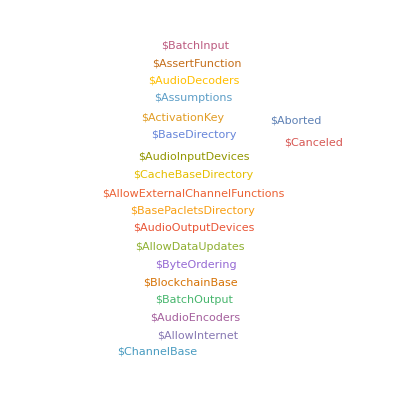

```mathematica
functionNames=CanonicalName/@WolframLanguageData[];
WordCloud[Take[functionNames,20]]
```

## String Manipulation

```mathematica
StringPosition["GraphData",s_?UpperCaseQ]
```

{{1,1},{6,6}}

```mathematica
StringInsert["GraphData"," ",#]&[{6,6}]
```

Graph  Data

```mathematica
DeleteCases[StringSplit[StringInsert["GraphData"," ",#]&[{6,6}]," "],""]
```

{Graph,Data}

```mathematica
DeleteCases[StringSplit[StringInsert["GraphData"," ",#]&[{6,6}]," "],""]//InputForm
```

{"Graph", "Data"}

```mathematica
Rest@StringPosition["GraphData",s_?UpperCaseQ]
```

{{6,6}}

```mathematica
StringInsert["VertexShapeFunction"," ",#+1]&[First@Rest@StringPosition["GraphData",s_?UpperCaseQ]]
```

Vertex  ShapeFunction

```mathematica
StringInsert[StringInsert["VertexShapeFunction"," ",#+1]&[First@Rest@StringPosition["GraphData",s_?UpperCaseQ]]
```

```mathematica
DeleteCases[StringSplit[StringInsert["GraphData"," ",#]&[First@Rest@StringPosition["GraphData",s_?UpperCaseQ]]," "],""]
```

{Graph,Data}

```mathematica
StringPosition["VertexShapeFunction",s_?UpperCaseQ]
Rest@StringPosition["VertexShapeFunction",s_?UpperCaseQ]
```

{{1,1},{7,7},{12,12}}

{{7,7},{12,12}}

```mathematica
StringInsert["VertexShapeFunction"," ",#]&[First[Rest@StringPosition["VertexShapeFunction",s_?UpperCaseQ]]]
```

Vertex  ShapeFunction

```mathematica
StringPosition["VertexShapeFunction",LetterCharacter~~s_?UpperCaseQ]
```

{{6,7},{11,12}}

```mathematica
StringExtract["VertexShapeFunction",""->{6,7}]
```

{e,x}

```mathematica
StringExtract["VertexShapeFunction",""->All]
```

{,V,e,r,t,e,x,S,h,a,p,e,F,u,n,c,t,i,o,n,}

```mathematica
Cases[StringExtract["VertexShapeFunction",""->All],s_/;UpperCaseQ[s]]
```

{,V,S,F,}

## String Function

```mathematica
StringCases["VertexShapeFunction",RegularExpression["[A-Z][^A-Z]*"]]
```

{Vertex,Shape,Function}

```mathematica
StringCases[#,RegularExpression["[A-Z][^A-Z]*"]]&/@functionNames
```

{{Aborted},{Activation,Key},{Allow,Data,Updates},{Allow,External,Channel,Functions},{Allow,Internet},{Assert,Function},{Assumptions},{Audio,Decoders},{Audio,Encoders},{Audio,Input,Devices},{Audio,Output,Devices},{Base,Directory},{Base,Paclets,Directory},{Batch,Input},{Batch,Output},{Blockchain,Base},{Byte,Ordering},{Cache,Base,Directory},{Canceled},{Channel,Base},{Character,Encoding},{Character,Encodings},{Cloud,Account,Name},{Cloud,Base},{Cloud,Connected},{Cloud,Credits,Available},{Cloud,Evaluation},{Cloud,Expression,Base},{Cloud,Object,Name,Format},{Cloud,Object,U,R,L,Type},{Cloud,Root,Directory},{Cloud,Symbol,Base},{Cloud,User,I,D},{Cloud,User,U,U,I,D},{Cloud,Version},{Command,Line},{Compilation,Target},{Compiler,Environment},{Context},{Context,Aliases},{Context,Path},{Control,Active,Setting},{Cookie,Store},{Cookies},{Creation,Date},{Cryptographic,Elliptic,Curve,Names},{Current,Link},{Current,Task},{Current,Web,Session},{Data,Structures},{Date,String,Format},{Default,Audio,Input,Device},{Default,Audio,Output,Device},{Default,Front,End},{Default,Imaging,Device},{Default,Kernels},{Default,Local,Base},{Default,Network,Interface},{Default,Proxy,Rules},{Default,Remote,Batch,Submission,Environment},{Default,Remote,Kernel},{Default,System,Credential,Store},{Display},{Display,Function},{Distributed,Contexts},{Dynamic,Evaluation},{Echo},{Embed,Code,Environments},{Embeddable,Services},{Epilog},{Evaluation,Cloud,Base},{Evaluation,Cloud,Object},{Evaluation,Environment},{Export,Formats},{External,Identifier,Types},{External,Storage,Base},{Failed},{Font,Families},{Front,End},{Front,End,Session},{Generated,Asset,Location},{Geo,Location},{Geo,Location,City},{Geo,Location,Country},{Geo,Location,Source},{History,Length},{Home,Directory},{Ignore,E,O,F},{Image,Formatting,Width},{Image,Resolution},{Imaging,Device},{Imaging,Devices},{Import,Formats},{Incoming,Mail,Settings},{Initial,Directory},{Initialization},{Initialization,Contexts},{Input},{Input,File,Name},{Input,Stream,Methods},{Inspector},{Installation,Directory},{Interpreter,Types},{Iteration,Limit},{Kernel,Count},{Kernel,I,D},{Language},{Library,Path},{License,Expiration,Date},{License,I,D},{License,Server},{Line},{Linked},{Local,Base},{Local,Symbol,Base},{Machine,Addresses},{Machine,Domains},{Machine,Epsilon},{Machine,I,D},{Machine,Name},{Machine,Precision},{Machine,Type},{Max,Extra,Precision},{Max,Machine,Number},{Max,Number},{Max,Piecewise,Cases},{Max,Precision},{Max,Root,Degree},{Message,Groups},{Message,List},{Message,Pre,Print},{Messages},{Min,Machine,Number},{Min,Number},{Min,Precision},{Mobile,Phone},{Module,Number},{Network,Connected},{Network,Interfaces},{New,Message},{New,Symbol},{No,Value},{Notebook,Inline,Storage,Limit},{Notebooks},{Number,Marks},{Operating,System},{Output},{Output,Size,Limit},{Output,Stream,Methods},{Packages},{Parent,Link},{Parent,Process,I,D},{Password,File},{Path},{Pathname,Separator},{Performance,Goal},{Permissions},{Persistence,Base},{Persistence,Path},{Plot,Theme},{Post},{Pre},{Pre,Initialization},{Pre,Print},{Pre,Read},{Printout3,D,Previewer},{Process,I,D},{Processor,Count},{Processor,Type},{Progress,Reporting},{Publisher,I,D},{Random,Generator,State},{Recursion,Limit},{Release,Number},{Requester,Address},{Requester,Cloud,User,I,D},{Requester,Cloud,User,U,U,I,D},{Requester,Wolfram,I,D},{Requester,Wolfram,U,U,I,D},{Resource,System,Base},{Resource,System,Path},{Root,Directory},{S,S,H,Authentication},{Script,Command,Line},{Script,Input,String},{Service,Credits,Available},{Services},{Session,I,D},{Shared,Functions},{Shared,Variables},{Sound,Display,Function},{Source,Link},{Subtitle,Decoders},{Subtitle,Encoders},{Synchronous,Evaluation},{Syntax,Handler},{System},{System,Character,Encoding},{System,Credential,Store},{System,I,D},{System,Shell},{System,Time,Zone},{System,Word,Length},{Target,Systems},{Template,Path},{Temporary,Directory},{Test,File,Name},{Time,Unit},{Time,Zone},{Time,Zone,Entity},{Timed,Out},{Unit,System},{Urgent},{User,Agent,String},{User,Base,Directory},{User,Base,Paclets,Directory},{User,Documents,Directory},{User,U,R,L,Base},{Username},{Version},{Version,Number},{Video,Decoders},{Video,Encoders},{Voice,Styles},{Wolfram,Documents,Directory},{Wolfram,I,D},{Wolfram,U,U,I,D},{A,A,S,Triangle},{A,P,I,Function},{A,R,C,H,Process},{A,R,I,M,A,Process},{A,R,M,A,Process},{A,R,Process},{A,S,A,Triangle},{Abelian,Group},{Abort},{Abort,Kernels},{Abort,Protect},{Above},{Abs},{Abs,Arg},{Abs,Arg,Plot},{Absolute,Correlation},{Absolute,Correlation,Function},{Absolute,Current,Value},{Absolute,Dashing},{Absolute,File,Name},{Absolute,Options},{Absolute,Point,Size},{Absolute,Thickness},{Absolute,Time},{Absolute,Timing},{Acceptance,Threshold},{Accounting,Form},{Accumulate},{Accuracy},{Accuracy,Goal},{Acoustic,Absorbing,Value},{Acoustic,Impedance,Value},{Acoustic,Normal,Velocity,Value},{Acoustic,P,D,E,Component},{Acoustic,Pressure,Condition},{Acoustic,Radiation,Value},{Acoustic,Sound,Hard,Value},{Acoustic,Sound,Soft,Condition},{Action,Menu},{Activate},{Active,Classification},{Active,Classification,Object},{Active,Prediction},{Active,Prediction,Object},{Active,Style},{Acyclic,Graph,Q},{Add,Sides},{Add,To},{Add,To,Search,Index},{Add,Users},{Adjacency,Graph},{Adjacency,List},{Adjacency,Matrix},{Adjacent,Mesh,Cells},{Adjugate},{Adjust,Time,Series,Forecast},{Adjustment,Box},{Adjustment,Box,Options},{Administrative,Division,Data},{Affine,Half,Space},{Affine,Space},{Affine,State,Space,Model},{Affine,Transform},{After},{Aggregated,Entity,Class},{Aggregation,Layer},{Air,Pressure,Data},{Air,Sound,Attenuation},{Air,Temperature,Data},{Aircraft,Data},{Airport,Data},{Airy,Ai},{Airy,Ai,Prime},{Airy,Ai,Zero},{Airy,Bi},{Airy,Bi,Prime},{Airy,Bi,Zero},{Algebraic,Integer,Q},{Algebraic,Number},{Algebraic,Number,Denominator},{Algebraic,Number,Norm},{Algebraic,Number,Polynomial},{Algebraic,Number,Trace},{Algebraic,Unit,Q},{Algebraics},{Alignment},{Alignment,Point},{All},{All,True},{Allow,Group,Close},{Allow,Inline,Cells},{Allow,Loose,Grammar},{Allow,Reverse,Group,Close},{Allow,Version,Update},{Allowed,Cloud,Extra,Parameters},{Allowed,Cloud,Parameter,Extensions},{Allowed,Dimensions},{Allowed,Frequency,Range},{Allowed,Heads},{Alpha,Channel},{Alphabet},{Alphabetic,Order},{Alphabetic,Sort},{Alternating,Factorial},{Alternating,Group},{Alternative,Hypothesis},{Alternatives},{Altitude,Method},{Ambient,Light},{Ambiguity,Function},{Ambiguity,List},{Anatomy,Data},{Anatomy,Plot3,D},{Anatomy,Skin,Style},{Anatomy,Styling},{Anchored,Search},{And},{Anderson,Darling,Test},{Anger,J},{Angle,Bisector},{Angle,Bracket},{Angle,Path},{Angle,Path3,D},{Angle,Vector},{Angular,Gauge},{Animate},{Animated,Image},{Animation,Direction},{Animation,Rate},{Animation,Repetitions},{Animation,Run,Time},{Animation,Running},{Animation,Time,Index},{Animation,Video},{Animator},{Annotate},{Annotation},{Annotation,Delete},{Annotation,Keys},{Annotation,Rules},{Annotation,Value},{Annuity},{Annuity,Due},{Annulus},{Anomaly,Detection},{Anomaly,Detector},{Anomaly,Detector,Function},{Anonymous},{Antialiasing},{Antihermitian},{Antihermitian,Matrix,Q},{Antisymmetric},{Antisymmetric,Matrix,Q},{Antonyms},{Any,Order},{Any,Subset},{Any,True},{Apart},{Apart,Square,Free},{Appearance},{Appearance,Elements},{Appearance,Rules},{Appell,F1},{Append},{Append,Layer},{Append,To},{Application},{Apply},{Apply,Sides},{Apply,To},{Arc,Cos},{Arc,Cosh},{Arc,Cot},{Arc,Coth},{Arc,Csc},{Arc,Csch},{Arc,Curvature},{Arc,Length},{Arc,Sec},{Arc,Sech},{Arc,Sin},{Arc,Sin,Distribution},{Arc,Sinh},{Arc,Tan},{Arc,Tanh},{Area},{Arg},{Arg,Max},{Arg,Min},{Arguments,Options},{Arithmetic,Geometric,Mean},{Around},{Around,Replace},{Array},{Array,Components},{Array,Depth},{Array,Filter},{Array,Flatten},{Array,Mesh},{Array,Pad},{Array,Plot},{Array,Plot3,D},{Array,Q},{Array,Reduce},{Array,Resample},{Array,Reshape},{Array,Rules},{Arrays},{Arrow},{Arrowheads},{Ask},{Ask,Append},{Ask,Confirm},{Ask,Display},{Ask,Function},{Ask,State},{Ask,Template,Display},{Asked,Q},{Asked,Value},{Aspect,Ratio},{Assert},{Assessment,Function},{Assessment,Result,Object},{Associate,To},{Association},{Association,Format},{Association,Map},{Association,Q},{Association,Thread},{Assume,Deterministic},{Assuming},{Assumptions},{Asymptotic},{Asymptotic,D,Solve,Value},{Asymptotic,Equal},{Asymptotic,Equivalent},{Asymptotic,Expectation},{Asymptotic,Greater},{Asymptotic,Greater,Equal},{Asymptotic,Integrate},{Asymptotic,Less},{Asymptotic,Less,Equal},{Asymptotic,Output,Tracker},{Asymptotic,Probability},{Asymptotic,Product},{Asymptotic,R,Solve,Value},{Asymptotic,Solve},{Asymptotic,Sum},{Asynchronous},{Atom},{Atom,Coordinates},{Atom,Count},{Atom,Diagram,Coordinates},{Atom,Label,Style},{Atom,Labels},{Atom,List},{Atom,Q},{Attach,Cell},{Attached,Cell},{Attention,Layer},{Attributes},{Audio},{Audio,Amplify},{Audio,Annotate},{Audio,Annotation,Lookup},{Audio,Block,Map},{Audio,Capture},{Audio,Channel,Assignment},{Audio,Channel,Combine},{Audio,Channel,Mix},{Audio,Channel,Separate},{Audio,Channels},{Audio,Data},{Audio,Delay},{Audio,Delete},{Audio,Distance},{Audio,Encoding},{Audio,Fade},{Audio,Frequency,Shift},{Audio,Generator},{Audio,Identify},{Audio,Input,Device},{Audio,Insert},{Audio,Instance,Q},{Audio,Intervals},{Audio,Join},{Audio,Label},{Audio,Length},{Audio,Local,Measurements},{Audio,Loudness},{Audio,Measurements},{Audio,Normalize},{Audio,Output,Device},{Audio,Overlay},{Audio,Pad},{Audio,Pan},{Audio,Partition},{Audio,Pause},{Audio,Pitch,Shift},{Audio,Play},{Audio,Plot},{Audio,Q},{Audio,Record},{Audio,Replace},{Audio,Resample},{Audio,Reverb},{Audio,Reverse},{Audio,Sample,Rate},{Audio,Spectral,Map},{Audio,Spectral,Transformation},{Audio,Split},{Audio,Stop},{Audio,Stream},{Audio,Streams},{Audio,Time,Stretch},{Audio,Track,Apply},{Audio,Track,Selection},{Audio,Trim},{Audio,Type},{Augmented,Polyhedron},{Augmented,Symmetric,Polynomial},{Authentication},{Authentication,Dialog},{Auto,Action},{Auto,Copy},{Auto,Delete},{Auto,Indent},{Auto,Italic,Words},{Auto,Multiplication,Symbol},{Auto,Operator,Renderings},{Auto,Refreshed},{Auto,Remove},{Auto,Scroll},{Auto,Spacing},{Auto,Submitting},{Autocomplete},{Autocompletion,Function},{Autocorrelation,Test},{Automatic},{Autorun,Sequencing},{Axes},{Axes,Edge},{Axes,Label},{Axes,Origin},{Axes,Style},{Axiomatic,Theory},{Axis},{Axis,Label},{Axis,Object},{Axis,Style},{B,Spline,Basis},{B,Spline,Curve},{B,Spline,Function},{B,Spline,Surface},{Baby,Monster,Group,B},{Back},{Background},{Backslash},{Backward},{Ball},{Band},{Bandpass,Filter},{Bandstop,Filter},{Bar,Chart},{Bar,Chart3,D},{Bar,Legend},{Bar,Origin},{Bar,Spacing},{Barabasi,Albert,Graph,Distribution},{Barcode,Image},{Barcode,Recognize},{Baringhaus,Henze,Test},{Barlow,Proschan,Importance},{Barnes,G},{Bartlett,Hann,Window},{Bartlett,Window},{Base,Decode},{Base,Encode},{Base,Form},{Base,Style},{Baseline},{Baseline,Position},{Basic,Recurrent,Layer},{Batch,Normalization,Layer},{Batch,Size},{Bates,Distribution},{Battle,Lemarie,Wavelet},{Bayesian,Maximization},{Bayesian,Maximization,Object},{Bayesian,Minimization},{Bayesian,Minimization,Object},{Because},{Beckmann,Distribution},{Beep},{Before},{Begin},{Begin,Dialog,Packet},{Begin,Package},{Bell,B},{Bell,Y},{Below},{Benford,Distribution},{Benini,Distribution},{Benktander,Gibrat,Distribution},{Benktander,Weibull,Distribution},{Bernoulli,B},{Bernoulli,Distribution},{Bernoulli,Graph,Distribution},{Bernoulli,Process},{Bernstein,Basis},{Besag,L},{Bessel,Filter,Model},{Bessel,I},{Bessel,J},{Bessel,J,Zero},{Bessel,K},{Bessel,Y},{Bessel,Y,Zero},{Beta},{Beta,Binomial,Distribution},{Beta,Distribution},{Beta,Negative,Binomial,Distribution},{Beta,Prime,Distribution},{Beta,Regularized},{Between},{Betweenness,Centrality},{Beveled,Polyhedron},{Bezier,Curve},{Bezier,Function},{Bilateral,Filter},{Bilateral,Laplace,Transform},{Bilateral,Z,Transform},{Bin,Counts},{Bin,Lists},{Binarize},{Binary,Deserialize},{Binary,Distance},{Binary,Format},{Binary,Image,Q},{Binary,Read},{Binary,Read,List},{Binary,Serialize},{Binary,Write},{Binned,Variogram,List},{Binomial},{Binomial,Distribution},{Binomial,Point,Process},{Binomial,Process},{Binormal,Distribution},{Bio,Sequence},{Bio,Sequence,Back,Translate,List},{Bio,Sequence,Complement},{Bio,Sequence,Instances},{Bio,Sequence,Modify},{Bio,Sequence,Plot},{Bio,Sequence,Q},{Bio,Sequence,Reverse,Complement},{Bio,Sequence,Transcribe},{Bio,Sequence,Translate},{Biorthogonal,Spline,Wavelet},{Bipartite,Graph,Q},{Biquadratic,Filter,Model},{Birnbaum,Importance},{Birnbaum,Saunders,Distribution},{Bit,And},{Bit,Clear},{Bit,Get},{Bit,Length},{Bit,Not},{Bit,Or},{Bit,Rate},{Bit,Set},{Bit,Shift,Left},{Bit,Shift,Right},{Bit,Xor},{Biweight,Location},{Biweight,Midvariance},{Black},{Blackman,Harris,Window},{Blackman,Nuttall,Window},{Blackman,Window},{Blank},{Blank,Null,Sequence},{Blank,Sequence},{Blend},{Block},{Block,Map},{Block,Random},{Blockchain,Address,Data},{Blockchain,Base},{Blockchain,Block,Data},{Blockchain,Contract,Value},{Blockchain,Data},{Blockchain,Get},{Blockchain,Key,Encode},{Blockchain,Put},{Blockchain,Token,Data},{Blockchain,Transaction},{Blockchain,Transaction,Data},{Blockchain,Transaction,Sign},{Blockchain,Transaction,Submit},{Blomqvist,Beta},{Blomqvist,Beta,Test},{Blue},{Blur},{Bode,Plot},{Bohman,Window},{Bold},{Bond},{Bond,Count},{Bond,Label,Style},{Bond,Labels},{Bond,List},{Bond,Q},{Bookmarks},{Boole},{Boolean,Consecutive,Function},{Boolean,Convert},{Boolean,Counting,Function},{Boolean,Function},{Boolean,Graph},{Boolean,Maxterms},{Boolean,Minimize},{Boolean,Minterms},{Boolean,Q},{Boolean,Region},{Boolean,Strings},{Boolean,Table},{Boolean,Variables},{Booleans},{Border,Dimensions},{Borel,Tanner,Distribution},{Bottom},{Bottom,Hat,Transform},{Boundary,Discretize,Graphics},{Boundary,Discretize,Region},{Boundary,Mesh},{Boundary,Mesh,Region},{Boundary,Mesh,Region,Q},{Boundary,Style},{Bounded,Region,Q},{Bounding,Region},{Box,Data},{Box,Matrix},{Box,Object},{Box,Ratios},{Box,Style},{Box,Whisker,Chart},{Boxed},{Boxes},{Bracketing,Bar},{Bray,Curtis,Distance},{Breadth,First,Scan},{Break},{Bridge,Data},{Brightness,Equalize},{Broadcast,Station,Data},{Brown},{Brown,Forsythe,Test},{Brownian,Bridge,Process},{Bubble,Chart},{Bubble,Chart3,D},{Bubble,Scale},{Bubble,Sizes},{Building,Data},{Bullet,Gauge},{Business,Day,Q},{Butterfly,Graph},{Butterworth,Filter,Model},{Button},{Button,Bar},{Button,Box},{Button,Box,Options},{Button,Data},{Button,Function},{Button,Min,Height},{Button,Notebook},{Button,Source},{Byte},{Byte,Array},{Byte,Array,Format},{Byte,Array,Format,Q},{Byte,Array,Q},{Byte,Array,To,String},{Byte,Count},{Byte,Ordering},{C},{C,D,F},{C,D,F,Deploy},{C,D,F,Wavelet},{C,Form},{C,M,Y,K,Color},{C,S,G,Region},{C,S,G,Region,Q},{C,S,G,Region,Tree},{C,T,C,Loss,Layer},{Cache,Persistence},{Calendar,Convert},{Calendar,Data},{Calendar,Type},{Call,Packet},{Callout},{Callout,Marker},{Callout,Style},{Canberra,Distance},{Cancel},{Cancel,Button},{Candlestick,Chart},{Canonical,Graph},{Canonical,Name},{Canonical,Warping,Correspondence},{Canonical,Warping,Distance},{Canonicalize,Polygon},{Canonicalize,Polyhedron},{Canonicalize,Region},{Cantor,Mesh},{Cantor,Staircase},{Canvas},{Cap},{Cap,Form},{Capital,Differential,D},{Capitalize},{Capsule,Shape},{Capture,Running},{Carleman,Linearize},{Carlson,R,C},{Carlson,R,D},{Carlson,R,E},{Carlson,R,F},{Carlson,R,G},{Carlson,R,J},{Carlson,R,K},{Carlson,R,M},{Carmichael,Lambda},{Case,Ordering},{Case,Sensitive},{Cases},{Cashflow},{Casoratian},{Catalan},{Catalan,Number},{Catch},{Categorical,Distribution},{Catenate},{Catenate,Layer},{Cauchy,Distribution},{Cauchy,Point,Process},{Cauchy,Window},{Cayley,Graph},{Ceiling},{Celestial,System},{Cell},{Cell,Auto,Overwrite},{Cell,Baseline},{Cell,Bracket,Options},{Cell,Change,Times},{Cell,Context},{Cell,Dingbat},{Cell,Dynamic,Expression},{Cell,Edit,Duplicate},{Cell,Epilog},{Cell,Evaluation,Duplicate},{Cell,Evaluation,Function},{Cell,Event,Actions},{Cell,Frame},{Cell,Frame,Color},{Cell,Frame,Label,Margins},{Cell,Frame,Labels},{Cell,Frame,Margins},{Cell,Group},{Cell,Group,Data},{Cell,Grouping},{Cell,I,D},{Cell,Label},{Cell,Label,Auto,Delete},{Cell,Label,Style},{Cell,Margins},{Cell,Object},{Cell,Open},{Cell,Print},{Cell,Prolog},{Cell,Style},{Cell,Tags},{Cells},{Cellular,Automaton},{Censored,Distribution},{Censoring},{Center},{Center,Array},{Center,Dot},{Centered,Interval},{Central,Feature},{Central,Moment},{Central,Moment,Generating,Function},{Cepstrogram},{Cepstrogram,Array},{Cepstrum,Array},{Champernowne,Number},{Chan,Vese,Binarize},{Channel,Base},{Channel,Broker,Action},{Channel,History,Length},{Channel,Listen},{Channel,Listener},{Channel,Listeners},{Channel,Object},{Channel,Receiver,Function},{Channel,Send},{Channel,Subscribers},{Character},{Character,Counts},{Character,Encoding},{Character,Name},{Character,Normalize},{Character,Range},{Characteristic,Function},{Characteristic,Polynomial},{Characters},{Chart,Base,Style},{Chart,Element,Function},{Chart,Elements},{Chart,Labels},{Chart,Layout},{Chart,Legends},{Chart,Style},{Chebyshev1,Filter,Model},{Chebyshev2,Filter,Model},{Chebyshev,T},{Chebyshev,U},{Check},{Check,Abort},{Check,Arguments},{Checkbox},{Checkbox,Bar},{Chemical,Data},{Chemical,Formula},{Chemical,Reaction},{Chessboard,Distance},{Chi,Distribution},{Chi,Square,Distribution},{Chinese,Remainder},{Choice,Buttons},{Choice,Dialog},{Cholesky,Decomposition},{Chop},{Chromatic,Polynomial},{Chromaticity,Plot},{Chromaticity,Plot3,D},{Circle},{Circle,Dot},{Circle,Minus},{Circle,Plus},{Circle,Points},{Circle,Through},{Circle,Times},{Circulant,Graph},{Circular,Orthogonal,Matrix,Distribution},{Circular,Quaternion,Matrix,Distribution},{Circular,Real,Matrix,Distribution},{Circular,Symplectic,Matrix,Distribution},{Circular,Unitary,Matrix,Distribution},{Circumsphere},{City,Data},{Class,Priors},{Classifier,Function},{Classifier,Measurements},{Classifier,Measurements,Object},{Classify},{Clear},{Clear,All},{Clear,Attributes},{Clear,Cookies},{Clear,Permissions},{Clear,System,Cache},{Clebsch,Gordan},{Click,Pane},{Click,To,Copy},{Click,To,Copy,Enabled},{Clip},{Clip,Planes},{Clip,Planes,Style},{Clip,Range},{Clipping,Style},{Clock},{Clock,Gauge},{Close},{Close,Kernels},{Closeness,Centrality},{Closing},{Cloud,Account,Data},{Cloud,Base},{Cloud,Connect},{Cloud,Deploy},{Cloud,Directory},{Cloud,Disconnect},{Cloud,Evaluate},{Cloud,Export},{Cloud,Expression},{Cloud,Expressions},{Cloud,Function},{Cloud,Get},{Cloud,Import},{Cloud,Logging,Data},{Cloud,Object},{Cloud,Object,Name,Format},{Cloud,Object,U,R,L,Type},{Cloud,Objects},{Cloud,Publish},{Cloud,Put},{Cloud,Rendering,Method},{Cloud,Save},{Cloud,Share},{Cloud,Submit},{Cloud,Symbol},{Cloud,Unshare},{Cluster,Classify},{Cluster,Dissimilarity,Function},{Clustering,Components},{Clustering,Tree},{Code,Assist,Options},{Coefficient},{Coefficient,Arrays},{Coefficient,List},{Coefficient,Rules},{Coiflet,Wavelet},{Collect},{Collinear,Points},{Colon},{Color,Balance},{Color,Combine},{Color,Convert},{Color,Coverage},{Color,Data},{Color,Data,Function},{Color,Detect},{Color,Distance},{Color,Function},{Color,Function,Binning},{Color,Function,Scaling},{Color,Negate},{Color,Profile,Data},{Color,Q},{Color,Quantize},{Color,Replace},{Color,Rules},{Color,Separate},{Color,Setter},{Color,Slider},{Color,Space},{Color,Tone,Mapping},{Colorize},{Colors,Near},{Column},{Column,Alignments},{Column,Lines},{Column,Spacings},{Column,Widths},{Columns,Equal},{Combinator,B},{Combinator,C},{Combinator,I},{Combinator,K},{Combinator,S},{Combinator,W},{Combinator,Y},{Combined,Entity,Class},{Combiner,Function},{Comet,Data},{Common,Name},{Common,Units},{Commonest},{Commonest,Filter},{Community,Boundary,Style},{Community,Graph,Plot},{Community,Labels},{Community,Region,Style},{Company,Data},{Compatible,Unit,Q},{Compilation,Options},{Compilation,Target},{Compile},{Compiled},{Compiled,Code,Function},{Compiled,Function},{Compiled,Layer},{Compiler,Environment},{Compiler,Environment,Append,To},{Compiler,Environment,Object},{Compiler,Options},{Complement},{Complemented,Entity,Class},{Complete,Graph},{Complete,Graph,Q},{Complete,Integral},{Complete,Kary,Tree},{Complex},{Complex,Array,Plot},{Complex,Contour,Plot},{Complex,Expand},{Complex,Infinity},{Complex,List,Plot},{Complex,Plot},{Complex,Plot3,D},{Complex,Region,Plot},{Complex,Stream,Plot},{Complex,Vector,Plot},{Complexes},{Complexity,Function},{Component,Measurements},{Compose,List},{Compose,Series},{Composite,Q},{Composition},{Compound,Element},{Compound,Expression},{Compound,Poisson,Distribution},{Compound,Poisson,Process},{Compound,Renewal,Process},{Compress},{Compression,Level},{Compute,Uncertainty},{Concave,Hull,Mesh},{Condition},{Conditional,Expression},{Conditioned},{Cone},{Confidence,Level},{Confidence,Range},{Confidence,Transform},{Confirm},{Confirm,Assert},{Confirm,By},{Confirm,Match},{Confirm,Quiet},{Conform,Audio},{Conform,Images},{Conformation,Method},{Congruent},{Conic,Gradient,Filling},{Conic,Hull,Region},{Conic,Optimization},{Conjugate},{Conjugate,Transpose},{Conjunction},{Connect,Library,Callback,Function},{Connect,System,Model,Components},{Connect,System,Model,Controller},{Connected,Components},{Connected,Graph,Components},{Connected,Graph,Q},{Connected,Mesh,Components},{Connected,Molecule,Components},{Connected,Molecule,Q},{Connection,Settings},{Connes,Window},{Conover,Test},{Conservative,Convection,P,D,E,Term},{Constant},{Constant,Array},{Constant,Image},{Constant,Region,Q},{Constants},{Constellation,Data},{Construct},{Containing},{Contains,All},{Contains,Any},{Contains,Exactly},{Contains,None},{Contains,Only},{Content,Detector,Function},{Content,Field,Options},{Content,Location,Function},{Content,Object},{Content,Padding},{Content,Selectable},{Content,Size},{Context},{Context,To,File,Name},{Contexts},{Continue},{Continued,Fraction},{Continued,Fraction,K},{Continuous,Action},{Continuous,Markov,Process},{Continuous,Task},{Continuous,Time,Model,Q},{Continuous,Wavelet,Data},{Continuous,Wavelet,Transform},{Contour,Detect},{Contour,Labels},{Contour,Plot},{Contour,Plot3,D},{Contour,Shading},{Contour,Style},{Contours},{Contraharmonic,Mean},{Contrastive,Loss,Layer},{Control},{Control,Active},{Control,Placement},{Control,Type},{Controllability,Gramian},{Controllability,Matrix},{Controllable,Decomposition},{Controllable,Model,Q},{Controller,Information},{Controller,Linking},{Controller,Manipulate},{Controller,Method},{Controller,Path},{Controller,State},{Controls,Rendering},{Convection,P,D,E,Term},{Convergents},{Conversion,Rules},{Convex,Hull,Mesh},{Convex,Hull,Region},{Convex,Optimization},{Convex,Polygon,Q},{Convex,Polyhedron,Q},{Convex,Region,Q},{Convolution,Layer},{Convolve},{Conway,Group,Co1},{Conway,Group,Co2},{Conway,Group,Co3},{Cookie,Function},{Coordinate,Bounding,Box},{Coordinate,Bounding,Box,Array},{Coordinate,Bounds},{Coordinate,Bounds,Array},{Coordinate,Chart,Data},{Coordinate,Transform},{Coordinate,Transform,Data},{Coordinates,Tool,Options},{Coplanar,Points},{Coprime,Q},{Coproduct},{Copula,Distribution},{Copy,Databin},{Copy,Directory},{Copy,File},{Copy,Function},{Copy,To,Clipboard},{Copyable},{Core,Nilpotent,Decomposition},{Corner,Filter},{Corner,Neighbors},{Correlation},{Correlation,Distance},{Correlation,Function},{Correlation,Test},{Cos},{Cos,Integral},{Cosh},{Cosh,Integral},{Cosine,Distance},{Cosine,Window},{Cot},{Coth},{Coulomb,F},{Coulomb,G},{Coulomb,H1},{Coulomb,H2},{Count},{Count,Distinct},{Count,Distinct,By},{Count,Roots},{Country,Data},{Counts},{Counts,By},{Covariance},{Covariance,Estimator,Function},{Covariance,Function},{Cox,Ingersoll,Ross,Process},{Cox,Model},{Cox,Model,Fit},{Coxian,Distribution},{Cramer,Von,Mises,Test},{Create,Archive},{Create,Cell,I,D},{Create,Channel},{Create,Cloud,Expression},{Create,Compiler,Environment},{Create,Data,Structure},{Create,Data,System,Model},{Create,Databin},{Create,Dialog},{Create,Directory},{Create,Document},{Create,File},{Create,Intermediate,Directories},{Create,License,Entitlement},{Create,Managed,Library,Expression},{Create,Notebook},{Create,Paclet,Archive},{Create,Palette},{Create,Permissions,Group},{Create,Search,Index},{Create,System,Model},{Create,U,U,I,D},{Create,Window},{Criterion,Function},{Critical,Section},{Criticality,Failure,Importance},{Criticality,Success,Importance},{Cross},{Cross,Entropy,Loss,Layer},{Cross,Matrix},{Crossing,Count},{Crossing,Detect},{Crossing,Polygon},{Csc},{Csch},{Cube},{Cube,Root},{Cubics},{Cuboid},{Cumulant},{Cumulant,Generating,Function},{Cup},{Cup,Cap},{Curl},{Currency,Convert},{Current,Date},{Current,Image},{Current,Notebook,Image},{Current,Screen,Image},{Current,Value},{Curry,Applied},{Curvature,Flow,Filter},{Curve,Closed},{Cyan},{Cycle,Graph},{Cycle,Index,Polynomial},{Cycles},{Cyclic,Group},{Cyclotomic},{Cylinder},{Cylindrical,Decomposition},{Cylindrical,Decomposition,Function},{D},{D,Eigensystem},{D,Eigenvalues},{D,Gaussian,Wavelet},{D,M,S,List},{D,M,S,String},{D,Solve},{D,Solve,Value},{Dagum,Distribution},{Dam,Data},{Damerau,Levenshtein,Distance},{Darker},{Dashed},{Dashing},{Data,Distribution},{Data,Range},{Data,Reversed},{Data,Structure},{Data,Structure,Q},{Database,Connect},{Database,Disconnect},{Database,Reference},{Databin},{Databin,Add},{Databin,Submit},{Databin,Upload},{Databins},{Dataset},{Dataset,Theme},{Date,Bounds},{Date,Difference},{Date,Format},{Date,Function},{Date,Histogram},{Date,Interval},{Date,List},{Date,List,Log,Plot},{Date,List,Plot},{Date,List,Step,Plot},{Date,Object},{Date,Object,Q},{Date,Overlaps,Q},{Date,Pattern},{Date,Plus},{Date,Range},{Date,Reduction},{Date,Scale},{Date,Select},{Date,String},{Date,Ticks,Format},{Date,Value},{Date,Within,Q},{Dated},{Dated,Unit},{Daubechies,Wavelet},{Davis,Distribution},{Dawson,F},{Day,Count},{Day,Count,Convention},{Day,Hemisphere},{Day,Match,Q},{Day,Name},{Day,Night,Terminator},{Day,Plus},{Day,Range},{Day,Round},{Daylight,Q},{De,Bruijn,Graph},{De,Bruijn,Sequence},{Decapitalize},{Decimal,Form},{Declare,Package},{Decompose},{Deconvolution,Layer},{Decrement},{Decrypt},{Decrypt,File},{Dedekind,Eta},{Deep,Space,Probe,Data},{Default},{Default,Axes,Style},{Default,Base,Style},{Default,Box,Style},{Default,Button},{Default,Duplicate,Cell,Style},{Default,Duration},{Default,Element},{Default,Face,Grids,Style},{Default,Field,Hint,Style},{Default,Frame,Style},{Default,Frame,Ticks,Style},{Default,Grid,Lines,Style},{Default,Label,Style},{Default,Menu,Style},{Default,Natural,Language},{Default,New,Cell,Style},{Default,Options},{Default,Print,Precision},{Default,Ticks,Style},{Default,Tooltip,Style},{Default,Values},{Defer},{Define,Input,Stream,Method},{Define,Output,Stream,Method},{Define,Resource,Function},{Definition},{Degree},{Degree,Centrality},{Degree,Graph,Distribution},{Deinitialization},{Del},{Delaunay,Mesh},{Delayed},{Deletable},{Delete},{Delete,Anomalies},{Delete,Border,Components},{Delete,Cases},{Delete,Channel},{Delete,Cloud,Expression},{Delete,Contents},{Delete,Directory},{Delete,Duplicates},{Delete,Duplicates,By},{Delete,File},{Delete,Missing},{Delete,Object},{Delete,Permissions,Key},{Delete,Search,Index},{Delete,Small,Components},{Delete,Stopwords},{Delimited,Sequence},{Delimiter},{Delimiter,Auto,Matching},{Delimiter,Flash,Time},{Delimiters},{Delivery,Function},{Dendrogram},{Denominator},{Density,Histogram},{Density,Plot},{Density,Plot3,D},{Dependent,Variables},{Deploy},{Deployed},{Depth},{Depth,First,Scan},{Derivative},{Derivative,Filter},{Derivative,P,D,E,Term},{Derived,Key},{Descriptor,State,Space},{Design,Matrix},{Det},{Device,Close},{Device,Configure},{Device,Execute},{Device,Execute,Asynchronous},{Device,Object},{Device,Open},{Device,Read},{Device,Read,Buffer},{Device,Read,Latest},{Device,Read,List},{Device,Read,Time,Series},{Device,Streams},{Device,Write},{Device,Write,Buffer},{Devices},{Diagonal},{Diagonal,Matrix},{Diagonal,Matrix,Q},{Diagonalizable,Matrix,Q},{Dialog},{Dialog,Input},{Dialog,Notebook},{Dialog,Prolog},{Dialog,Return},{Dialog,Symbols},{Diamond},{Diamond,Matrix},{Dice,Dissimilarity},{Dictionary,Lookup},{Dictionary,Word,Q},{Difference,Delta},{Difference,Quotient},{Difference,Root},{Difference,Root,Reduce},{Differences},{Differential,D},{Differential,Root},{Differential,Root,Reduce},{Differentiator,Filter},{Diffusion,P,D,E,Term},{Diggle,Gates,Point,Process},{Diggle,Gratton,Point,Process},{Digit,Block},{Digit,Character},{Digit,Count},{Digit,Q},{Digital,Signature},{Dihedral,Angle},{Dihedral,Group},{Dilation},{Dimension,Reduce},{Dimension,Reducer,Function},{Dimension,Reduction},{Dimensional,Combinations},{Dimensional,Mesh,Components},{Dimensions},{Dirac,Comb},{Dirac,Delta},{Directed,Edge},{Directed,Edges},{Directed,Graph},{Directed,Graph,Q},{Directed,Infinity},{Direction},{Directional,Light},{Directive},{Directory},{Directory,Name},{Directory,Q},{Directory,Stack},{Dirichlet,Beta},{Dirichlet,Character},{Dirichlet,Condition},{Dirichlet,Convolve},{Dirichlet,Distribution},{Dirichlet,Eta},{Dirichlet,L},{Dirichlet,Lambda},{Dirichlet,Transform},{Dirichlet,Window},{Disable,Formatting},{Discrete,Asymptotic},{Discrete,Chirp,Z,Transform},{Discrete,Convolve},{Discrete,Delta},{Discrete,Hadamard,Transform},{Discrete,Indicator},{Discrete,L,Q,Estimator,Gains},{Discrete,L,Q,Regulator,Gains},{Discrete,Limit},{Discrete,Lyapunov,Solve},{Discrete,Markov,Process},{Discrete,Max,Limit},{Discrete,Min,Limit},{Discrete,Plot},{Discrete,Plot3,D},{Discrete,Ratio},{Discrete,Riccati,Solve},{Discrete,Shift},{Discrete,Time,Model,Q},{Discrete,Uniform,Distribution},{Discrete,Variables},{Discrete,Wavelet,Data},{Discrete,Wavelet,Packet,Transform},{Discrete,Wavelet,Transform},{Discretize,Graphics},{Discretize,Region},{Discriminant},{Disjoint,Q},{Disjunction},{Disk},{Disk,Matrix},{Disk,Segment},{Dispatch},{Dispersion,Estimator,Function},{Display,All,Steps},{Display,End,Packet},{Display,Form},{Display,Function},{Display,Packet},{Distance,Function},{Distance,Matrix},{Distance,Transform},{Distribute},{Distribute,Definitions},{Distributed},{Distributed,Contexts},{Distribution,Chart},{Distribution,Fit,Test},{Distribution,Parameter,Assumptions},{Distribution,Parameter,Q},{Dithering},{Div},{Divide},{Divide,By},{Divide,Sides},{Dividers},{Divisible},{Divisor,Sigma},{Divisor,Sum},{Divisors},{Do},{Docked,Cells},{Document,Generator},{Document,Generator,Information},{Document,Generators},{Document,Notebook},{Document,Weighting,Rules},{Dodecahedron},{Dominant,Colors},{Dominator,Tree,Graph},{Dominator,Vertex,List},{Dot},{Dot,Dashed},{Dot,Equal},{Dot,Layer},{Dotted},{Double,Bracketing,Bar},{Double,Down,Arrow},{Double,Left,Arrow},{Double,Left,Right,Arrow},{Double,Left,Tee},{Double,Long,Left,Arrow},{Double,Long,Left,Right,Arrow},{Double,Long,Right,Arrow},{Double,Right,Arrow},{Double,Right,Tee},{Double,Up,Arrow},{Double,Up,Down,Arrow},{Double,Vertical,Bar},{Down,Arrow},{Down,Arrow,Bar},{Down,Arrow,Up,Arrow},{Down,Left,Right,Vector},{Down,Left,Tee,Vector},{Down,Left,Vector},{Down,Left,Vector,Bar},{Down,Right,Tee,Vector},{Down,Right,Vector},{Down,Right,Vector,Bar},{Down,Tee},{Down,Tee,Arrow},{Down,Values},{Downsample},{Drazin,Inverse},{Drop},{Dropout,Layer},{Dt},{Dual,Planar,Graph},{Dual,Polyhedron},{Dual,Systems,Model},{Dump,Save},{Duplicate,Free,Q},{Duration},{Dynamic},{Dynamic,Evaluation,Timeout},{Dynamic,Geo,Graphics},{Dynamic,Image},{Dynamic,Module},{Dynamic,Module,Values},{Dynamic,Setting},{Dynamic,Updating},{Dynamic,Wrapper},{E},{Earth,Impact,Data},{Earthquake,Data},{Eccentricity,Centrality},{Echo},{Echo,Evaluation},{Echo,Function},{Echo,Label},{Echo,Timing},{Eclipse,Type},{Edge,Add},{Edge,Betweenness,Centrality},{Edge,Capacity},{Edge,Chromatic,Number},{Edge,Connectivity},{Edge,Contract},{Edge,Cost},{Edge,Count},{Edge,Cover,Q},{Edge,Cycle,Matrix},{Edge,Delete},{Edge,Detect},{Edge,Form},{Edge,Index},{Edge,Label,Style},{Edge,Labels},{Edge,List},{Edge,Q},{Edge,Rules},{Edge,Shape,Function},{Edge,Style},{Edge,Tagged,Graph},{Edge,Tagged,Graph,Q},{Edge,Tags},{Edge,Transitive,Graph,Q},{Edge,Value,Range},{Edge,Value,Sizes},{Edge,Weight},{Edge,Weighted,Graph,Q},{Edit,Distance},{Editable},{Effective,Interest},{Eigensystem},{Eigenvalues},{Eigenvector,Centrality},{Eigenvectors},{Element},{Element,Data},{Elementwise,Layer},{Elided,Forms},{Eliminate},{Ellipsoid},{Elliptic,E},{Elliptic,Exp},{Elliptic,Exp,Prime},{Elliptic,F},{Elliptic,Filter,Model},{Elliptic,K},{Elliptic,Log},{Elliptic,Nome,Q},{Elliptic,Pi},{Elliptic,Theta},{Elliptic,Theta,Prime},{Embed,Code},{Embedded,H,T,M,L},{Embedded,S,Q,L,Entity,Class},{Embedded,S,Q,L,Expression},{Embedded,Service},{Embedding,Layer},{Emit,Sound},{Empirical,Distribution},{Empty,Graph,Q},{Empty,Region},{Empty,Space,F},{Enabled},{Enclose},{Encode},{Encrypt},{Encrypt,File},{Encrypted,Object},{End},{End,Dialog,Packet},{End,Of,Buffer},{End,Of,File},{End,Of,Line},{End,Of,String},{End,Package},{Engineering,Form},{Enter,Expression,Packet},{Enter,Text,Packet},{Entity},{Entity,Class},{Entity,Class,List},{Entity,Copies},{Entity,Function},{Entity,Group},{Entity,Instance},{Entity,List},{Entity,Prefetch},{Entity,Properties},{Entity,Property},{Entity,Property,Class},{Entity,Register},{Entity,Store},{Entity,Stores},{Entity,Type,Name},{Entity,Unregister},{Entity,Value},{Entropy},{Entropy,Filter},{Environment},{Epilog},{Epilog,Function},{Equal},{Equal,Tilde},{Equal,To},{Equilibrium},{Equiripple,Filter,Kernel},{Equivalent},{Erf},{Erfc},{Erfi},{Erlang,B},{Erlang,C},{Erlang,Distribution},{Erosion},{Error,Box},{Escape,Radius},{Estimated,Background},{Estimated,Distribution},{Estimated,Point,Process},{Estimated,Process},{Estimated,Variogram,Model},{Estimator,Gains},{Estimator,Regulator},{Euclidean,Distance},{Euler,Angles},{Euler,Characteristic},{Euler,E},{Euler,Gamma},{Euler,Matrix},{Euler,Phi},{Eulerian,Graph,Q},{Evaluatable},{Evaluate},{Evaluate,Packet},{Evaluation,Box},{Evaluation,Cell},{Evaluation,Data},{Evaluation,Elements},{Evaluation,Environment},{Evaluation,Monitor},{Evaluation,Notebook},{Evaluation,Object},{Evaluation,Privileges},{Evaluator},{Evaluator,Names},{Even,Q},{Event,Data},{Event,Handler},{Event,Labels},{Event,Series},{Exact,Blackman,Window},{Exact,Number,Q},{Example,Data},{Except},{Exclude,Pods},{Excluded,Contexts},{Excluded,Forms},{Excluded,Lines},{Excluded,Physical,Quantities},{Exclusions},{Exclusions,Style},{Exists},{Exit},{Exoplanet,Data},{Exp},{Exp,Gamma,Distribution},{Exp,Integral,E},{Exp,Integral,Ei},{Exp,To,Trig},{Expand},{Expand,All},{Expand,Denominator},{Expand,File,Name},{Expand,Numerator},{Expectation},{Expiration,Date},{Exponent},{Exponent,Function},{Exponent,Step},{Exponential,Distribution},{Exponential,Family},{Exponential,Generating,Function},{Exponential,Moving,Average},{Exponential,Power,Distribution},{Export},{Export,Byte,Array},{Export,Form},{Export,String},{Expression},{Expression,Cell},{Expression,Graph},{Expression,Tree},{Expression,U,U,I,D},{Extended,Entity,Class},{Extended,G,C,D},{Extension},{Extent,Element,Function},{Extent,Markers},{Extent,Size},{External,Bundle},{External,Evaluate},{External,Function},{External,Identifier},{External,Object},{External,Options},{External,Session,Object},{External,Sessions},{External,Storage,Base},{External,Storage,Download},{External,Storage,Get},{External,Storage,Object},{External,Storage,Put},{External,Storage,Upload},{External,Type,Signature},{External,Value},{Extract},{Extract,Archive},{Extract,Layer},{Extract,Paclet,Archive},{Extreme,Value,Distribution},{F,A,R,I,M,A,Process},{F,Ratio,Distribution},{Face,Align},{Face,Form},{Face,Grids},{Face,Grids,Style},{Face,Recognize},{Facial,Features},{Factor},{Factor,Integer},{Factor,List},{Factor,Square,Free},{Factor,Square,Free,List},{Factor,Terms},{Factor,Terms,List},{Factorial},{Factorial2},{Factorial,Moment},{Factorial,Moment,Generating,Function},{Factorial,Power},{Failure},{Failure,Action},{Failure,Distribution},{Failure,Q},{False},{Farey,Sequence},{Feature,Distance},{Feature,Extract},{Feature,Extraction},{Feature,Extractor},{Feature,Extractor,Function},{Feature,Names},{Feature,Nearest},{Feature,Space,Plot},{Feature,Space,Plot3,D},{Feature,Types},{Feedback,Linearize},{Feedback,Sector},{Feedback,Sector,Style},{Feedback,Type},{Fetal,Growth,Data},{Fibonacci},{Fibonorial},{Field,Completion,Function},{Field,Hint},{Field,Hint,Style},{Field,Masked},{Field,Size},{File},{File,Base,Name},{File,Byte,Count},{File,Convert},{File,Date},{File,Exists,Q},{File,Extension},{File,Format},{File,Format,Properties},{File,Format,Q},{File,Hash},{File,Name,Depth},{File,Name,Drop},{File,Name,Forms},{File,Name,Join},{File,Name,Setter},{File,Name,Split},{File,Name,Take},{File,Name,To,Format,List},{File,Names},{File,Print},{File,Size},{File,System,Map},{File,System,Scan},{File,Template},{File,Template,Apply},{File,Type},{Filled,Curve},{Filled,Torus},{Filling},{Filling,Style},{Filling,Transform},{Filter,Rules},{Filtered,Entity,Class},{Financial,Bond},{Financial,Data},{Financial,Derivative},{Financial,Indicator},{Find},{Find,Anomalies},{Find,Arg,Max},{Find,Arg,Min},{Find,Channels},{Find,Clique},{Find,Clusters},{Find,Cookies},{Find,Curve,Path},{Find,Cycle},{Find,Devices},{Find,Distribution},{Find,Distribution,Parameters},{Find,Divisions},{Find,Edge,Coloring},{Find,Edge,Cover},{Find,Edge,Cut},{Find,Edge,Independent,Paths},{Find,Equational,Proof},{Find,Eulerian,Cycle},{Find,External,Evaluators},{Find,Faces},{Find,File},{Find,Fit},{Find,Formula},{Find,Fundamental,Cycles},{Find,Generating,Function},{Find,Geo,Location},{Find,Geometric,Conjectures},{Find,Geometric,Transform},{Find,Graph,Communities},{Find,Graph,Isomorphism},{Find,Graph,Partition},{Find,Hamiltonian,Cycle},{Find,Hamiltonian,Path},{Find,Hidden,Markov,States},{Find,Image,Text},{Find,Independent,Edge,Set},{Find,Independent,Vertex,Set},{Find,Instance},{Find,Integer,Null,Vector},{Find,Isomers},{Find,Isomorphic,Subgraph},{Find,K,Clan},{Find,K,Clique},{Find,K,Club},{Find,K,Plex},{Find,Library},{Find,Linear,Recurrence},{Find,List},{Find,Matching,Color},{Find,Max,Value},{Find,Maximum},{Find,Maximum,Cut},{Find,Maximum,Flow},{Find,Mesh,Defects},{Find,Min,Value},{Find,Minimum},{Find,Minimum,Cost,Flow},{Find,Minimum,Cut},{Find,Molecule,Substructure},{Find,Path},{Find,Peaks},{Find,Permutation},{Find,Planar,Coloring},{Find,Point,Process,Parameters},{Find,Postman,Tour},{Find,Process,Parameters},{Find,Region,Transform},{Find,Repeat},{Find,Root},{Find,Sequence,Function},{Find,Settings},{Find,Shortest,Path},{Find,Shortest,Tour},{Find,Spanning,Tree},{Find,Subgraph,Isomorphism},{Find,System,Model,Equilibrium},{Find,Textual,Answer},{Find,Threshold},{Find,Transient,Repeat},{Find,Vertex,Coloring},{Find,Vertex,Cover},{Find,Vertex,Cut},{Find,Vertex,Independent,Paths},{Finish,Dynamic},{Finite,Abelian,Group,Count},{Finite,Group,Count},{Finite,Group,Data},{First},{First,Case},{First,Passage,Time,Distribution},{First,Position},{Fischer,Group,Fi22},{Fischer,Group,Fi23},{Fischer,Group,Fi24,Prime},{Fisher,Hypergeometric,Distribution},{Fisher,Ratio,Test},{Fisher,Z,Distribution},{Fit},{Fit,Regularization},{Fitted,Model},{Fixed,Order},{Fixed,Point},{Fixed,Point,List},{Flat},{Flat,Top,Window},{Flatten},{Flatten,At},{Flatten,Layer},{Flight,Data},{Flip,View},{Floor},{Flow,Polynomial},{Fold},{Fold,List},{Fold,Pair},{Fold,Pair,List},{Fold,While},{Fold,While,List},{Follow,Redirects},{Font,Color},{Font,Family},{Font,Size},{Font,Slant},{Font,Substitutions},{Font,Tracking},{Font,Variations},{Font,Weight},{For},{For,All},{Force,Version,Install},{Form,Box},{Form,Box,Options},{Form,Control},{Form,Function},{Form,Layout,Function},{Form,Object},{Form,Page},{Form,Protection,Method},{Format},{Format,Type},{Formula,Data},{Formula,Lookup},{Fortran,Form},{Forward},{Forward,Backward},{Forward,Cloud,Credentials},{Fourier},{Fourier,Coefficient},{Fourier,Cos,Coefficient},{Fourier,Cos,Series},{Fourier,Cos,Transform},{Fourier,D,C,T},{Fourier,D,C,T,Filter},{Fourier,D,C,T,Matrix},{Fourier,D,S,T},{Fourier,D,S,T,Matrix},{Fourier,Matrix},{Fourier,Parameters},{Fourier,Sequence,Transform},{Fourier,Series},{Fourier,Sin,Coefficient},{Fourier,Sin,Series},{Fourier,Sin,Transform},{Fourier,Transform},{Fourier,Trig,Series},{Fox,H},{Fox,H,Reduce},{Fraction,Box},{Fraction,Box,Options},{Fractional,Brownian,Motion,Process},{Fractional,Gaussian,Noise,Process},{Fractional,Part},{Frame},{Frame,Box},{Frame,Box,Options},{Frame,Label},{Frame,List,Video},{Frame,Margins},{Frame,Rate},{Frame,Style},{Frame,Ticks},{Frame,Ticks,Style},{Framed},{Frechet,Distribution},{Free,Q},{Frenet,Serret,System},{Frequency,Sampling,Filter,Kernel},{Fresnel,C},{Fresnel,F},{Fresnel,G},{Fresnel,S},{Friday},{Frobenius,Number},{Frobenius,Solve},{From,Absolute,Time},{From,Character,Code},{From,Coefficient,Rules},{From,Continued,Fraction},{From,D,M,S},{From,Date,String},{From,Digits},{From,Entity},{From,Julian,Date},{From,Letter,Number},{From,Polar,Coordinates},{From,Roman,Numeral},{From,Spherical,Coordinates},{From,Unix,Time},{Front},{Front,End,Dynamic,Expression},{Front,End,Event,Actions},{Front,End,Execute},{Front,End,Token},{Front,End,Token,Execute},{Full},{Full,Definition},{Full,Form},{Full,Graphics},{Full,Information,Output,Regulator},{Full,Region},{Full,Simplify},{Function},{Function,Analytic},{Function,Bijective},{Function,Compile},{Function,Compile,Export},{Function,Compile,Export,Byte,Array},{Function,Compile,Export,Library},{Function,Compile,Export,String},{Function,Continuous},{Function,Convexity},{Function,Declaration},{Function,Discontinuities},{Function,Domain},{Function,Expand},{Function,Injective},{Function,Interpolation},{Function,Layer},{Function,Meromorphic},{Function,Monotonicity},{Function,Period},{Function,Poles},{Function,Range},{Function,Sign},{Function,Singularities},{Function,Space},{Function,Surjective},{Fussell,Vesely,Importance},{G,A,R,C,H,Process},{G,C,D},{Gabor,Filter},{Gabor,Matrix},{Gabor,Wavelet},{Gain,Margins},{Gain,Phase,Margins},{Galaxy,Data},{Gallery,View},{Gamma},{Gamma,Distribution},{Gamma,Regularized},{Gap,Penalty},{Gated,Recurrent,Layer},{Gather},{Gather,By},{Gauge,Face,Element,Function},{Gauge,Face,Style},{Gauge,Frame,Element,Function},{Gauge,Frame,Size},{Gauge,Frame,Style},{Gauge,Labels},{Gauge,Markers},{Gauge,Style},{Gaussian,Filter},{Gaussian,Integers},{Gaussian,Matrix},{Gaussian,Orthogonal,Matrix,Distribution},{Gaussian,Symplectic,Matrix,Distribution},{Gaussian,Unitary,Matrix,Distribution},{Gaussian,Window},{Gegenbauer,C},{General},{Generalized,Linear,Model,Fit},{Generate,Asymmetric,Key,Pair},{Generate,Conditions},{Generate,Derived,Key},{Generate,Digital,Signature},{Generate,Document},{Generate,File,Signature},{Generate,H,T,T,P,Response},{Generate,Secured,Authentication,Key},{Generate,Symmetric,Key},{Generated,Asset,Format},{Generated,Asset,Location},{Generated,Cell},{Generated,Document,Binding},{Generated,Parameters},{Generated,Quantity,Magnitudes},{Generating,Function},{Generator,Description},{Generator,History,Length},{Generator,Output,Type},{Generic,Cylindrical,Decomposition},{Genome,Data},{Genome,Lookup},{Geo,Antipode},{Geo,Area},{Geo,Array,Size},{Geo,Background},{Geo,Boundary},{Geo,Bounding,Box},{Geo,Bounds},{Geo,Bounds,Region},{Geo,Bounds,Region,Boundary},{Geo,Bubble,Chart},{Geo,Center},{Geo,Circle},{Geo,Contour,Plot},{Geo,Density,Plot},{Geo,Destination},{Geo,Direction},{Geo,Disk},{Geo,Displacement},{Geo,Distance},{Geo,Distance,List},{Geo,Elevation,Data},{Geo,Entities},{Geo,Graph,Plot},{Geo,Graph,Value,Plot},{Geo,Graphics},{Geo,Grid,Direction,Difference},{Geo,Grid,Lines},{Geo,Grid,Lines,Style},{Geo,Grid,Position},{Geo,Grid,Range},{Geo,Grid,Range,Padding},{Geo,Grid,Unit,Area},{Geo,Grid,Unit,Distance},{Geo,Grid,Vector},{Geo,Group},{Geo,Hemisphere},{Geo,Hemisphere,Boundary},{Geo,Histogram},{Geo,Identify},{Geo,Image},{Geo,Labels},{Geo,Length},{Geo,List,Plot},{Geo,Location},{Geo,Marker},{Geo,Model},{Geo,Nearest},{Geo,Orientation,Data},{Geo,Path},{Geo,Polygon},{Geo,Position},{Geo,Position,E,N,U},{Geo,Position,X,Y,Z},{Geo,Projection},{Geo,Projection,Data},{Geo,Range},{Geo,Range,Padding},{Geo,Region,Value,Plot},{Geo,Resolution},{Geo,Scale,Bar},{Geo,Server},{Geo,Smooth,Histogram},{Geo,Stream,Plot},{Geo,Styling},{Geo,Styling,Image,Function},{Geo,Variant},{Geo,Vector},{Geo,Vector,E,N,U},{Geo,Vector,Plot},{Geo,Vector,X,Y,Z},{Geo,Visible,Region},{Geo,Visible,Region,Boundary},{Geo,Within,Q},{Geo,Zoom,Level},{Geodesic,Closing},{Geodesic,Dilation},{Geodesic,Erosion},{Geodesic,Opening},{Geodesy,Data},{Geogravity,Model,Data},{Geological,Period,Data},{Geomagnetic,Model,Data},{Geometric,Assertion},{Geometric,Brownian,Motion,Process},{Geometric,Distribution},{Geometric,Mean},{Geometric,Mean,Filter},{Geometric,Optimization},{Geometric,Scene},{Geometric,Step},{Geometric,Test},{Geometric,Transformation},{Gesture,Handler},{Get},{Get,Environment},{Gibbs,Point,Process},{Glaisher},{Global,Clustering,Coefficient},{Glow},{Golden,Angle},{Golden,Ratio},{Gompertz,Makeham,Distribution},{Gooch,Shading},{Goodman,Kruskal,Gamma},{Goodman,Kruskal,Gamma,Test},{Goto},{Grad},{Gradient},{Gradient,Filter},{Gradient,Fitted,Mesh},{Gradient,Orientation,Filter},{Grammar,Apply},{Grammar,Rules},{Grammar,Token},{Graph},{Graph3,D},{Graph,Assortativity},{Graph,Automorphism,Group},{Graph,Center},{Graph,Complement},{Graph,Data},{Graph,Density},{Graph,Diameter},{Graph,Difference},{Graph,Disjoint,Union},{Graph,Distance},{Graph,Distance,Matrix},{Graph,Embedding},{Graph,Highlight},{Graph,Highlight,Style},{Graph,Hub},{Graph,Intersection},{Graph,Layer,Style},{Graph,Layers},{Graph,Layout},{Graph,Link,Efficiency},{Graph,Periphery},{Graph,Plot},{Graph,Plot3,D},{Graph,Power},{Graph,Property,Distribution},{Graph,Q},{Graph,Radius},{Graph,Reciprocity},{Graph,Tree},{Graph,Union},{Graphics},{Graphics3,D},{Graphics,Column},{Graphics,Complex},{Graphics,Grid},{Graphics,Group},{Graphics,Row},{Gray},{Gray,Level},{Greater},{Greater,Equal},{Greater,Equal,Less},{Greater,Equal,Than},{Greater,Full,Equal},{Greater,Greater},{Greater,Less},{Greater,Slant,Equal},{Greater,Than},{Greater,Tilde},{Green},{Green,Function},{Grid},{Grid,Box},{Grid,Default,Element},{Grid,Graph},{Grid,Lines},{Grid,Lines,Style},{Grid,Video},{Groebner,Basis},{Group,Action,Base},{Group,By},{Group,Centralizer},{Group,Element,From,Word},{Group,Element,Position},{Group,Element,Q},{Group,Element,To,Word},{Group,Elements},{Group,Generators},{Group,Multiplication,Table},{Group,Orbits},{Group,Order},{Group,Page,Break,Within},{Group,Setwise,Stabilizer},{Group,Stabilizer},{Group,Stabilizer,Chain},{Groupings},{Grow,Cut,Components},{Gudermannian},{Guided,Filter},{Gumbel,Distribution},{H,I,T,S,Centrality},{H,T,T,P,Error,Response},{H,T,T,P,Redirect},{H,T,T,P,Request},{H,T,T,P,Request,Data},{H,T,T,P,Response},{Haar,Wavelet},{Hadamard,Matrix},{Half,Line},{Half,Normal,Distribution},{Half,Plane},{Half,Space},{Halftone,Shading},{Hamiltonian,Graph,Q},{Hamming,Distance},{Hamming,Window},{Handler,Functions},{Handler,Functions,Keys},{Hankel,H1},{Hankel,H2},{Hankel,Matrix},{Hankel,Transform},{Hann,Poisson,Window},{Hann,Window},{Harada,Norton,Group,H,N},{Harary,Graph},{Hardcore,Point,Process},{Harmonic,Mean},{Harmonic,Mean,Filter},{Harmonic,Number},{Hash},{Hatch,Filling},{Hatch,Shading},{Haversine},{Hazard,Function},{Head},{Header,Alignment},{Header,Background},{Header,Display,Function},{Header,Lines},{Header,Size},{Header,Style},{Heads},{Heat,Flux,Value},{Heat,Insulation,Value},{Heat,Outflow,Value},{Heat,Radiation,Value},{Heat,Symmetry,Value},{Heat,Temperature,Condition},{Heat,Transfer,P,D,E,Component},{Heat,Transfer,Value},{Heaviside,Lambda},{Heaviside,Pi},{Heaviside,Theta},{Held,Group,He},{Helmholtz,P,D,E,Component},{Here},{Hermite,Decomposition},{Hermite,H},{Hermitian},{Hermitian,Matrix,Q},{Hessenberg,Decomposition},{Heun,B},{Heun,B,Prime},{Heun,C},{Heun,C,Prime},{Heun,D},{Heun,D,Prime},{Heun,G},{Heun,G,Prime},{Heun,T},{Heun,T,Prime},{Hexadecimal,Character},{Hexahedron},{Hidden,Items},{Hidden,Markov,Process},{Highlight,Graph},{Highlight,Image},{Highlight,Mesh},{Highlighted},{Highpass,Filter},{Higman,Sims,Group,H,S},{Hilbert,Curve},{Hilbert,Filter},{Hilbert,Matrix},{Histogram},{Histogram3,D},{Histogram,Distribution},{Histogram,List},{Histogram,Point,Density},{Histogram,Transform},{Histogram,Transform,Interpolation},{Historical,Period,Data},{Hit,Miss,Transform},{Hjorth,Distribution},{Hodge,Dual},{Hoeffding,D},{Hoeffding,D,Test},{Hold},{Hold,All},{Hold,All,Complete},{Hold,Complete},{Hold,First},{Hold,Form},{Hold,Pattern},{Hold,Rest},{Holiday,Calendar},{Horizontal,Gauge},{Horner,Form},{Host,Lookup},{Hotelling,T,Square,Distribution},{Hoyt,Distribution},{Hue},{Human,Growth,Data},{Hump,Down,Hump},{Hump,Equal},{Hurwitz,Lerch,Phi},{Hurwitz,Zeta},{Hyperbolic,Distribution},{Hypercube,Graph},{Hyperexponential,Distribution},{Hyperfactorial},{Hypergeometric0,F1},{Hypergeometric0,F1,Regularized},{Hypergeometric1,F1},{Hypergeometric1,F1,Regularized},{Hypergeometric2,F1},{Hypergeometric2,F1,Regularized},{Hypergeometric,Distribution},{Hypergeometric,P,F,Q},{Hypergeometric,P,F,Q,Regularized},{Hypergeometric,U},{Hyperlink},{Hyperlink,Action},{Hyperplane},{Hyphenation},{Hypoexponential,Distribution},{Hypothesis,Test,Data},{I},{I,P,Address},{Icon,Data},{Icon,Rules},{Iconize},{Icosahedron},{Identity},{Identity,Matrix},{If},{Ignore,Case},{Ignore,Diacritics},{Ignore,Isotopes},{Ignore,Punctuation},{Ignore,Stereochemistry},{Ignoring,Inactive},{Im},{Image},{Image3,D},{Image3,D,Projection},{Image3,D,Slices},{Image,Accumulate},{Image,Add},{Image,Adjust},{Image,Align},{Image,Apply},{Image,Apply,Indexed},{Image,Aspect,Ratio},{Image,Assemble},{Image,Augmentation,Layer},{Image,Bounding,Boxes},{Image,Capture},{Image,Capture,Function},{Image,Cases},{Image,Channels},{Image,Clip},{Image,Collage},{Image,Color,Space},{Image,Compose},{Image,Contains,Q},{Image,Contents},{Image,Convolve},{Image,Cooccurrence},{Image,Corners},{Image,Correlate},{Image,Corresponding,Points},{Image,Crop},{Image,Data},{Image,Deconvolve},{Image,Demosaic},{Image,Difference},{Image,Dimensions},{Image,Displacements},{Image,Distance},{Image,Effect},{Image,Exposure,Combine},{Image,Feature,Track},{Image,File,Apply},{Image,File,Filter},{Image,File,Scan},{Image,Filter},{Image,Focus,Combine},{Image,Foresting,Components},{Image,Formatting,Width},{Image,Forward,Transformation},{Image,Graphics},{Image,Histogram},{Image,Identify},{Image,Instance,Q},{Image,Keypoints},{Image,Labels},{Image,Legends},{Image,Levels},{Image,Lines},{Image,Margins},{Image,Marker},{Image,Measurements},{Image,Mesh},{Image,Multiply},{Image,Pad},{Image,Padding},{Image,Partition},{Image,Periodogram},{Image,Perspective,Transformation},{Image,Position},{Image,Preview,Function},{Image,Pyramid},{Image,Pyramid,Apply},{Image,Q},{Image,Recolor},{Image,Reflect},{Image,Resize},{Image,Resolution},{Image,Restyle},{Image,Rotate},{Image,Saliency,Filter},{Image,Scaled},{Image,Scan},{Image,Size},{Image,Size,Action},{Image,Size,Multipliers},{Image,Stitch},{Image,Subtract},{Image,Take},{Image,Transformation},{Image,Trim},{Image,Type},{Image,Value},{Image,Value,Positions},{Image,Vectorscope,Plot},{Image,Waveform,Plot},{Imaging,Device},{Implicit,Region},{Implies},{Import},{Import,Byte,Array},{Import,Options},{Import,String},{Imported,Object},{Improvement,Importance},{In},{In,String},{Inactivate},{Inactive},{Incidence,Graph},{Incidence,List},{Incidence,Matrix},{Include,Aromatic,Bonds},{Include,Constant,Basis},{Include,Definitions},{Include,Directories},{Include,Generator,Tasks},{Include,Hydrogens},{Include,Inflections},{Include,Meta,Information},{Include,Pods},{Include,Quantities},{Include,Related,Tables},{Include,Window,Times},{Included,Contexts},{Increment},{Indefinite,Matrix,Q},{Independence,Test},{Independent,Edge,Set,Q},{Independent,Physical,Quantity},{Independent,Unit},{Independent,Unit,Dimension},{Independent,Vertex,Set,Q},{Indeterminate},{Indeterminate,Threshold},{Index,Edge,Tagged,Graph},{Index,Graph},{Indexed},{Inexact,Number,Q},{Infinite,Future},{Infinite,Line},{Infinite,Past},{Infinite,Plane},{Infinity},{Infix},{Inflation,Adjust},{Inflation,Method},{Information},{Inherit,Scope},{Inherited},{Inhomogeneous,Poisson,Point,Process},{Inhomogeneous,Poisson,Process},{Initial,Evaluation,History},{Initial,Seeding},{Initialization},{Initialization,Cell},{Initialization,Object},{Initialization,Objects},{Initialization,Value},{Initialize},{Inner},{Inner,Polygon},{Inner,Polyhedron},{Inpaint},{Input},{Input,Aliases},{Input,Assumptions},{Input,Auto,Replacements},{Input,Field},{Input,Form},{Input,Name,Packet},{Input,Notebook},{Input,Packet},{Input,Ports},{Input,Stream},{Input,String},{Input,String,Packet},{Insert},{Insert,Linebreaks},{Insert,Results},{Insertion,Function},{Inset},{Insphere},{Install},{Install,Service},{Integer},{Integer,Digits},{Integer,Exponent},{Integer,Length},{Integer,Name},{Integer,Part},{Integer,Partitions},{Integer,Q},{Integer,Reverse},{Integer,String},{Integers},{Integrate},{Interactive},{Interactive,Trading,Chart},{Interface,Switched},{Interleaving},{Internally,Balanced,Decomposition},{Interpolating,Function},{Interpolating,Polynomial},{Interpolation},{Interpolation,Order},{Interpolation,Points},{Interpretation},{Interpretation,Box},{Interpretation,Box,Options},{Interpretation,Function},{Interpreter},{Interquartile,Range},{Interrupt},{Intersected,Entity,Class},{Intersecting,Q},{Intersection},{Interval},{Interval,Intersection},{Interval,Markers},{Interval,Markers,Style},{Interval,Member,Q},{Interval,Slider},{Interval,Union},{Inverse},{Inverse,Beta,Regularized},{Inverse,Bilateral,Laplace,Transform},{Inverse,Bilateral,Z,Transform},{Inverse,C,D,F},{Inverse,Chi,Square,Distribution},{Inverse,Continuous,Wavelet,Transform},{Inverse,Distance,Transform},{Inverse,Elliptic,Nome,Q},{Inverse,Erf},{Inverse,Erfc},{Inverse,Fourier},{Inverse,Fourier,Cos,Transform},{Inverse,Fourier,Sequence,Transform},{Inverse,Fourier,Sin,Transform},{Inverse,Fourier,Transform},{Inverse,Function},{Inverse,Functions},{Inverse,Gamma,Distribution},{Inverse,Gamma,Regularized},{Inverse,Gaussian,Distribution},{Inverse,Gudermannian},{Inverse,Hankel,Transform},{Inverse,Haversine},{Inverse,Image,Pyramid},{Inverse,Jacobi,C,D},{Inverse,Jacobi,C,N},{Inverse,Jacobi,C,S},{Inverse,Jacobi,D,C},{Inverse,Jacobi,D,N},{Inverse,Jacobi,D,S},{Inverse,Jacobi,N,C},{Inverse,Jacobi,N,D},{Inverse,Jacobi,N,S},{Inverse,Jacobi,S,C},{Inverse,Jacobi,S,D},{Inverse,Jacobi,S,N},{Inverse,Laplace,Transform},{Inverse,Mellin,Transform},{Inverse,Permutation},{Inverse,Radon},{Inverse,Radon,Transform},{Inverse,Series},{Inverse,Short,Time,Fourier},{Inverse,Spectrogram},{Inverse,Survival,Function},{Inverse,Transformed,Region},{Inverse,Wavelet,Transform},{Inverse,Weierstrass,P},{Inverse,Wishart,Matrix,Distribution},{Inverse,Z,Transform},{Invisible},{Irreducible,Polynomial,Q},{Island,Data},{Isolating,Interval},{Isomorphic,Graph,Q},{Isomorphic,Subgraph,Q},{Isotope,Data},{Italic},{Item},{Item,Aspect,Ratio},{Item,Display,Function},{Item,Size},{Item,Style},{Ito,Process},{Jaccard,Dissimilarity},{Jacobi,Amplitude},{Jacobi,C,D},{Jacobi,C,N},{Jacobi,C,S},{Jacobi,D,C},{Jacobi,D,N},{Jacobi,D,S},{Jacobi,Epsilon},{Jacobi,N,C},{Jacobi,N,D},{Jacobi,N,S},{Jacobi,P},{Jacobi,S,C},{Jacobi,S,D},{Jacobi,S,N},{Jacobi,Symbol},{Jacobi,Z,N},{Jacobi,Zeta},{Janko,Group,J1},{Janko,Group,J2},{Janko,Group,J3},{Janko,Group,J4},{Jarque,Bera,A,L,M,Test},{Johnson,Distribution},{Join},{Join,Across},{Join,Form},{Joined},{Joined,Curve},{Jordan,Decomposition},{Jordan,Model,Decomposition},{Julia,Set,Boettcher},{Julia,Set,Iteration,Count},{Julia,Set,Plot},{Julia,Set,Points},{Julian,Date},{K,Core,Components},{K,Distribution},{K,Edge,Connected,Components},{K,Edge,Connected,Graph,Q},{K,Vertex,Connected,Components},{K,Vertex,Connected,Graph,Q},{Kagi,Chart},{Kaiser,Bessel,Window},{Kaiser,Window},{Kalman,Estimator},{Kalman,Filter},{Karhunen,Loeve,Decomposition},{Kary,Tree},{Katz,Centrality},{Keep,Existing,Version},{Kelvin,Bei},{Kelvin,Ber},{Kelvin,Kei},{Kelvin,Ker},{Kendall,Tau},{Kendall,Tau,Test},{Kernel,Function},{Kernel,Mixture,Distribution},{Kernel,Object},{Kernels},{Key},{Key,Collision,Function},{Key,Complement},{Key,Drop},{Key,Drop,From},{Key,Exists,Q},{Key,Free,Q},{Key,Intersection},{Key,Map},{Key,Member,Q},{Key,Select},{Key,Sort},{Key,Sort,By},{Key,Take},{Key,Union},{Key,Value,Map},{Key,Value,Pattern},{Keypoint,Strength},{Keys},{Khinchin},{Kill,Process},{Kirchhoff,Graph},{Kirchhoff,Matrix},{Klein,Invariant,J},{Knapsack,Solve},{Knight,Tour,Graph},{Knot,Data},{Known,Unit,Q},{Koch,Curve},{Kolmogorov,Smirnov,Test},{Kronecker,Delta},{Kronecker,Model,Decomposition},{Kronecker,Product},{Kronecker,Symbol},{Kuiper,Test},{Kumaraswamy,Distribution},{Kurtosis},{Kuwahara,Filter},{L,A,B,Color},{L,C,H,Color},{L,C,M},{L,Q,Estimator,Gains},{L,Q,G,Regulator},{L,Q,Output,Regulator,Gains},{L,Q,Regulator,Gains},{L,U,Decomposition},{L,U,V,Color},{Label},{Label,Style},{Label,Visibility},{Labeled},{Labeling,Function},{Labeling,Size},{Laguerre,L},{Lake,Data},{Lambda,Components},{Lame,C},{Lame,C,Prime},{Lame,Eigenvalue,A},{Lame,Eigenvalue,B},{Lame,S},{Lame,S,Prime},{Lamina,Data},{Lanczos,Window},{Landau,Distribution},{Language},{Language,Category},{Language,Data},{Language,Identify},{Laplace,Distribution},{Laplace,Transform},{Laplacian},{Laplacian,Filter},{Laplacian,Gaussian,Filter},{Laplacian,P,D,E,Term},{Large},{Larger},{Last},{Latitude},{Latitude,Longitude},{Lattice,Data},{Lattice,Reduce},{Launch,Kernels},{Layer,Size,Function},{Layered,Graph,Plot},{Layered,Graph,Plot3,D},{Leader,Size},{Leaf,Count},{Leap,Variant},{Leap,Year,Q},{Learn,Distribution},{Learned,Distribution},{Learning,Rate},{Learning,Rate,Multipliers},{Least,Squares},{Least,Squares,Filter,Kernel},{Left},{Left,Arrow},{Left,Arrow,Bar},{Left,Arrow,Right,Arrow},{Left,Down,Tee,Vector},{Left,Down,Vector},{Left,Down,Vector,Bar},{Left,Right,Arrow},{Left,Right,Vector},{Left,Tee},{Left,Tee,Arrow},{Left,Tee,Vector},{Left,Triangle},{Left,Triangle,Bar},{Left,Triangle,Equal},{Left,Up,Down,Vector},{Left,Up,Tee,Vector},{Left,Up,Vector},{Left,Up,Vector,Bar},{Left,Vector},{Left,Vector,Bar},{Legend,Appearance},{Legend,Function},{Legend,Label},{Legend,Layout},{Legend,Margins},{Legend,Marker,Size},{Legend,Markers},{Legended},{Legendre,P},{Legendre,Q},{Length},{Length,While},{Lerch,Phi},{Less},{Less,Equal},{Less,Equal,Greater},{Less,Equal,Than},{Less,Full,Equal},{Less,Greater},{Less,Less},{Less,Slant,Equal},{Less,Than},{Less,Tilde},{Letter,Character},{Letter,Counts},{Letter,Number},{Letter,Q},{Level},{Levene,Test},{Levi,Civita,Tensor},{Levy,Distribution},{Lexicographic,Order},{Lexicographic,Sort},{Library,Data,Type},{Library,Function},{Library,Function,Error},{Library,Function,Information},{Library,Function,Load},{Library,Function,Unload},{Library,Load},{Library,Unload},{License,Entitlement,Object},{License,Entitlements},{Licensing,Settings},{Lifting,Filter,Data},{Lifting,Wavelet,Transform},{Light,Blue},{Light,Brown},{Light,Cyan},{Light,Gray},{Light,Green},{Light,Magenta},{Light,Orange},{Light,Pink},{Light,Purple},{Light,Red},{Light,Yellow},{Lighter},{Lighting},{Lighting,Angle},{Likelihood},{Limit},{Limits,Positioning},{Lindley,Distribution},{Line},{Line,Break,Chart},{Line,Graph},{Line,Indent},{Line,Indent,Max,Fraction},{Line,Integral,Convolution,Plot},{Line,Integral,Convolution,Scale},{Line,Legend},{Line,Spacing},{Linear,Fractional,Optimization},{Linear,Fractional,Transform},{Linear,Gradient,Filling},{Linear,Gradient,Image},{Linear,Layer},{Linear,Model,Fit},{Linear,Offset,Function},{Linear,Optimization},{Linear,Recurrence},{Linear,Solve},{Linear,Solve,Function},{Linearizing,Transformation,Data},{Link,Activate},{Link,Close},{Link,Connect},{Link,Create},{Link,Function},{Link,Interrupt},{Link,Launch},{Link,Object},{Link,Patterns},{Link,Protocol},{Link,Rank,Centrality},{Link,Read},{Link,Ready,Q},{Link,Write},{Links},{Liouville,Lambda},{List},{List,Animate},{List,Contour,Plot},{List,Contour,Plot3,D},{List,Convolve},{List,Correlate},{List,Curve,Path,Plot},{List,Deconvolve},{List,Density,Plot},{List,Density,Plot3,D},{List,Format},{List,Fourier,Sequence,Transform},{List,Interpolation},{List,Line,Integral,Convolution,Plot},{List,Line,Plot},{List,Line,Plot3,D},{List,Log,Linear,Plot},{List,Log,Log,Plot},{List,Log,Plot},{List,Picker},{List,Picker,Box},{List,Picker,Box,Options},{List,Play},{List,Plot},{List,Plot3,D},{List,Point,Plot3,D},{List,Polar,Plot},{List,Q},{List,Slice,Contour,Plot3,D},{List,Slice,Density,Plot3,D},{List,Slice,Vector,Plot3,D},{List,Step,Plot},{List,Stream,Density,Plot},{List,Stream,Plot},{List,Stream,Plot3,D},{List,Surface,Plot3,D},{List,Vector,Density,Plot},{List,Vector,Displacement,Plot},{List,Vector,Displacement,Plot3,D},{List,Vector,Plot},{List,Vector,Plot3,D},{List,Z,Transform},{Listable},{Local,Adaptive,Binarize},{Local,Cache},{Local,Clustering,Coefficient},{Local,Object},{Local,Objects},{Local,Response,Normalization,Layer},{Local,Submit},{Local,Symbol},{Local,Time},{Local,Time,Zone},{Localize,Variables},{Location,Equivalence,Test},{Location,Test},{Locator},{Locator,Auto,Create},{Locator,Pane},{Locator,Region},{Locked},{Log},{Log10},{Log2},{Log,Barnes,G},{Log,Gamma},{Log,Gamma,Distribution},{Log,Integral},{Log,Likelihood},{Log,Linear,Plot},{Log,Log,Plot},{Log,Logistic,Distribution},{Log,Multinormal,Distribution},{Log,Normal,Distribution},{Log,Plot},{Log,Rank,Test},{Log,Series,Distribution},{Logical,Expand},{Logistic,Distribution},{Logistic,Sigmoid},{Logit,Model,Fit},{Long,Left,Arrow},{Long,Left,Right,Arrow},{Long,Right,Arrow},{Long,Short,Term,Memory,Layer},{Longest},{Longest,Common,Sequence},{Longest,Common,Sequence,Positions},{Longest,Common,Subsequence},{Longest,Common,Subsequence,Positions},{Longest,Ordered,Sequence},{Longitude},{Lookup},{Loop,Free,Graph,Q},{Looping},{Loss,Function},{Lower,Case,Q},{Lower,Left,Arrow},{Lower,Right,Arrow},{Lower,Triangular,Matrix,Q},{Lower,Triangularize},{Lowpass,Filter},{Lucas,L},{Luccio,Sami,Components},{Lunar,Eclipse},{Lyapunov,Solve},{Lyons,Group,Ly},{M,A,Process},{M,I,M,E,Type,To,Format,List},{Machine,Number,Q},{Machine,Precision},{Magenta},{Magnification},{Magnify},{Mail,Address,Validation},{Mail,Execute},{Mail,Folder},{Mail,Item},{Mail,Receiver,Function},{Mail,Response,Function},{Mail,Search},{Mail,Server,Connect},{Mail,Server,Connection},{Mail,Settings},{Majority},{Make,Boxes},{Make,Expression},{Managed,Library,Expression,I,D},{Managed,Library,Expression,Q},{Mandelbrot,Set,Boettcher},{Mandelbrot,Set,Distance},{Mandelbrot,Set,Iteration,Count},{Mandelbrot,Set,Member,Q},{Mandelbrot,Set,Plot},{Mangoldt,Lambda},{Manhattan,Distance},{Manipulate},{Manipulator},{Mann,Whitney,Test},{Manned,Space,Mission,Data},{Mantissa,Exponent},{Manual},{Map},{Map,All},{Map,At},{Map,Indexed},{Map,Thread},{Marchenko,Pastur,Distribution},{Marcum,Q},{Mardia,Combined,Test},{Mardia,Kurtosis,Test},{Mardia,Skewness,Test},{Marginal,Distribution},{Markov,Process,Properties},{Masking},{Mass,Concentration,Condition},{Mass,Flux,Value},{Mass,Impermeable,Boundary,Value},{Mass,Outflow,Value},{Mass,Symmetry,Value},{Mass,Transfer,Value},{Mass,Transport,P,D,E,Component},{Match,Local,Names},{Match,Q},{Matching,Dissimilarity},{Material,Shading},{Matern,Point,Process},{Math,M,L,Form},{Mathematical,Function,Data},{Mathieu,C},{Mathieu,C,Prime},{Mathieu,Characteristic,A},{Mathieu,Characteristic,B},{Mathieu,Characteristic,Exponent},{Mathieu,Group,M11},{Mathieu,Group,M12},{Mathieu,Group,M22},{Mathieu,Group,M23},{Mathieu,Group,M24},{Mathieu,S},{Mathieu,S,Prime},{Matrices},{Matrix,Exp},{Matrix,Form},{Matrix,Function},{Matrix,Log},{Matrix,Normal,Distribution},{Matrix,Plot},{Matrix,Power},{Matrix,Property,Distribution},{Matrix,Q},{Matrix,Rank},{Matrix,T,Distribution},{Max},{Max,Cell,Measure},{Max,Color,Distance},{Max,Date},{Max,Detect},{Max,Duration},{Max,Extra,Bandwidths},{Max,Extra,Conditions},{Max,Feature,Displacement},{Max,Features},{Max,Filter},{Max,Items},{Max,Iterations},{Max,Limit},{Max,Memory,Used},{Max,Mixture,Kernels},{Max,Overlap,Fraction},{Max,Plot,Points},{Max,Recursion},{Max,Stable,Distribution},{Max,Step,Fraction},{Max,Step,Size},{Max,Steps},{Max,Training,Rounds},{Max,Value},{Max,Word,Gap},{Maximal,By},{Maximize},{Maxwell,Distribution},{Mc,Laughlin,Group,Mc,L},{Mean},{Mean,Absolute,Loss,Layer},{Mean,Around},{Mean,Clustering,Coefficient},{Mean,Degree,Connectivity},{Mean,Deviation},{Mean,Filter},{Mean,Graph,Distance},{Mean,Neighbor,Degree},{Mean,Point,Density},{Mean,Shift},{Mean,Shift,Filter},{Mean,Squared,Loss,Layer},{Median},{Median,Deviation},{Median,Filter},{Medical,Test,Data},{Medium},{Meijer,G},{Meijer,G,Reduce},{Meixner,Distribution},{Mellin,Convolve},{Mellin,Transform},{Member,Q},{Memory,Available},{Memory,Constrained},{Memory,Constraint},{Memory,In,Use},{Menger,Mesh},{Menu,Command,Key},{Menu,Packet},{Menu,Sorting,Value},{Menu,Style},{Menu,View},{Merge},{Merging,Function},{Mersenne,Prime,Exponent},{Mersenne,Prime,Exponent,Q},{Mesh},{Mesh,Cell,Centroid},{Mesh,Cell,Count},{Mesh,Cell,Highlight},{Mesh,Cell,Index},{Mesh,Cell,Label},{Mesh,Cell,Marker},{Mesh,Cell,Measure},{Mesh,Cell,Quality},{Mesh,Cell,Shape,Function},{Mesh,Cell,Style},{Mesh,Cells},{Mesh,Connectivity,Graph},{Mesh,Coordinates},{Mesh,Functions},{Mesh,Primitives},{Mesh,Quality,Goal},{Mesh,Refinement,Function},{Mesh,Region},{Mesh,Region,Q},{Mesh,Shading},{Mesh,Style},{Message},{Message,Dialog},{Message,List},{Message,Name},{Message,Packet},{Messages},{Meta,Information},{Meteor,Shower,Data},{Method},{Mexican,Hat,Wavelet},{Meyer,Wavelet},{Midpoint},{Min},{Min,Color,Distance},{Min,Date},{Min,Detect},{Min,Filter},{Min,Interval,Size},{Min,Limit},{Min,Max},{Min,Point,Separation},{Min,Stable,Distribution},{Min,Value},{Mineral,Data},{Minimal,By},{Minimal,Polynomial},{Minimal,State,Space,Model},{Minimize},{Minimum,Time,Increment},{Minkowski,Question,Mark},{Minor,Planet,Data},{Minors},{Minus},{Minus,Plus},{Missing},{Missing,Behavior},{Missing,Data,Method},{Missing,Data,Rules},{Missing,Q},{Missing,String},{Missing,Style},{Missing,Value,Pattern},{Missing,Value,Synthesis},{Mittag,Leffler,E},{Mixed,Fraction,Parts},{Mixed,Graph,Q},{Mixed,Magnitude},{Mixed,Radix},{Mixed,Radix,Quantity},{Mixed,Unit},{Mixture,Distribution},{Mod},{Modal},{Modular,Inverse},{Modular,Lambda},{Module},{Modulus},{Moebius,Mu},{Molecule},{Molecule,Align},{Molecule,Contains,Q},{Molecule,Draw},{Molecule,Free,Q},{Molecule,Graph},{Molecule,Match,Q},{Molecule,Maximum,Common,Substructure},{Molecule,Modify},{Molecule,Name},{Molecule,Pattern},{Molecule,Plot},{Molecule,Plot3,D},{Molecule,Property},{Molecule,Q},{Molecule,Recognize},{Molecule,Substructure,Count},{Molecule,Value},{Moment},{Moment,Convert},{Moment,Evaluate},{Moment,Generating,Function},{Moment,Of,Inertia},{Monday},{Monitor},{Monomial,List},{Monster,Group,M},{Moon,Phase},{Moon,Position},{Morlet,Wavelet},{Morphological,Binarize},{Morphological,Branch,Points},{Morphological,Components},{Morphological,Euler,Number},{Morphological,Graph},{Morphological,Perimeter},{Morphological,Transform},{Mortality,Data},{Most},{Mountain,Data},{Mouse,Annotation},{Mouse,Appearance},{Mouse,Position},{Mouseover},{Movie,Data},{Moving,Average},{Moving,Map},{Moving,Median},{Moyal,Distribution},{Multiaxis,Arrangement},{Multicolumn},{Multiedge,Style},{Multigraph,Q},{Multinomial},{Multinomial,Distribution},{Multinormal,Distribution},{Multiplicative,Order},{Multiply,Sides},{Multiselection},{Multivariate,Hypergeometric,Distribution},{Multivariate,Poisson,Distribution},{Multivariate,T,Distribution},{N},{N,Arg,Max},{N,Arg,Min},{N,Body,Simulation},{N,Body,Simulation,Data},{N,Cache},{N,D,Eigensystem},{N,D,Eigenvalues},{N,D,Solve},{N,D,Solve,Value},{N,Expectation},{N,Hold,All},{N,Hold,First},{N,Hold,Rest},{N,Integrate},{N,Max,Value},{N,Maximize},{N,Min,Value},{N,Minimize},{N,Probability},{N,Product},{N,Roots},{N,Solve},{N,Solve,Values},{N,Sum},{Nakagami,Distribution},{Name,Q},{Names},{Nand},{Nearest},{Nearest,Function},{Nearest,Mesh,Cells},{Nearest,Neighbor,G},{Nearest,Neighbor,Graph},{Nearest,To},{Nebula,Data},{Needleman,Wunsch,Similarity},{Needs},{Negative},{Negative,Binomial,Distribution},{Negative,Definite,Matrix,Q},{Negative,Integers},{Negative,Multinomial,Distribution},{Negative,Rationals},{Negative,Reals},{Negative,Semidefinite,Matrix,Q},{Negatively,Oriented,Points},{Neighborhood,Data},{Neighborhood,Graph},{Nest},{Nest,Graph},{Nest,List},{Nest,Tree},{Nest,While},{Nest,While,List},{Nested,Greater,Greater},{Nested,Less,Less},{Net,Append},{Net,Array},{Net,Array,Layer},{Net,Bidirectional,Operator},{Net,Chain},{Net,Decoder},{Net,Delete},{Net,Drop},{Net,Encoder},{Net,Evaluation,Mode},{Net,Extract},{Net,Flatten},{Net,Fold,Operator},{Net,G,A,N,Operator},{Net,Graph},{Net,Initialize},{Net,Insert},{Net,Insert,Shared,Arrays},{Net,Join},{Net,Map,Operator},{Net,Map,Thread,Operator},{Net,Measurements},{Net,Model},{Net,Nest,Operator},{Net,Pair,Embedding,Operator},{Net,Port},{Net,Port,Gradient},{Net,Prepend},{Net,Rename},{Net,Replace},{Net,Replace,Part},{Net,State,Object},{Net,Take},{Net,Train},{Net,Train,Results,Object},{Net,Unfold},{Network,Packet,Capture},{Network,Packet,Recording},{Network,Packet,Trace},{Neumann,Value},{Neville,Theta,C},{Neville,Theta,D},{Neville,Theta,N},{Neville,Theta,S},{Next,Cell},{Next,Date},{Next,Prime},{Neyman,Scott,Point,Process},{Nichols,Grid,Lines},{Nichols,Plot},{Night,Hemisphere},{No,Whitespace},{Nominal,Variables},{Non,Commutative,Multiply},{Non,Constants},{Non,Negative},{Non,Negative,Integers},{Non,Negative,Rationals},{Non,Negative,Reals},{Non,Positive},{Non,Positive,Integers},{Non,Positive,Rationals},{Non,Positive,Reals},{Noncentral,Beta,Distribution},{Noncentral,Chi,Square,Distribution},{Noncentral,F,Ratio,Distribution},{Noncentral,Student,T,Distribution},{Nondimensionalization,Transform},{None},{None,True},{Nonlinear,Model,Fit},{Nonlinear,State,Space,Model},{Nonlocal,Means,Filter},{Nor},{Norlund,B},{Norm},{Norm,Function},{Normal},{Normal,Distribution},{Normal,Matrix,Q},{Normalization,Layer},{Normalize},{Normalized},{Normalized,Squared,Euclidean,Distance},{Normals,Function},{Not},{Not,Congruent},{Not,Cup,Cap},{Not,Double,Vertical,Bar},{Not,Element},{Not,Equal,Tilde},{Not,Exists},{Not,Greater},{Not,Greater,Equal},{Not,Greater,Full,Equal},{Not,Greater,Greater},{Not,Greater,Less},{Not,Greater,Slant,Equal},{Not,Greater,Tilde},{Not,Hump,Down,Hump},{Not,Hump,Equal},{Not,Left,Triangle},{Not,Left,Triangle,Bar},{Not,Left,Triangle,Equal},{Not,Less},{Not,Less,Equal},{Not,Less,Full,Equal},{Not,Less,Greater},{Not,Less,Less},{Not,Less,Slant,Equal},{Not,Less,Tilde},{Not,Nested,Greater,Greater},{Not,Nested,Less,Less},{Not,Precedes},{Not,Precedes,Equal},{Not,Precedes,Slant,Equal},{Not,Precedes,Tilde},{Not,Reverse,Element},{Not,Right,Triangle},{Not,Right,Triangle,Bar},{Not,Right,Triangle,Equal},{Not,Square,Subset},{Not,Square,Subset,Equal},{Not,Square,Superset},{Not,Square,Superset,Equal},{Not,Subset},{Not,Subset,Equal},{Not,Succeeds},{Not,Succeeds,Equal},{Not,Succeeds,Slant,Equal},{Not,Succeeds,Tilde},{Not,Superset},{Not,Superset,Equal},{Not,Tilde},{Not,Tilde,Equal},{Not,Tilde,Full,Equal},{Not,Tilde,Tilde},{Not,Vertical,Bar},{Notebook},{Notebook,Apply},{Notebook,Auto,Save},{Notebook,Close},{Notebook,Delete},{Notebook,Directory},{Notebook,Dynamic,Expression},{Notebook,Evaluate},{Notebook,Event,Actions},{Notebook,File,Name},{Notebook,Find},{Notebook,Get},{Notebook,Import},{Notebook,Information},{Notebook,Locate},{Notebook,Object},{Notebook,Open},{Notebook,Print},{Notebook,Put},{Notebook,Read},{Notebook,Save},{Notebook,Selection},{Notebook,Template},{Notebook,Write},{Notebooks},{Notebooks,Menu},{Nothing},{Notification,Function},{Now},{Nuclear,Explosion,Data},{Nuclear,Reactor,Data},{Null},{Null,Records},{Null,Space},{Null,Words},{Number},{Number,Compose},{Number,Decompose},{Number,Digit},{Number,Expand},{Number,Field,Class,Number},{Number,Field,Discriminant},{Number,Field,Fundamental,Units},{Number,Field,Integral,Basis},{Number,Field,Norm,Representatives},{Number,Field,Regulator},{Number,Field,Roots,Of,Unity},{Number,Field,Signature},{Number,Form},{Number,Format},{Number,Line,Plot},{Number,Marks},{Number,Multiplier},{Number,Padding},{Number,Point},{Number,Q},{Number,Separator},{Number,Signs},{Number,String},{Numerator},{Numerator,Denominator},{Numeric,Array},{Numeric,Array,Q},{Numeric,Array,Type},{Numeric,Function},{Numeric,Q},{Numerical,Order},{Numerical,Sort},{Nuttall,Window},{Nyquist,Grid,Lines},{Nyquist,Plot},{O},{O,Nan,Group,O,N},{Observability,Gramian},{Observability,Matrix},{Observable,Decomposition},{Observable,Model,Q},{Ocean,Data},{Octahedron},{Odd,Q},{Off},{Offset},{On},{Once},{One,Identity},{Opacity},{Opacity,Function},{Opacity,Function,Scaling},{Open,Append},{Open,Read},{Open,Write},{Opener},{Opener,View},{Opening},{Operate},{Operating,System},{Operator,Applied},{Optimum,Flow,Data},{Option,Value},{Optional},{Optional,Element},{Options},{Options,Pattern},{Or},{Orange},{Order},{Order,Distribution},{Ordered,Q},{Ordering},{Ordering,By},{Ordering,Layer},{Orderless},{Orderless,Pattern,Sequence},{Ornstein,Uhlenbeck,Process},{Orthogonal,Matrix,Q},{Orthogonalize},{Out},{Outer},{Outer,Polygon},{Outer,Polyhedron},{Output,Controllability,Matrix},{Output,Controllable,Model,Q},{Output,Form},{Output,Name,Packet},{Output,Ports},{Output,Response},{Output,Size,Limit},{Output,Stream},{Over,Bar},{Over,Dot},{Over,Hat},{Over,Tilde},{Over,Vector},{Overflow},{Overlaps},{Overlay},{Overlay,Video},{Overscript},{Overscript,Box},{Overscript,Box,Options},{Overwrite,Target},{Owen,T},{Own,Values},{P,D,F},{P,E,R,T,Distribution},{P,I,D,Derivative,Filter},{P,I,D,Feedforward},{P,I,D,Tune},{Paclet,Data,Rebuild},{Paclet,Directory,Load},{Paclet,Directory,Unload},{Paclet,Disable},{Paclet,Enable},{Paclet,Find},{Paclet,Find,Remote},{Paclet,Install},{Paclet,Install,Submit},{Paclet,Newer,Q},{Paclet,Object},{Paclet,Site},{Paclet,Site,Object},{Paclet,Site,Register},{Paclet,Site,Unregister},{Paclet,Site,Update},{Paclet,Sites},{Paclet,Symbol},{Paclet,Uninstall},{Pad,Left},{Pad,Right},{Padded,Form},{Padding},{Padding,Layer},{Padding,Size},{Pade,Approximant},{Page,Break,Above},{Page,Break,Below},{Page,Break,Within},{Page,Footers},{Page,Headers},{Page,Rank,Centrality},{Page,Theme},{Page,Width},{Pagination},{Pair,Correlation,G},{Paired,Bar,Chart},{Paired,Histogram},{Paired,Smooth,Histogram},{Paired,T,Test},{Paired,Z,Test},{Palette,Notebook},{Palindrome,Q},{Pane},{Pane,Selector},{Panel},{Paneled},{Parabolic,Cylinder,D},{Paragraph,Indent},{Paragraph,Spacing},{Parallel,Array},{Parallel,Axis,Plot},{Parallel,Combine},{Parallel,Do},{Parallel,Evaluate},{Parallel,Map},{Parallel,Needs},{Parallel,Product},{Parallel,Submit},{Parallel,Sum},{Parallel,Table},{Parallel,Try},{Parallelepiped},{Parallelization},{Parallelize},{Parallelogram},{Parameter,Estimator},{Parameter,Mixture,Distribution},{Parametric,Convex,Optimization},{Parametric,Function},{Parametric,N,D,Solve},{Parametric,N,D,Solve,Value},{Parametric,Plot},{Parametric,Plot3,D},{Parametric,Ramp,Layer},{Parametric,Region},{Parent,Box},{Parent,Cell},{Parent,Directory},{Parent,Notebook},{Pareto,Distribution},{Pareto,Pickands,Distribution},{Park,Data},{Part},{Part,Behavior},{Part,Layer},{Part,Of,Speech},{Part,Protection},{Partial,Correlation,Function},{Particle,Accelerator,Data},{Particle,Data},{Partition},{Partition,Granularity},{Partitions,P},{Partitions,Q},{Parzen,Window},{Pascal,Distribution},{Pass,Events,Down},{Pass,Events,Up},{Paste},{Paste,Button},{Path},{Path,Graph},{Path,Graph,Q},{Pattern},{Pattern,Filling},{Pattern,Sequence},{Pattern,Test},{Paul,Wavelet},{Pauli,Matrix},{Pause},{Peak,Detect},{Peano,Curve},{Pearson,Chi,Square,Test},{Pearson,Correlation,Test},{Pearson,Distribution},{Penttinen,Point,Process},{Percent,Form},{Perfect,Number},{Perfect,Number,Q},{Performance,Goal},{Perimeter},{Periodic,Boundary,Condition},{Periodogram},{Periodogram,Array},{Permanent},{Permissions},{Permissions,Group},{Permissions,Group,Member,Q},{Permissions,Groups},{Permissions,Key},{Permissions,Keys},{Permutation,Cycles},{Permutation,Cycles,Q},{Permutation,Group},{Permutation,Length},{Permutation,List},{Permutation,List,Q},{Permutation,Max},{Permutation,Min},{Permutation,Order},{Permutation,Power},{Permutation,Product},{Permutation,Replace},{Permutation,Support},{Permutations},{Permute},{Perona,Malik,Filter},{Perpendicular,Bisector},{Persistence,Location},{Persistence,Time},{Persistent,Object},{Persistent,Objects},{Persistent,Symbol},{Person,Data},{Petersen,Graph},{Phase,Margins},{Phase,Range},{Physical,System,Data},{Pi},{Pick},{Pie,Chart},{Pie,Chart3,D},{Piecewise},{Piecewise,Expand},{Pillai,Trace},{Pillai,Trace,Test},{Ping,Time},{Pink},{Pitch,Recognize},{Pixel,Value},{Pixel,Value,Positions},{Placed},{Placeholder},{Placeholder,Layer},{Placeholder,Replace},{Plain},{Planar,Angle},{Planar,Face,List},{Planar,Graph},{Planar,Graph,Q},{Planck,Radiation,Law},{Plane,Curve,Data},{Planet,Data},{Planetary,Moon,Data},{Plant,Data},{Play},{Play,Range},{Plot},{Plot3,D},{Plot,Label},{Plot,Labels},{Plot,Layout},{Plot,Legends},{Plot,Markers},{Plot,Points},{Plot,Range},{Plot,Range,Clipping},{Plot,Range,Padding},{Plot,Region},{Plot,Style},{Plot,Theme},{Pluralize},{Plus},{Plus,Minus},{Pochhammer},{Pod,States},{Pod,Width},{Point},{Point,Count,Distribution},{Point,Density},{Point,Density,Function},{Point,Figure,Chart},{Point,Legend},{Point,Light},{Point,Process,Estimator},{Point,Process,Fit,Test},{Point,Process,Parameter,Assumptions},{Point,Process,Parameter,Q},{Point,Size},{Point,Statistic,Function},{Point,Value,Plot},{Poisson,Consul,Distribution},{Poisson,Distribution},{Poisson,P,D,E,Component},{Poisson,Point,Process},{Poisson,Process},{Poisson,Window},{Polar,Axes},{Polar,Axes,Origin},{Polar,Grid,Lines},{Polar,Plot},{Polar,Ticks},{Pole,Zero,Markers},{Poly,Gamma},{Poly,Log},{Polya,Aeppli,Distribution},{Polygon},{Polygon,Angle},{Polygon,Coordinates},{Polygon,Decomposition},{Polygonal,Number},{Polyhedron},{Polyhedron,Angle},{Polyhedron,Coordinates},{Polyhedron,Data},{Polyhedron,Decomposition},{Polyhedron,Genus},{Polynomial,Expression,Q},{Polynomial,Extended,G,C,D},{Polynomial,G,C,D},{Polynomial,L,C,M},{Polynomial,Mod},{Polynomial,Q},{Polynomial,Quotient},{Polynomial,Quotient,Remainder},{Polynomial,Reduce},{Polynomial,Remainder},{Polynomial,Sum,Of,Squares,List},{Pooling,Layer},{Popup,Menu},{Popup,View},{Popup,Window},{Position},{Position,Index},{Positive},{Positive,Definite,Matrix,Q},{Positive,Integers},{Positive,Rationals},{Positive,Reals},{Positive,Semidefinite,Matrix,Q},{Positively,Oriented,Points},{Possible,Zero,Q},{Postfix},{Power},{Power,Distribution},{Power,Expand},{Power,Mod},{Power,Mod,List},{Power,Range},{Power,Spectral,Density},{Power,Symmetric,Polynomial},{Powers,Representations},{Pre,Decrement},{Pre,Increment},{Precedence,Form},{Precedes},{Precedes,Equal},{Precedes,Slant,Equal},{Precedes,Tilde},{Precision},{Precision,Goal},{Predict},{Predictor,Function},{Predictor,Measurements},{Predictor,Measurements,Object},{Preempt,Protect},{Prefix},{Prepend},{Prepend,Layer},{Prepend,To},{Preprocessing,Rules},{Preserve,Color},{Preserve,Image,Options},{Previous,Cell},{Previous,Date},{Price,Graph,Distribution},{Prime},{Prime,Nu},{Prime,Omega},{Prime,Pi},{Prime,Power,Q},{Prime,Q},{Prime,Zeta,P},{Primes},{Primitive,Polynomial,Q},{Primitive,Root},{Primitive,Root,List},{Principal,Components},{Principal,Value},{Print},{Print,Temporary},{Printable,A,S,C,I,I,Q},{Printing,Style,Environment},{Printout3,D},{Printout3,D,Previewer},{Prism},{Private,Cell,Options},{Private,Font,Options},{Private,Key},{Private,Notebook,Options},{Probability},{Probability,Distribution},{Probability,Plot},{Probability,Scale,Plot},{Probit,Model,Fit},{Process,Connection},{Process,Directory},{Process,Environment},{Process,Estimator},{Process,Information},{Process,Object},{Process,Parameter,Assumptions},{Process,Parameter,Q},{Process,Status},{Processes},{Product},{Product,Distribution},{Product,Log},{Progress,Indicator},{Progress,Reporting},{Projection},{Prolog},{Proof,Object},{Proportion},{Proportional},{Protect},{Protected},{Protein,Data},{Pruning},{Pseudo,Inverse},{Psychrometric,Property,Data},{Public,Key},{Publisher,I,D},{Pulsar,Data},{Punctuation,Character},{Purple},{Put},{Put,Append},{Pyramid},{Q,Binomial},{Q,Factorial},{Q,Gamma},{Q,Hypergeometric,P,F,Q},{Q,Pochhammer},{Q,Poly,Gamma},{Q,R,Decomposition},{Qn,Dispersion},{Quadratic,Irrational,Q},{Quadratic,Optimization},{Quantile},{Quantile,Plot},{Quantity},{Quantity,Array},{Quantity,Distribution},{Quantity,Form},{Quantity,Magnitude},{Quantity,Q},{Quantity,Unit},{Quantity,Variable},{Quantity,Variable,Canonical,Unit},{Quantity,Variable,Dimensions},{Quantity,Variable,Identifier},{Quantity,Variable,Physical,Quantity},{Quartics},{Quartile,Deviation},{Quartile,Skewness},{Quartiles},{Query},{Question,Interface},{Question,Object},{Queue,Properties},{Queueing,Network,Process},{Queueing,Process},{Quiet},{Quiet,Echo},{Quit},{Quotient},{Quotient,Remainder},{R,G,B,Color},{R,Solve},{R,Solve,Value},{Radial,Axis,Plot},{Radial,Gradient,Filling},{Radial,Gradient,Image},{Radiality,Centrality},{Radical,Box},{Radical,Box,Options},{Radio,Button},{Radio,Button,Bar},{Radon},{Radon,Transform},{Ramanujan,Tau},{Ramanujan,Tau,L},{Ramanujan,Tau,Theta},{Ramanujan,Tau,Z},{Ramp},{Random,Array,Layer},{Random,Choice},{Random,Color},{Random,Complex},{Random,Entity},{Random,Function},{Random,Generator,State},{Random,Geo,Position},{Random,Graph},{Random,Image},{Random,Instance},{Random,Integer},{Random,Permutation},{Random,Point},{Random,Point,Configuration},{Random,Polygon},{Random,Polyhedron},{Random,Prime},{Random,Real},{Random,Sample},{Random,Seeding},{Random,Tree},{Random,Variate},{Random,Walk,Process},{Random,Word},{Range},{Range,Filter},{Ranked,Max},{Ranked,Min},{Rarer,Probability},{Raster},{Raster3,D},{Raster,Size},{Rasterize},{Rational},{Rational,Expression,Q},{Rationalize},{Rationals},{Ratios},{Raw,Boxes},{Raw,Data},{Rayleigh,Distribution},{Re},{Re,Im},{Re,Im,Labels},{Re,Im,Plot},{Re,Im,Style},{Reaction,Balance},{Reaction,Balanced,Q},{Reaction,P,D,E,Term},{Read},{Read,Byte,Array},{Read,Line},{Read,List},{Read,Protected},{Read,String},{Real},{Real,Abs},{Real,Block,Diagonal,Form},{Real,Digits},{Real,Exponent},{Real,Sign},{Reals},{Reap},{Recalibration,Function},{Recognition,Prior},{Record},{Record,Lists},{Record,Separators},{Rectangle},{Rectangle,Chart},{Rectangle,Chart3,D},{Rectangular,Repeating,Element},{Recurrence,Filter},{Recurrence,Table},{Red},{Reduce},{Reference,Line,Style},{Refine},{Reflection,Matrix},{Reflection,Transform},{Refresh},{Refresh,Rate},{Region},{Region,Binarize},{Region,Boundary},{Region,Boundary,Style},{Region,Bounds},{Region,Centroid},{Region,Congruent},{Region,Convert},{Region,Difference},{Region,Dilation},{Region,Dimension},{Region,Disjoint},{Region,Distance},{Region,Distance,Function},{Region,Embedding,Dimension},{Region,Equal},{Region,Erosion},{Region,Filling,Style},{Region,Fit},{Region,Function},{Region,Image},{Region,Intersection},{Region,Measure},{Region,Member},{Region,Member,Function},{Region,Moment},{Region,Nearest},{Region,Nearest,Function},{Region,Plot},{Region,Plot3,D},{Region,Product},{Region,Q},{Region,Resize},{Region,Similar},{Region,Size},{Region,Symmetric,Difference},{Region,Union},{Region,Within},{Register,External,Evaluator},{Regular,Expression},{Regular,Polygon},{Regularization},{Regularly,Sampled,Q},{Relation,Graph},{Relational,Database},{Release,Hold},{Reliability,Distribution},{Relief,Image},{Relief,Plot},{Remote,Authorization,Caching},{Remote,Batch,Job,Abort},{Remote,Batch,Job,Object},{Remote,Batch,Jobs},{Remote,Batch,Map,Submit},{Remote,Batch,Submission,Environment},{Remote,Batch,Submit},{Remote,Connect},{Remote,Connection,Object},{Remote,Evaluate},{Remote,File},{Remote,Input,Files},{Remote,Kernel,Object},{Remote,Provider,Settings},{Remote,Run},{Remote,Run,Process},{Removal,Conditions},{Remove},{Remove,Alpha,Channel},{Remove,Audio,Stream},{Remove,Background},{Remove,Channel,Listener},{Remove,Channel,Subscribers},{Remove,Diacritics},{Remove,Input,Stream,Method},{Remove,Output,Stream,Method},{Remove,Users},{Remove,Video,Stream},{Rename,Directory},{Rename,File},{Rendering,Options},{Renewal,Process},{Renko,Chart},{Repair,Mesh},{Repeated},{Repeated,Null},{Repeated,Timing},{Repeating,Element},{Replace},{Replace,All},{Replace,Image,Value},{Replace,List},{Replace,Part},{Replace,Pixel,Value},{Replace,Repeated},{Replicate,Layer},{Required,Physical,Quantities},{Resampling},{Resampling,Algorithm,Data},{Resampling,Method},{Rescale},{Rescaling,Transform},{Reset,Directory},{Reshape,Layer},{Residue},{Resize,Layer},{Resolve},{Resolve,Context,Aliases},{Resource,Data},{Resource,Function},{Resource,Object},{Resource,Register},{Resource,Remove},{Resource,Search},{Resource,Submit},{Resource,System,Base},{Resource,System,Path},{Resource,Update},{Resource,Version},{Response,Form},{Rest},{Restart,Interval},{Restricted},{Resultant},{Return},{Return,Expression,Packet},{Return,Packet},{Return,Receipt,Function},{Return,Text,Packet},{Reverse},{Reverse,Applied},{Reverse,Biorthogonal,Spline,Wavelet},{Reverse,Element},{Reverse,Equilibrium},{Reverse,Graph},{Reverse,Sort},{Reverse,Sort,By},{Reverse,Up,Equilibrium},{Revolution,Axis},{Revolution,Plot3,D},{Riccati,Solve},{Rice,Distribution},{Ridge,Filter},{Riemann,R},{Riemann,Siegel,Theta},{Riemann,Siegel,Z},{Riemann,Xi},{Riffle},{Right},{Right,Arrow},{Right,Arrow,Bar},{Right,Arrow,Left,Arrow},{Right,Composition},{Right,Coset,Representative},{Right,Down,Tee,Vector},{Right,Down,Vector},{Right,Down,Vector,Bar},{Right,Tee},{Right,Tee,Arrow},{Right,Tee,Vector},{Right,Triangle},{Right,Triangle,Bar},{Right,Triangle,Equal},{Right,Up,Down,Vector},{Right,Up,Tee,Vector},{Right,Up,Vector},{Right,Up,Vector,Bar},{Right,Vector},{Right,Vector,Bar},{Ripley,K},{Ripley,Rasson,Region},{Risk,Achievement,Importance},{Risk,Reduction,Importance},{Robust,Convex,Optimization},{Rogers,Tanimoto,Dissimilarity},{Roll,Pitch,Yaw,Angles},{Roll,Pitch,Yaw,Matrix},{Roman,Numeral},{Root},{Root,Approximant},{Root,Intervals},{Root,Locus,Plot},{Root,Mean,Square},{Root,Of,Unity,Q},{Root,Reduce},{Root,Sum},{Roots},{Rotate},{Rotate,Label},{Rotate,Left},{Rotate,Right},{Rotation,Action},{Rotation,Matrix},{Rotation,Transform},{Round},{Rounding,Radius},{Row},{Row,Alignments},{Row,Box},{Row,Lines},{Row,Min,Height},{Row,Reduce},{Row,Spacings},{Rows,Equal},{Rudin,Shapiro},{Rudvalis,Group,Ru},{Rule},{Rule,Delayed},{Rule,Plot},{Ruler,Units},{Rules,Tree},{Run},{Run,Process},{Run,Through},{Runtime,Attributes},{Runtime,Options},{Russell,Rao,Dissimilarity},{S,A,R,I,M,A,Process},{S,A,R,M,A,Process},{S,A,S,Triangle},{S,S,S,Triangle},{Same,Q},{Same,Test},{Same,Test,Properties},{Sample,Depth},{Sample,Rate},{Sampled,Entity,Class},{Sampled,Sound,Function},{Sampled,Sound,List},{Sampling,Period},{Satellite,Data},{Satisfiability,Count},{Satisfiability,Instances},{Satisfiable,Q},{Saturday},{Save},{Save,Connection},{Save,Definitions},{Savitzky,Golay,Matrix},{Sawtooth,Wave},{Scale},{Scale,Divisions},{Scale,Origin},{Scale,Padding},{Scale,Range,Style},{Scale,Ranges},{Scaled},{Scaling,Functions},{Scaling,Matrix},{Scaling,Transform},{Scan},{Scheduled,Task},{Schur,Decomposition},{Scientific,Form},{Scientific,Notation,Threshold},{Scorer,Gi},{Scorer,Gi,Prime},{Scorer,Hi},{Scorer,Hi,Prime},{Screen,Style,Environment},{Script,Baseline,Shifts},{Script,Min,Size},{Script,Size,Multipliers},{Scroll,Position},{Scrollbars},{Scrolling,Options},{Search,Adjustment},{Search,Index,Object},{Search,Indices},{Search,Query,String},{Search,Result,Object},{Sec},{Sech},{Sech,Distribution},{Second,Order,Cone,Optimization},{Sector,Chart},{Sector,Chart3,D},{Sector,Origin},{Sector,Spacing},{Secured,Authentication,Key},{Secured,Authentication,Keys},{Security,Certificate},{Seed,Random},{Select},{Select,Components},{Select,First},{Selectable},{Selected,Cells},{Selected,Notebook},{Selection,Create,Cell},{Selection,Evaluate},{Selection,Evaluate,Create,Cell},{Selection,Move},{Self,Loop,Style},{Semantic,Import},{Semantic,Import,String},{Semantic,Interpretation},{Semialgebraic,Component,Instances},{Semidefinite,Optimization},{Send,Mail},{Send,Message},{Sequence},{Sequence,Alignment},{Sequence,Cases},{Sequence,Count},{Sequence,Fold},{Sequence,Fold,List},{Sequence,Hold},{Sequence,Indices,Layer},{Sequence,Last,Layer},{Sequence,Most,Layer},{Sequence,Position},{Sequence,Predict},{Sequence,Predictor,Function},{Sequence,Replace},{Sequence,Rest,Layer},{Sequence,Reverse,Layer},{Sequence,Split},{Series},{Series,Coefficient},{Series,Data},{Series,Term,Goal},{Service,Connect},{Service,Disconnect},{Service,Execute},{Service,Object},{Service,Request},{Service,Submit},{Session,Submit},{Session,Time},{Set},{Set,Accuracy},{Set,Alpha,Channel},{Set,Attributes},{Set,Cloud,Directory},{Set,Cookies},{Set,Delayed},{Set,Directory},{Set,Environment},{Set,File,Date},{Set,File,Format,Properties},{Set,Options},{Set,Permissions},{Set,Precision},{Set,Selected,Notebook},{Set,Shared,Function},{Set,Shared,Variable},{Set,Stream,Position},{Set,System,Model},{Set,System,Options},{Set,Users},{Setter},{Setter,Bar},{Setting},{Shallow},{Shannon,Wavelet},{Shapiro,Wilk,Test},{Share},{Sharing,List},{Sharpen},{Shearing,Matrix},{Shearing,Transform},{Shell,Region},{Shen,Castan,Matrix},{Shift,Register,Sequence},{Shifted,Gompertz,Distribution},{Short},{Short,Down,Arrow},{Short,Left,Arrow},{Short,Right,Arrow},{Short,Time,Fourier},{Short,Time,Fourier,Data},{Short,Up,Arrow},{Shortest},{Shortest,Path,Function},{Show},{Show,Auto,Spell,Check},{Show,Auto,Styles},{Show,Cell,Bracket},{Show,Cell,Label},{Show,Cell,Tags},{Show,Cursor,Tracker},{Show,Group,Opener},{Show,Page,Breaks},{Show,Selection},{Show,Special,Characters},{Show,String,Characters},{Shrinking,Delay},{Sidereal,Time},{Siegel,Theta},{Siegel,Tukey,Test},{Sierpinski,Curve},{Sierpinski,Mesh},{Sign},{Sign,Padding},{Sign,Test},{Signature},{Signed,Rank,Test},{Signed,Region,Distance},{Significance,Level},{Similarity,Rules},{Simple,Graph},{Simple,Graph,Q},{Simple,Polygon,Q},{Simple,Polyhedron,Q},{Simplex},{Simplify},{Sin},{Sin,Integral},{Sinc},{Singh,Maddala,Distribution},{Single,Letter,Italics},{Singular,Value,Decomposition},{Singular,Value,List},{Singular,Value,Plot},{Sinh},{Sinh,Integral},{Six,J,Symbol},{Skeleton},{Skeleton,Transform},{Skellam,Distribution},{Skew,Normal,Distribution},{Skewness},{Skip},{Slice,Contour,Plot3,D},{Slice,Density,Plot3,D},{Slice,Distribution},{Slice,Vector,Plot3,D},{Slide,Show,Video},{Slide,View},{Slider},{Slider2,D},{Slot},{Slot,Sequence},{Small},{Small,Circle},{Smaller},{Smith,Decomposition},{Smith,Delay,Compensator},{Smith,Waterman,Similarity},{Smooth,Density,Histogram},{Smooth,Histogram},{Smooth,Histogram3,D},{Smooth,Kernel,Distribution},{Smooth,Point,Density},{Sn,Dispersion},{Snippet},{Snippets,Video},{Snub,Polyhedron},{Socket,Connect},{Socket,Listen},{Socket,Listener},{Socket,Object},{Socket,Open},{Socket,Read,Message},{Socket,Ready,Q},{Socket,Wait,All},{Socket,Wait,Next},{Sockets},{Softmax,Layer},{Sokal,Sneath,Dissimilarity},{Solar,Eclipse},{Solar,System,Feature,Data},{Solar,Time},{Solid,Angle},{Solid,Boundary,Load,Value},{Solid,Data},{Solid,Displacement,Condition},{Solid,Fixed,Condition},{Solid,Mechanics,P,D,E,Component},{Solid,Mechanics,Strain},{Solid,Mechanics,Stress},{Solid,Region,Q},{Solve},{Solve,Always},{Solve,Values},{Sort},{Sort,By},{Sorted,By},{Sorted,Entity,Class},{Sound},{Sound,Note},{Sound,Volume},{Source,Link},{Source,P,D,E,Term},{Sow},{Space,Curve,Data},{Spacer},{Spacings},{Span},{Span,From,Above},{Span,From,Both},{Span,From,Left},{Sparse,Array},{Sparse,Array,Q},{Spatial,Binned,Point,Data},{Spatial,Boundary,Correction},{Spatial,Estimate},{Spatial,Estimator,Function},{Spatial,Graph,Distribution},{Spatial,J},{Spatial,Median},{Spatial,Noise,Level},{Spatial,Observation,Region,Q},{Spatial,Point,Data},{Spatial,Point,Select},{Spatial,Randomness,Test},{Spatial,Transformation,Layer},{Spatial,Trend,Function},{Speak},{Speaker,Match,Q},{Spearman,Rank,Test},{Spearman,Rho},{Species,Data},{Specificity,Goal},{Spectral,Line,Data},{Spectrogram},{Spectrogram,Array},{Specularity},{Speech,Cases},{Speech,Interpreter},{Speech,Recognize},{Speech,Synthesize},{Spelling,Correction},{Spelling,Correction,List},{Spelling,Options},{Sphere},{Sphere,Points},{Spherical,Bessel,J},{Spherical,Bessel,Y},{Spherical,Hankel,H1},{Spherical,Hankel,H2},{Spherical,Harmonic,Y},{Spherical,Plot3,D},{Spherical,Region},{Spherical,Shell},{Spheroidal,Eigenvalue},{Spheroidal,Joining,Factor},{Spheroidal,P,S},{Spheroidal,P,S,Prime},{Spheroidal,Q,S},{Spheroidal,Q,S,Prime},{Spheroidal,Radial,Factor},{Spheroidal,S1},{Spheroidal,S1,Prime},{Spheroidal,S2},{Spheroidal,S2,Prime},{Splice},{Spliced,Distribution},{Spline,Closed},{Spline,Degree},{Spline,Knots},{Spline,Weights},{Split},{Split,By},{Spoken,String},{Spot,Light},{Sqrt},{Sqrt,Box},{Sqrt,Box,Options},{Square},{Square,Free,Q},{Square,Intersection},{Square,Matrix,Q},{Square,Repeating,Element},{Square,Subset},{Square,Subset,Equal},{Square,Superset},{Square,Superset,Equal},{Square,Union},{Square,Wave},{Squared,Euclidean,Distance},{Squares,R},{Stability,Margins},{Stability,Margins,Style},{Stable,Distribution},{Stack},{Stack,Begin},{Stack,Complete},{Stack,Inhibit},{Stacked,Date,List,Plot},{Stacked,List,Plot},{Stadium,Shape},{Standard,Atmosphere,Data},{Standard,Deviation},{Standard,Deviation,Filter},{Standard,Form},{Standard,Ocean,Data},{Standardize},{Standardized},{Standby,Distribution},{Star},{Star,Cluster,Data},{Star,Data},{Star,Graph},{Start,External,Session},{Start,Of,Line},{Start,Of,String},{Start,Process},{Start,Web,Session},{Starting,Step,Size},{State,Feedback,Gains},{State,Output,Estimator},{State,Response},{State,Space,Model},{State,Space,Realization},{State,Space,Transform},{State,Transformation,Linearize},{Stationary,Distribution},{Stationary,Wavelet,Packet,Transform},{Stationary,Wavelet,Transform},{Status,Area},{Status,Centrality},{Step,Monitor},{Stereochemistry,Elements},{Stieltjes,Gamma},{Stipple,Shading},{Stirling,S1},{Stirling,S2},{Stopping,Power,Data},{Strata,Variables},{Stratonovich,Process},{Strauss,Hardcore,Point,Process},{Strauss,Point,Process},{Stream,Color,Function},{Stream,Color,Function,Scaling},{Stream,Density,Plot},{Stream,Markers},{Stream,Plot},{Stream,Plot3,D},{Stream,Points},{Stream,Position},{Stream,Scale},{Stream,Style},{Streams},{Strict,Inequalities},{String},{String,Cases},{String,Contains,Q},{String,Count},{String,Delete},{String,Drop},{String,Ends,Q},{String,Expression},{String,Extract},{String,Form},{String,Format},{String,Format,Q},{String,Free,Q},{String,Insert},{String,Join},{String,Length},{String,Match,Q},{String,Pad,Left},{String,Pad,Right},{String,Part},{String,Partition},{String,Position},{String,Q},{String,Repeat},{String,Replace},{String,Replace,List},{String,Replace,Part},{String,Reverse},{String,Riffle},{String,Rotate,Left},{String,Rotate,Right},{String,Skeleton},{String,Split},{String,Starts,Q},{String,Take},{String,Take,Drop},{String,Template},{String,To,Byte,Array},{String,To,Stream},{String,Trim},{Strip,Boxes},{Strip,On,Input},{Strip,Wrapper,Boxes},{Structural,Importance},{Structured,Selection},{Struve,H},{Struve,L},{Stub},{Student,T,Distribution},{Style},{Style,Box},{Style,Data},{Style,Definitions},{Style,Hints},{Sub,Minus},{Sub,Plus},{Sub,Star},{Sub,Values},{Subdivide},{Subfactorial},{Subgraph},{Subresultant,Polynomial,Remainders},{Subresultant,Polynomials},{Subresultants},{Subscript},{Subscript,Box},{Subscript,Box,Options},{Subsequences},{Subset},{Subset,Cases},{Subset,Count},{Subset,Equal},{Subset,Map},{Subset,Position},{Subset,Q},{Subset,Replace},{Subsets},{Substitution,System},{Subsuperscript},{Subsuperscript,Box},{Subsuperscript,Box,Options},{Subtitle,Encoding},{Subtitle,Track,Selection},{Subtract},{Subtract,From},{Subtract,Sides},{Succeeds},{Succeeds,Equal},{Succeeds,Slant,Equal},{Succeeds,Tilde},{Success},{Such,That},{Sum},{Sum,Convergence},{Summation,Layer},{Sun,Position},{Sunday},{Sunrise},{Sunset},{Super,Dagger},{Super,Minus},{Super,Plus},{Super,Star},{Supernova,Data},{Superscript},{Superscript,Box},{Superscript,Box,Options},{Superset},{Superset,Equal},{Surd},{Surd,Form},{Surface,Area},{Surface,Data},{Survival,Distribution},{Survival,Function},{Survival,Model},{Survival,Model,Fit},{Suzuki,Distribution},{Suzuki,Group,Suz},{Swatch,Legend},{Switch},{Symbol},{Symbol,Name},{Symlet,Wavelet},{Symmetric},{Symmetric,Group},{Symmetric,Key},{Symmetric,Matrix,Q},{Symmetric,Polynomial},{Symmetric,Reduction},{Symmetrize},{Symmetrized,Array},{Symmetrized,Array,Rules},{Symmetrized,Dependent,Components},{Symmetrized,Independent,Components},{Symmetrized,Replace,Part},{Synchronous,Initialization},{Synchronous,Updating},{Synonyms},{Syntax,Form},{Syntax,Information},{Syntax,Length},{Syntax,Packet},{Syntax,Q},{Synthesize,Missing,Values},{System,Credential},{System,Credential,Data},{System,Credential,Key},{System,Credential,Keys},{System,Credential,Store,Object},{System,Dialog,Input},{System,Information},{System,Install},{System,Model},{System,Model,Examples},{System,Model,Linearize},{System,Model,Parametric,Simulate},{System,Model,Plot},{System,Model,Progress,Reporting},{System,Model,Reliability},{System,Model,Simulate},{System,Model,Simulate,Sensitivity},{System,Model,Simulation,Data},{System,Modeler},{System,Models},{System,Open},{System,Options},{System,Process,Data},{System,Processes},{Systems,Connections,Model},{Systems,Model,Controller,Data},{Systems,Model,Delay},{Systems,Model,Delay,Approximate},{Systems,Model,Delete},{Systems,Model,Dimensions},{Systems,Model,Extract},{Systems,Model,Feedback,Connect},{Systems,Model,Labels},{Systems,Model,Linearity},{Systems,Model,Merge},{Systems,Model,Order},{Systems,Model,Parallel,Connect},{Systems,Model,Series,Connect},{Systems,Model,State,Feedback,Connect},{Systems,Model,Vector,Relative,Orders},{T,Test},{Tab,View},{Table},{Table,Alignments},{Table,Depth},{Table,Directions},{Table,Form},{Table,Headings},{Table,Spacing},{Table,View},{Tag,Box},{Tag,Box,Options},{Tag,Set},{Tag,Set,Delayed},{Tag,Unset},{Tagging,Rules},{Take},{Take,Drop},{Take,Largest},{Take,Largest,By},{Take,List},{Take,Smallest},{Take,Smallest,By},{Take,While},{Tally},{Tan},{Tanh},{Target,Device},{Target,Functions},{Target,System},{Target,Units},{Task,Abort},{Task,Execute},{Task,Object},{Task,Remove},{Task,Resume},{Task,Suspend},{Task,Wait},{Tasks},{Tautology,Q},{Te,X,Form},{Telegraph,Process},{Template,Apply},{Template,Box},{Template,Box,Options},{Template,Expression},{Template,If},{Template,Object},{Template,Sequence},{Template,Slot},{Template,With},{Temporal,Data},{Temporal,Regularity},{Temporary},{Tensor,Contract},{Tensor,Dimensions},{Tensor,Expand},{Tensor,Product},{Tensor,Rank},{Tensor,Reduce},{Tensor,Symmetry},{Tensor,Transpose},{Tensor,Wedge},{Test,I,D},{Test,Report},{Test,Report,Object},{Test,Result,Object},{Tetrahedron},{Text},{Text,Alignment},{Text,Cases},{Text,Cell},{Text,Clipboard,Type},{Text,Contents},{Text,Data},{Text,Element},{Text,Grid},{Text,Justification},{Text,Packet},{Text,Position},{Text,Recognize},{Text,Search},{Text,Search,Report},{Text,Sentences},{Text,String},{Text,Structure},{Text,Translation},{Text,Words},{Texture},{Texture,Coordinate,Function},{Texture,Coordinate,Scaling},{Therefore},{Thermodynamic,Data},{Thermometer,Gauge},{Thick},{Thickness},{Thin},{Thinning},{Thomas,Point,Process},{Thompson,Group,Th},{Thread},{Threading,Layer},{Three,J,Symbol},{Threshold},{Through},{Throw},{Thue,Morse},{Thumbnail},{Thursday},{Tick,Direction},{Tick,Label,Orientation},{Tick,Label,Positioning},{Tick,Labels},{Tick,Lengths},{Tick,Positions},{Ticks},{Ticks,Style},{Tide,Data},{Tilde},{Tilde,Equal},{Tilde,Full,Equal},{Tilde,Tilde},{Time,Constrained},{Time,Constraint},{Time,Direction},{Time,Format},{Time,Goal},{Time,Object},{Time,Object,Q},{Time,Remaining},{Time,Series},{Time,Series,Aggregate},{Time,Series,Forecast},{Time,Series,Insert},{Time,Series,Invertibility},{Time,Series,Map},{Time,Series,Map,Thread},{Time,Series,Model},{Time,Series,Model,Fit},{Time,Series,Resample},{Time,Series,Rescale},{Time,Series,Shift},{Time,Series,Thread},{Time,Series,Window},{Time,System},{Time,System,Convert},{Time,Used},{Time,Value},{Time,Zone},{Time,Zone,Convert},{Time,Zone,Offset},{Timeline,Plot},{Times},{Times,By},{Timing},{Tiny},{Tits,Group,T},{To,Boxes},{To,Character,Code},{To,Continuous,Time,Model},{To,Discrete,Time,Model},{To,Entity},{To,Expression},{To,Invertible,Time,Series},{To,Lower,Case},{To,Number,Field},{To,Polar,Coordinates},{To,Radicals},{To,Rules},{To,Spherical,Coordinates},{To,String},{To,Upper,Case},{Today},{Toeplitz,Matrix},{Together},{Toggler},{Toggler,Bar},{Token,Words},{Tolerance},{Tomorrow},{Tooltip},{Tooltip,Delay},{Tooltip,Style},{Toon,Shading},{Top},{Top,Hat,Transform},{Topological,Sort},{Torus},{Total},{Total,Layer},{Total,Variation,Filter},{Total,Width},{Touch,Position},{Touchscreen,Auto,Zoom},{Touchscreen,Control,Placement},{Tour,Video},{Tr},{Trace},{Trace,Above},{Trace,Backward},{Trace,Depth},{Trace,Dialog},{Trace,Forward},{Trace,Off},{Trace,On},{Trace,Original},{Trace,Print},{Trace,Scan},{Tracked,Symbols},{Tracking,Function},{Tracy,Widom,Distribution},{Trading,Chart},{Traditional,Form},{Train,Image,Content,Detector},{Train,Text,Content,Detector},{Training,Progress,Checkpointing},{Training,Progress,Function},{Training,Progress,Measurements},{Training,Progress,Reporting},{Training,Stopping,Criterion},{Training,Update,Schedule},{Transfer,Function,Cancel},{Transfer,Function,Expand},{Transfer,Function,Factor},{Transfer,Function,Model},{Transfer,Function,Poles},{Transfer,Function,Transform},{Transfer,Function,Zeros},{Transformation,Class},{Transformation,Function},{Transformation,Functions},{Transformation,Matrix},{Transformed,Distribution},{Transformed,Field},{Transformed,Process},{Transformed,Region},{Transition,Direction},{Transition,Duration},{Transition,Effect},{Transitive,Closure,Graph},{Transitive,Reduction,Graph},{Translate},{Translation,Options},{Translation,Transform},{Transliterate},{Transparent},{Transpose},{Transpose,Layer},{Travel,Directions},{Travel,Directions,Data},{Travel,Distance},{Travel,Distance,List},{Travel,Method},{Travel,Time},{Tree},{Tree,Cases},{Tree,Children},{Tree,Count},{Tree,Data},{Tree,Delete},{Tree,Depth},{Tree,Element,Label},{Tree,Element,Style},{Tree,Expression},{Tree,Extract},{Tree,Fold},{Tree,Form},{Tree,Graph},{Tree,Graph,Q},{Tree,Insert},{Tree,Layout},{Tree,Leaf,Q},{Tree,Leaves},{Tree,Level},{Tree,Map},{Tree,Map,At},{Tree,Outline},{Tree,Plot},{Tree,Position},{Tree,Q},{Tree,Replace,Part},{Tree,Rules},{Tree,Scan},{Tree,Select},{Tree,Size},{Tree,Traversal,Order},{Trend,Style},{Triangle},{Triangle,Center},{Triangle,Construct},{Triangle,Measurement},{Triangle,Wave},{Triangular,Distribution},{Triangulate,Mesh},{Trig},{Trig,Expand},{Trig,Factor},{Trig,Factor,List},{Trig,Reduce},{Trig,To,Exp},{Trigger},{Trimmed,Mean},{Trimmed,Variance},{Tropical,Storm,Data},{True},{True,Q},{Truncated,Distribution},{Truncated,Polyhedron},{Tsallis,Q,Exponential,Distribution},{Tsallis,Q,Gaussian,Distribution},{Tube},{Tuesday},{Tukey,Lambda,Distribution},{Tukey,Window},{Tunnel,Data},{Tuples},{Turan,Graph},{Turing,Machine},{Tutte,Polynomial},{Two,Way,Rule},{Type,Specifier},{Typed},{U,R,L},{U,R,L,Build},{U,R,L,Decode},{U,R,L,Dispatcher},{U,R,L,Download},{U,R,L,Download,Submit},{U,R,L,Encode},{U,R,L,Execute},{U,R,L,Expand},{U,R,L,Parse},{U,R,L,Query,Decode},{U,R,L,Query,Encode},{U,R,L,Read},{U,R,L,Response,Time},{U,R,L,Shorten},{U,R,L,Submit},{Unate,Q},{Uncompress},{Unconstrained,Parameters},{Undefined},{Under,Bar},{Underflow},{Underlined},{Underoverscript},{Underoverscript,Box},{Underoverscript,Box,Options},{Underscript},{Underscript,Box},{Underscript,Box,Options},{Undersea,Feature,Data},{Undirected,Edge},{Undirected,Graph},{Undirected,Graph,Q},{Undo,Options},{Undo,Tracked,Variables},{Unequal},{Unequal,To},{Unevaluated},{Uniform,Distribution},{Uniform,Graph,Distribution},{Uniform,Polyhedron},{Uniform,Sum,Distribution},{Uninstall},{Union},{Union,Plus},{Unioned,Entity,Class},{Unique},{Unit,Box},{Unit,Convert},{Unit,Dimensions},{Unit,Root,Test},{Unit,Simplify},{Unit,Step},{Unit,System},{Unit,Triangle},{Unit,Vector},{Unit,Vector,Layer},{Unitary,Matrix,Q},{Unitize},{Unity,Dimensions},{Universe,Model,Data},{University,Data},{Unix,Time},{Unprotect},{Unregister,External,Evaluator},{Unsame,Q},{Unsaved,Variables},{Unset},{Unset,Shared},{Up,Arrow},{Up,Arrow,Bar},{Up,Arrow,Down,Arrow},{Up,Down,Arrow},{Up,Equilibrium},{Up,Set},{Up,Set,Delayed},{Up,Tee},{Up,Tee,Arrow},{Up,To},{Up,Values},{Update},{Update,Interval},{Update,Paclet,Sites},{Update,Search,Index},{Upper,Case,Q},{Upper,Left,Arrow},{Upper,Right,Arrow},{Upper,Triangular,Matrix,Q},{Upper,Triangularize},{Upsample},{Use,Embedded,Library},{Using,Front,End},{Utility,Function},{Valence,Error,Handling},{Valence,Filling},{Validation,Length},{Validation,Set},{Value,Dimensions},{Value,Preprocessing,Function},{Value,Q},{Values},{Variables},{Variance},{Variance,Equivalence,Test},{Variance,Estimator,Function},{Variance,Gamma,Distribution},{Variance,Gamma,Point,Process},{Variance,Test},{Variogram,Function},{Variogram,Model},{Vector,Angle},{Vector,Around},{Vector,Aspect,Ratio},{Vector,Color,Function},{Vector,Color,Function,Scaling},{Vector,Density,Plot},{Vector,Displacement,Plot},{Vector,Displacement,Plot3,D},{Vector,Greater},{Vector,Greater,Equal},{Vector,Less},{Vector,Less,Equal},{Vector,Markers},{Vector,Plot},{Vector,Plot3,D},{Vector,Points},{Vector,Q},{Vector,Range},{Vector,Scaling},{Vector,Sizes},{Vector,Style},{Vectors},{Vee},{Verbatim},{Verification,Test},{Verify,Convergence},{Verify,Derived,Key},{Verify,Digital,Signature},{Verify,File,Signature},{Verify,Interpretation},{Verify,Security,Certificates},{Verify,Solutions},{Verify,Test,Assumptions},{Versioned,Preferences},{Vertex,Add},{Vertex,Capacity},{Vertex,Chromatic,Number},{Vertex,Colors},{Vertex,Component},{Vertex,Connectivity},{Vertex,Contract},{Vertex,Coordinates},{Vertex,Correlation,Similarity},{Vertex,Cosine,Similarity},{Vertex,Count},{Vertex,Cover,Q},{Vertex,Data,Coordinates},{Vertex,Degree},{Vertex,Delete},{Vertex,Dice,Similarity},{Vertex,Eccentricity},{Vertex,In,Component},{Vertex,In,Component,Graph},{Vertex,In,Degree},{Vertex,Index},{Vertex,Jaccard,Similarity},{Vertex,Label,Style},{Vertex,Labels},{Vertex,List},{Vertex,Normals},{Vertex,Out,Component},{Vertex,Out,Component,Graph},{Vertex,Out,Degree},{Vertex,Q},{Vertex,Replace},{Vertex,Shape},{Vertex,Shape,Function},{Vertex,Size},{Vertex,Style},{Vertex,Texture,Coordinates},{Vertex,Transitive,Graph,Q},{Vertex,Weight},{Vertex,Weighted,Graph,Q},{Vertical,Bar},{Vertical,Gauge},{Vertical,Separator},{Vertical,Slider},{Vertical,Tilde},{Video},{Video,Combine},{Video,Delete},{Video,Encoding},{Video,Extract,Frames},{Video,Frame,List},{Video,Frame,Map},{Video,Generator},{Video,Insert},{Video,Intervals},{Video,Join},{Video,Map},{Video,Map,List},{Video,Map,Time,Series},{Video,Pause},{Video,Play},{Video,Q},{Video,Record},{Video,Replace},{Video,Split},{Video,Stop},{Video,Stream},{Video,Streams},{Video,Time,Stretch},{Video,Track,Selection},{Video,Transcode},{Video,Trim},{View,Angle},{View,Center},{View,Matrix},{View,Point},{View,Projection},{View,Range},{View,Vector},{View,Vertical},{Visible},{Voice,Style,Data},{Voigt,Distribution},{Volcano,Data},{Volume},{Von,Mises,Distribution},{Voronoi,Mesh},{Wait,All},{Wait,Next},{Wakeby,Distribution},{Wallenius,Hypergeometric,Distribution},{Waring,Yule,Distribution},{Warping,Correspondence},{Warping,Distance},{Watershed,Components},{Watson,U,Square,Test},{Watts,Strogatz,Graph,Distribution},{Wave,P,D,E,Component},{Wavelet,Best,Basis},{Wavelet,Filter,Coefficients},{Wavelet,Image,Plot},{Wavelet,List,Plot},{Wavelet,Map,Indexed},{Wavelet,Matrix,Plot},{Wavelet,Phi},{Wavelet,Psi},{Wavelet,Scale},{Wavelet,Scalogram},{Wavelet,Threshold},{Weak,Stationarity},{Weakly,Connected,Components},{Weakly,Connected,Graph,Components},{Weakly,Connected,Graph,Q},{Weather,Data},{Weather,Forecast,Data},{Web,Audio,Search},{Web,Column},{Web,Element,Object},{Web,Execute},{Web,Image},{Web,Image,Search},{Web,Item},{Web,Row},{Web,Search},{Web,Session,Object},{Web,Sessions},{Web,Window,Object},{Weber,E},{Wedge},{Wednesday},{Weibull,Distribution},{Weierstrass,E1},{Weierstrass,E2},{Weierstrass,E3},{Weierstrass,Eta1},{Weierstrass,Eta2},{Weierstrass,Eta3},{Weierstrass,Half,Period,W1},{Weierstrass,Half,Period,W2},{Weierstrass,Half,Period,W3},{Weierstrass,Half,Periods},{Weierstrass,Invariant,G2},{Weierstrass,Invariant,G3},{Weierstrass,Invariants},{Weierstrass,P},{Weierstrass,P,Prime},{Weierstrass,Sigma},{Weierstrass,Zeta},{Weighted,Adjacency,Graph},{Weighted,Adjacency,Matrix},{Weighted,Data},{Weighted,Graph,Q},{Weights},{Welch,Window},{Wheel,Graph},{When,Event},{Which},{While},{White},{White,Noise,Process},{White,Point},{Whitespace},{Whitespace,Character},{Whittaker,M},{Whittaker,W},{Wiener,Filter},{Wiener,Process},{Wigner,D},{Wigner,Semicircle,Distribution},{Wikidata,Data},{Wikidata,Search},{Wikipedia,Data},{Wikipedia,Search},{Wilks,W},{Wilks,W,Test},{Wind,Direction,Data},{Wind,Speed,Data},{Wind,Vector,Data},{Winding,Count},{Winding,Polygon},{Window,Click,Select},{Window,Elements},{Window,Floating},{Window,Frame},{Window,Frame,Elements},{Window,Margins},{Window,Opacity},{Window,Size},{Window,Status,Area},{Window,Title},{Window,Toolbars},{Winsorized,Mean},{Winsorized,Variance},{Wishart,Matrix,Distribution},{With},{With,Cleanup},{With,Lock},{Wolfram,Alpha},{Wolfram,Language,Data},{Word},{Word,Boundary},{Word,Character},{Word,Cloud},{Word,Count},{Word,Counts},{Word,Data},{Word,Definition},{Word,Frequency},{Word,Frequency,Data},{Word,List},{Word,Orientation},{Word,Search},{Word,Selection,Function},{Word,Separators},{Word,Spacings},{Word,Stem},{Word,Translation},{Working,Precision},{Wrap,Around},{Write},{Write,Line},{Write,String},{Wronskian},{X,M,L,Element},{X,M,L,Object},{X,M,L,Template},{X,Y,Z,Color},{Xnor},{Xor},{Yellow},{Yesterday},{Yule,Dissimilarity},{Z,I,P,Code,Data},{Z,Test},{Z,Transform},{Zernike,R},{Zero,Symmetric},{Zero,Test},{Zeta},{Zeta,Zero},{Zipf,Distribution},{Zoom,Center},{Zoom,Factor}}

```mathematica
"CloudObjectURLType"
```

```mathematica
StringCases["CloudObjectURLType",RegularExpression["[A-Z]{2,}[a-z]"]]
```

{URLTy}

```mathematica
StringTake[StringCases["CloudObjectURLType",RegularExpression["[A-Z]{2,}[a-z]"]],3]
```

{URL}

```mathematica
StringDrop[StringCases["CloudObjectURLType",RegularExpression["[A-Z]{2,}[a-z]"]],-2]
```

{URL}

```mathematica
StringReplace["CloudObjectURLType",{StringDrop[StringCases["CloudObjectURLType",RegularExpression["[A-Z]{2,}[a-z]"]],-2]->""}]
```

CloudObjectType

```mathematica
StringCases["CloudObjectURLType",RegularExpression["[A-Z]{2,}[a-z]"]]
```

```mathematica
StringCases["CloudObjectURLType",RegularExpression["[A-Z]{1}[a-z]"]]
```

{Cl,Ob,Ty}

```mathematica
StringCases["CloudObjectURLType",RegularExpression["[A-Z]{2,}^[A-Z]"]]
```

{Cl}

```mathematica
StringCases["VertexShapeFunction",RegularExpression["[A-Z][^A-Z]*"]]
```

```mathematica
StringReplace["CloudObjectURLType",{StringDrop[StringCases["CloudObjectURLType",RegularExpression["[A-Z]{2,}[a-z]"]],-2]->""}]
```

CloudObjectType

```mathematica
StringContainsQ["VertexShapeFunction",RegularExpression["[A-Z]{2,}"]]
```

False

```mathematica
StringContainsQ["HTTPRequest",RegularExpression["[A-Z]{2,}"]]
```

True

```mathematica
stringWords[string_?StringQ]:=If[!StringContainsQ[string,RegularExpression["[A-Z]{2,}"]],StringCases[string,RegularExpression["[A-Z][^A-Z]*"]],Join[StringCases[StringReplace[#,{StringDrop[StringCases[#,RegularExpression["[A-Z]{2,}[a-z]"]],-2]->""}],RegularExpression["[A-Z][^A-Z]*"]],StringDrop[StringCases[#,RegularExpression["[A-Z]{2,}[a-z]"]],-2]]&[string]]
```

```mathematica
stringWords["VertexShapeFunction"]
```

{Vertex,Shape,Function}

```mathematica
stringWords["CloudObjectURLType"]
```

{Cloud,Object,Type,URL}

```mathematica
StringDrop[StringCases["CloudObjectURLType",RegularExpression["[A-Z]{2,}[a-z]"]],-2]
```

{URL}

```mathematica
StringDrop[StringCases[#,RegularExpression["[A-Z]{2,}[a-z]"]],-2]&["CloudObjectURLType"]
```

{URL}

```mathematica
StringCases[StringReplace["CloudObjectURLType",{StringDrop[StringCases["CloudObjectURLType",RegularExpression["[A-Z]{2,}[a-z]"]],-2]->""}],RegularExpression["[A-Z][^A-Z]*"]]
```

{Cloud,Object,Type}

```mathematica
Join[StringCases[StringReplace[#,{StringDrop[StringCases[#,RegularExpression["[A-Z]{2,}[a-z]"]],-2]->""}],RegularExpression["[A-Z][^A-Z]*"]],StringDrop[StringCases[#,RegularExpression["[A-Z]{2,}[a-z]"]],-2]]&["CloudObjectURLType"]
```

{Cloud,Object,Type,URL}

## String Manipulation with Initialism

```mathematica
If[!StringContainsQ[#,RegularExpression["[A-Z]{2,}"]],StringCases[#,RegularExpression["[A-Z][^A-Z]*"]],Join[StringCases[StringReplace[#,{StringDrop[StringCases[#,RegularExpression["[A-Z]{2,}[a-z]"]],-2]->""}],RegularExpression["[A-Z][^A-Z]*"]],StringDrop[StringCases[#,RegularExpression["[A-Z]{2,}[a-z]"]],-2]]]&["VertexShapeFunction"]
```

{Vertex,Shape,Function}

```mathematica
If[!StringContainsQ[#,RegularExpression["[A-Z]{2,}"]],StringCases[#,RegularExpression["[A-Z][^A-Z]*"]],Join[StringCases[StringReplace[#,{StringDrop[StringCases[#,RegularExpression["[A-Z]{2,}[a-z]"]],-2]->""}],RegularExpression["[A-Z][^A-Z]*"]],StringDrop[StringCases[#,RegularExpression["[A-Z]{2,}[a-z]"]],-2]]]&["CloudObjectURLType"]
```

{Cloud,Object,Type,URL}

```mathematica
If[!StringContainsQ[#,RegularExpression["[A-Z]{2,}"]],StringCases[#,RegularExpression["[A-Z][^A-Z]*"]],Join[StringCases[StringReplace[#,{StringDrop[StringCases[#,RegularExpression["[A-Z|$]{2,}[a-z]"]],-2]->""}],RegularExpression["[A-Z][^A-Z]*"]],StringDrop[StringCases[#,RegularExpression["[A-Z]{2,}[a-z]"]],-2]]]&/@functionNames
```

```mathematica
If[!StringContainsQ[#,RegularExpression["[A-Z]{2,}"]],StringCases[#,RegularExpression["[A-Z][^A-Z]+"]],Join[StringCases[StringReplace[#,{StringDrop[StringCases[#,RegularExpression["[A-Z]{2,}[a-z]"]],-2]->""}],RegularExpression["[A-Z][^A-Z]+"]],StringDrop[StringCases[#,RegularExpression["[A-Z]{2,}[a-z]"]],-2]]]&["ThingUUID"]
```

{Thing}

```mathematica
StringCases["ThingUUID",RegularExpression["[A-Z]{2,}"]]
```

{UUID}

```mathematica
StringCases["ThingUUIDType",RegularExpression["[A-Z]{2,}"]]
```

{UUIDT}

```mathematica
StringPart["ThingUUID",-1]
```

D

```mathematica
UpperCaseQ[StringPart["ThingUUID",-1]]
```

True

```mathematica
If[UpperCaseQ[StringPart[#,-1]],Join[StringCases["ThingUUID",RegularExpression["[A-Z]{2,}"]],StringCases[#,RegularExpression["[A-Z][^A-Z]+"]]]]&["ThingUUID"]
```

{UUID,Thing}

```mathematica
If[UpperCaseQ[StringPart[#,-1]],Join[StringCases["ThingUUID",RegularExpression["[A-Z]{2,}"]],StringCases[#,RegularExpression["[A-Z][^A-Z]+"]]],Join[StringCases[StringReplace[#,{StringDrop[StringCases[#,RegularExpression["[A-Z]{2,}[a-z]"]],-2]->""}],RegularExpression["[A-Z][^A-Z]+"]],StringDrop[StringCases[#,RegularExpression["[A-Z]{2,}[a-z]"]],-2]]]&["ThingUUIDType"]
```

{Thing,Type,UUID}

```mathematica
If[!StringContainsQ[#,RegularExpression["[A-Z]{2,}"]],StringCases[#,RegularExpression["[A-Z][^A-Z]+"]],If[UpperCaseQ[StringPart[#,-1]],Join[StringCases[#,RegularExpression["[A-Z]{2,}"]],StringCases[#,RegularExpression["[A-Z][^A-Z]+"]]],Join[StringCases[StringReplace[#,{StringDrop[StringCases[#,RegularExpression["[A-Z]{2,}[a-z]"]],-2]->""}],RegularExpression["[A-Z][^A-Z]+"]],StringDrop[StringCases[#,RegularExpression["[A-Z]{2,}[a-z]"]],-2]]]]&["VertexShapeFunction"]
```

{Vertex,Shape,Function}

```mathematica
If[!StringContainsQ[#,RegularExpression["[A-Z]{2,}"]],StringCases[#,RegularExpression["[A-Z][^A-Z]+"]],If[UpperCaseQ[StringPart[#,-1]],Join[StringCases[#,RegularExpression["[A-Z]{2,}"]],StringCases[#,RegularExpression["[A-Z][^A-Z]+"]]],Join[StringCases[StringReplace[#,{StringDrop[StringCases[#,RegularExpression["[A-Z]{2,}[a-z]"]],-2]->""}],RegularExpression["[A-Z][^A-Z]+"]],StringDrop[StringCases[#,RegularExpression["[A-Z]{2,}[a-z]"]],-2]]]]&["ThingUUID"]
```

{UUID,Thing}

```mathematica
If[!StringContainsQ[#,RegularExpression["[A-Z]{2,}"]],StringCases[#,RegularExpression["[A-Z][^A-Z]+"]],If[UpperCaseQ[StringPart[#,-1]],Join[StringCases[#,RegularExpression["[A-Z]{2,}"]],StringCases[#,RegularExpression["[A-Z][^A-Z]+"]]],Join[StringCases[StringReplace[#,{StringDrop[StringCases[#,RegularExpression["[A-Z]{2,}[a-z]"]],-2]->""}],RegularExpression["[A-Z][^A-Z]+"]],StringDrop[StringCases[#,RegularExpression["[A-Z]{2,}[a-z]"]],-2]]]]&["ThingUUIDType"]
```

{Thing,Type,UUID}

```mathematica
If[!StringContainsQ[#,RegularExpression["[A-Z]{2,}"]],StringCases[#,RegularExpression["[A-Z][^A-Z]+"]],If[UpperCaseQ[StringPart[#,-1]],Join[StringCases[#,RegularExpression["[A-Z]{2,}"]],StringCases[#,RegularExpression["[A-Z][^A-Z]+"]]],Join[StringCases[StringReplace[#,{StringDrop[StringCases[#,RegularExpression["[A-Z]{2,}[a-z]"]],-2]->""}],RegularExpression["[A-Z][^A-Z]+"]],StringDrop[StringCases[#,RegularExpression["[A-Z]{2,}[a-z]"]],-2]]]]&/@functionNames
```

{{Aborted},{Activation,Key},{Allow,Data,Updates},{Allow,External,Channel,Functions},{Allow,Internet},{Assert,Function},{Assumptions},{Audio,Decoders},{Audio,Encoders},{Audio,Input,Devices},{Audio,Output,Devices},{Base,Directory},{Base,Paclets,Directory},{Batch,Input},{Batch,Output},{Blockchain,Base},{Byte,Ordering},{Cache,Base,Directory},{Canceled},{Channel,Base},{Character,Encoding},{Character,Encodings},{Cloud,Account,Name},{Cloud,Base},{Cloud,Connected},{Cloud,Credits,Available},{Cloud,Evaluation},{Cloud,Expression,Base},{Cloud,Object,Name,Format},{Cloud,Object,Type,URL},{Cloud,Root,Directory},{Cloud,Symbol,Base},{ID,Cloud,User},{UUID,Cloud,User},{Cloud,Version},{Command,Line},{Compilation,Target},{Compiler,Environment},{Context},{Context,Aliases},{Context,Path},{Control,Active,Setting},{Cookie,Store},{Cookies},{Creation,Date},{Cryptographic,Elliptic,Curve,Names},{Current,Link},{Current,Task},{Current,Web,Session},{Data,Structures},{Date,String,Format},{Default,Audio,Input,Device},{Default,Audio,Output,Device},{Default,Front,End},{Default,Imaging,Device},{Default,Kernels},{Default,Local,Base},{Default,Network,Interface},{Default,Proxy,Rules},{Default,Remote,Batch,Submission,Environment},{Default,Remote,Kernel},{Default,System,Credential,Store},{Display},{Display,Function},{Distributed,Contexts},{Dynamic,Evaluation},{Echo},{Embed,Code,Environments},{Embeddable,Services},{Epilog},{Evaluation,Cloud,Base},{Evaluation,Cloud,Object},{Evaluation,Environment},{Export,Formats},{External,Identifier,Types},{External,Storage,Base},{Failed},{Font,Families},{Front,End},{Front,End,Session},{Generated,Asset,Location},{Geo,Location},{Geo,Location,City},{Geo,Location,Country},{Geo,Location,Source},{History,Length},{Home,Directory},{EOF,Ignore},{Image,Formatting,Width},{Image,Resolution},{Imaging,Device},{Imaging,Devices},{Import,Formats},{Incoming,Mail,Settings},{Initial,Directory},{Initialization},{Initialization,Contexts},{Input},{Input,File,Name},{Input,Stream,Methods},{Inspector},{Installation,Directory},{Interpreter,Types},{Iteration,Limit},{Kernel,Count},{ID,Kernel},{Language},{Library,Path},{License,Expiration,Date},{ID,License},{License,Server},{Line},{Linked},{Local,Base},{Local,Symbol,Base},{Machine,Addresses},{Machine,Domains},{Machine,Epsilon},{ID,Machine},{Machine,Name},{Machine,Precision},{Machine,Type},{Max,Extra,Precision},{Max,Machine,Number},{Max,Number},{Max,Piecewise,Cases},{Max,Precision},{Max,Root,Degree},{Message,Groups},{Message,List},{Message,Pre,Print},{Messages},{Min,Machine,Number},{Min,Number},{Min,Precision},{Mobile,Phone},{Module,Number},{Network,Connected},{Network,Interfaces},{New,Message},{New,Symbol},{No,Value},{Notebook,Inline,Storage,Limit},{Notebooks},{Number,Marks},{Operating,System},{Output},{Output,Size,Limit},{Output,Stream,Methods},{Packages},{Parent,Link},{ID,Parent,Process},{Password,File},{Path},{Pathname,Separator},{Performance,Goal},{Permissions},{Persistence,Base},{Persistence,Path},{Plot,Theme},{Post},{Pre},{Pre,Initialization},{Pre,Print},{Pre,Read},{Printout3,Previewer,D},{ID,Process},{Processor,Count},{Processor,Type},{Progress,Reporting},{ID,Publisher},{Random,Generator,State},{Recursion,Limit},{Release,Number},{Requester,Address},{ID,Requester,Cloud,User},{UUID,Requester,Cloud,User},{ID,Requester,Wolfram},{UUID,Requester,Wolfram},{Resource,System,Base},{Resource,System,Path},{Root,Directory},{Authentication,SSH},{Script,Command,Line},{Script,Input,String},{Service,Credits,Available},{Services},{ID,Session},{Shared,Functions},{Shared,Variables},{Sound,Display,Function},{Source,Link},{Subtitle,Decoders},{Subtitle,Encoders},{Synchronous,Evaluation},{Syntax,Handler},{System},{System,Character,Encoding},{System,Credential,Store},{ID,System},{System,Shell},{System,Time,Zone},{System,Word,Length},{Target,Systems},{Template,Path},{Temporary,Directory},{Test,File,Name},{Time,Unit},{Time,Zone},{Time,Zone,Entity},{Timed,Out},{Unit,System},{Urgent},{User,Agent,String},{User,Base,Directory},{User,Base,Paclets,Directory},{User,Documents,Directory},{User,Base,URL},{Username},{Version},{Version,Number},{Video,Decoders},{Video,Encoders},{Voice,Styles},{Wolfram,Documents,Directory},{ID,Wolfram},{UUID,Wolfram},{Triangle,AAS},{Function,API},{Process,ARCH},{Process,ARIMA},{Process,ARMA},{Process,AR},{Triangle,ASA},{Abelian,Group},{Abort},{Abort,Kernels},{Abort,Protect},{Above},{Abs},{Abs,Arg},{Abs,Arg,Plot},{Absolute,Correlation},{Absolute,Correlation,Function},{Absolute,Current,Value},{Absolute,Dashing},{Absolute,File,Name},{Absolute,Options},{Absolute,Point,Size},{Absolute,Thickness},{Absolute,Time},{Absolute,Timing},{Acceptance,Threshold},{Accounting,Form},{Accumulate},{Accuracy},{Accuracy,Goal},{Acoustic,Absorbing,Value},{Acoustic,Impedance,Value},{Acoustic,Normal,Velocity,Value},{Acoustic,Component,PDE},{Acoustic,Pressure,Condition},{Acoustic,Radiation,Value},{Acoustic,Sound,Hard,Value},{Acoustic,Sound,Soft,Condition},{Action,Menu},{Activate},{Active,Classification},{Active,Classification,Object},{Active,Prediction},{Active,Prediction,Object},{Active,Style},{Acyclic,Graph},{Add,Sides},{Add,To},{Add,To,Search,Index},{Add,Users},{Adjacency,Graph},{Adjacency,List},{Adjacency,Matrix},{Adjacent,Mesh,Cells},{Adjugate},{Adjust,Time,Series,Forecast},{Adjustment,Box},{Adjustment,Box,Options},{Administrative,Division,Data},{Affine,Half,Space},{Affine,Space},{Affine,State,Space,Model},{Affine,Transform},{After},{Aggregated,Entity,Class},{Aggregation,Layer},{Air,Pressure,Data},{Air,Sound,Attenuation},{Air,Temperature,Data},{Aircraft,Data},{Airport,Data},{Airy,Ai},{Airy,Ai,Prime},{Airy,Ai,Zero},{Airy,Bi},{Airy,Bi,Prime},{Airy,Bi,Zero},{Algebraic,Integer},{Algebraic,Number},{Algebraic,Number,Denominator},{Algebraic,Number,Norm},{Algebraic,Number,Polynomial},{Algebraic,Number,Trace},{Algebraic,Unit},{Algebraics},{Alignment},{Alignment,Point},{All},{All,True},{Allow,Group,Close},{Allow,Inline,Cells},{Allow,Loose,Grammar},{Allow,Reverse,Group,Close},{Allow,Version,Update},{Allowed,Cloud,Extra,Parameters},{Allowed,Cloud,Parameter,Extensions},{Allowed,Dimensions},{Allowed,Frequency,Range},{Allowed,Heads},{Alpha,Channel},{Alphabet},{Alphabetic,Order},{Alphabetic,Sort},{Alternating,Factorial},{Alternating,Group},{Alternative,Hypothesis},{Alternatives},{Altitude,Method},{Ambient,Light},{Ambiguity,Function},{Ambiguity,List},{Anatomy,Data},{Anatomy,Plot3},{Anatomy,Skin,Style},{Anatomy,Styling},{Anchored,Search},{And},{Anderson,Darling,Test},{Anger},{Angle,Bisector},{Angle,Bracket},{Angle,Path},{Angle,Path3},{Angle,Vector},{Angular,Gauge},{Animate},{Animated,Image},{Animation,Direction},{Animation,Rate},{Animation,Repetitions},{Animation,Run,Time},{Animation,Running},{Animation,Time,Index},{Animation,Video},{Animator},{Annotate},{Annotation},{Annotation,Delete},{Annotation,Keys},{Annotation,Rules},{Annotation,Value},{Annuity},{Annuity,Due},{Annulus},{Anomaly,Detection},{Anomaly,Detector},{Anomaly,Detector,Function},{Anonymous},{Antialiasing},{Antihermitian},{Antihermitian,Matrix},{Antisymmetric},{Antisymmetric,Matrix},{Antonyms},{Any,Order},{Any,Subset},{Any,True},{Apart},{Apart,Square,Free},{Appearance},{Appearance,Elements},{Appearance,Rules},{Appell,F1},{Append},{Append,Layer},{Append,To},{Application},{Apply},{Apply,Sides},{Apply,To},{Arc,Cos},{Arc,Cosh},{Arc,Cot},{Arc,Coth},{Arc,Csc},{Arc,Csch},{Arc,Curvature},{Arc,Length},{Arc,Sec},{Arc,Sech},{Arc,Sin},{Arc,Sin,Distribution},{Arc,Sinh},{Arc,Tan},{Arc,Tanh},{Area},{Arg},{Arg,Max},{Arg,Min},{Arguments,Options},{Arithmetic,Geometric,Mean},{Around},{Around,Replace},{Array},{Array,Components},{Array,Depth},{Array,Filter},{Array,Flatten},{Array,Mesh},{Array,Pad},{Array,Plot},{Array,Plot3},{Array},{Array,Reduce},{Array,Resample},{Array,Reshape},{Array,Rules},{Arrays},{Arrow},{Arrowheads},{Ask},{Ask,Append},{Ask,Confirm},{Ask,Display},{Ask,Function},{Ask,State},{Ask,Template,Display},{Asked},{Asked,Value},{Aspect,Ratio},{Assert},{Assessment,Function},{Assessment,Result,Object},{Associate,To},{Association},{Association,Format},{Association,Map},{Association},{Association,Thread},{Assume,Deterministic},{Assuming},{Assumptions},{Asymptotic},{Asymptotic,Solve,Value,D},{Asymptotic,Equal},{Asymptotic,Equivalent},{Asymptotic,Expectation},{Asymptotic,Greater},{Asymptotic,Greater,Equal},{Asymptotic,Integrate},{Asymptotic,Less},{Asymptotic,Less,Equal},{Asymptotic,Output,Tracker},{Asymptotic,Probability},{Asymptotic,Product},{Asymptotic,Solve,Value,R},{Asymptotic,Solve},{Asymptotic,Sum},{Asynchronous},{Atom},{Atom,Coordinates},{Atom,Count},{Atom,Diagram,Coordinates},{Atom,Label,Style},{Atom,Labels},{Atom,List},{Atom},{Attach,Cell},{Attached,Cell},{Attention,Layer},{Attributes},{Audio},{Audio,Amplify},{Audio,Annotate},{Audio,Annotation,Lookup},{Audio,Block,Map},{Audio,Capture},{Audio,Channel,Assignment},{Audio,Channel,Combine},{Audio,Channel,Mix},{Audio,Channel,Separate},{Audio,Channels},{Audio,Data},{Audio,Delay},{Audio,Delete},{Audio,Distance},{Audio,Encoding},{Audio,Fade},{Audio,Frequency,Shift},{Audio,Generator},{Audio,Identify},{Audio,Input,Device},{Audio,Insert},{Audio,Instance},{Audio,Intervals},{Audio,Join},{Audio,Label},{Audio,Length},{Audio,Local,Measurements},{Audio,Loudness},{Audio,Measurements},{Audio,Normalize},{Audio,Output,Device},{Audio,Overlay},{Audio,Pad},{Audio,Pan},{Audio,Partition},{Audio,Pause},{Audio,Pitch,Shift},{Audio,Play},{Audio,Plot},{Audio},{Audio,Record},{Audio,Replace},{Audio,Resample},{Audio,Reverb},{Audio,Reverse},{Audio,Sample,Rate},{Audio,Spectral,Map},{Audio,Spectral,Transformation},{Audio,Split},{Audio,Stop},{Audio,Stream},{Audio,Streams},{Audio,Time,Stretch},{Audio,Track,Apply},{Audio,Track,Selection},{Audio,Trim},{Audio,Type},{Augmented,Polyhedron},{Augmented,Symmetric,Polynomial},{Authentication},{Authentication,Dialog},{Auto,Action},{Auto,Copy},{Auto,Delete},{Auto,Indent},{Auto,Italic,Words},{Auto,Multiplication,Symbol},{Auto,Operator,Renderings},{Auto,Refreshed},{Auto,Remove},{Auto,Scroll},{Auto,Spacing},{Auto,Submitting},{Autocomplete},{Autocompletion,Function},{Autocorrelation,Test},{Automatic},{Autorun,Sequencing},{Axes},{Axes,Edge},{Axes,Label},{Axes,Origin},{Axes,Style},{Axiomatic,Theory},{Axis},{Axis,Label},{Axis,Object},{Axis,Style},{Splineasis,B},{Spline,Curve,B},{Spline,Function,B},{Spline,Surface,B},{Baby,Monster,Group},{Back},{Background},{Backslash},{Backward},{Ball},{Band},{Bandpass,Filter},{Bandstop,Filter},{Bar,Chart},{Bar,Chart3},{Bar,Legend},{Bar,Origin},{Bar,Spacing},{Barabasi,Albert,Graph,Distribution},{Barcode,Image},{Barcode,Recognize},{Baringhaus,Henze,Test},{Barlow,Proschan,Importance},{Barnes},{Bartlett,Hann,Window},{Bartlett,Window},{Base,Decode},{Base,Encode},{Base,Form},{Base,Style},{Baseline},{Baseline,Position},{Basic,Recurrent,Layer},{Batch,Normalization,Layer},{Batch,Size},{Bates,Distribution},{Battle,Lemarie,Wavelet},{Bayesian,Maximization},{Bayesian,Maximization,Object},{Bayesian,Minimization},{Bayesian,Minimization,Object},{Because},{Beckmann,Distribution},{Beep},{Before},{Begin},{Begin,Dialog,Packet},{Begin,Package},{Bell},{Bell},{Below},{Benford,Distribution},{Benini,Distribution},{Benktander,Gibrat,Distribution},{Benktander,Weibull,Distribution},{Bernoulli},{Bernoulli,Distribution},{Bernoulli,Graph,Distribution},{Bernoulli,Process},{Bernstein,Basis},{Besag},{Bessel,Filter,Model},{Bessel},{Bessel},{Bessel,Zero,J},{Bessel},{Bessel},{Bessel,Zero,Y},{Beta},{Beta,Binomial,Distribution},{Beta,Distribution},{Beta,Negative,Binomial,Distribution},{Beta,Prime,Distribution},{Beta,Regularized},{Between},{Betweenness,Centrality},{Beveled,Polyhedron},{Bezier,Curve},{Bezier,Function},{Bilateral,Filter},{Bilateral,Laplace,Transform},{Bilateral,Transform,Z},{Bin,Counts},{Bin,Lists},{Binarize},{Binary,Deserialize},{Binary,Distance},{Binary,Format},{Binary,Image},{Binary,Read},{Binary,Read,List},{Binary,Serialize},{Binary,Write},{Binned,Variogram,List},{Binomial},{Binomial,Distribution},{Binomial,Point,Process},{Binomial,Process},{Binormal,Distribution},{Bio,Sequence},{Bio,Sequence,Back,Translate,List},{Bio,Sequence,Complement},{Bio,Sequence,Instances},{Bio,Sequence,Modify},{Bio,Sequence,Plot},{Bio,Sequence},{Bio,Sequence,Reverse,Complement},{Bio,Sequence,Transcribe},{Bio,Sequence,Translate},{Biorthogonal,Spline,Wavelet},{Bipartite,Graph},{Biquadratic,Filter,Model},{Birnbaum,Importance},{Birnbaum,Saunders,Distribution},{Bit,And},{Bit,Clear},{Bit,Get},{Bit,Length},{Bit,Not},{Bit,Or},{Bit,Rate},{Bit,Set},{Bit,Shift,Left},{Bit,Shift,Right},{Bit,Xor},{Biweight,Location},{Biweight,Midvariance},{Black},{Blackman,Harris,Window},{Blackman,Nuttall,Window},{Blackman,Window},{Blank},{Blank,Null,Sequence},{Blank,Sequence},{Blend},{Block},{Block,Map},{Block,Random},{Blockchain,Address,Data},{Blockchain,Base},{Blockchain,Block,Data},{Blockchain,Contract,Value},{Blockchain,Data},{Blockchain,Get},{Blockchain,Key,Encode},{Blockchain,Put},{Blockchain,Token,Data},{Blockchain,Transaction},{Blockchain,Transaction,Data},{Blockchain,Transaction,Sign},{Blockchain,Transaction,Submit},{Blomqvist,Beta},{Blomqvist,Beta,Test},{Blue},{Blur},{Bode,Plot},{Bohman,Window},{Bold},{Bond},{Bond,Count},{Bond,Label,Style},{Bond,Labels},{Bond,List},{Bond},{Bookmarks},{Boole},{Boolean,Consecutive,Function},{Boolean,Convert},{Boolean,Counting,Function},{Boolean,Function},{Boolean,Graph},{Boolean,Maxterms},{Boolean,Minimize},{Boolean,Minterms},{Boolean},{Boolean,Region},{Boolean,Strings},{Boolean,Table},{Boolean,Variables},{Booleans},{Border,Dimensions},{Borel,Tanner,Distribution},{Bottom},{Bottom,Hat,Transform},{Boundary,Discretize,Graphics},{Boundary,Discretize,Region},{Boundary,Mesh},{Boundary,Mesh,Region},{Boundary,Mesh,Region},{Boundary,Style},{Bounded,Region},{Bounding,Region},{Box,Data},{Box,Matrix},{Box,Object},{Box,Ratios},{Box,Style},{Box,Whisker,Chart},{Boxed},{Boxes},{Bracketing,Bar},{Bray,Curtis,Distance},{Breadth,First,Scan},{Break},{Bridge,Data},{Brightness,Equalize},{Broadcast,Station,Data},{Brown},{Brown,Forsythe,Test},{Brownian,Bridge,Process},{Bubble,Chart},{Bubble,Chart3},{Bubble,Scale},{Bubble,Sizes},{Building,Data},{Bullet,Gauge},{Business,Day},{Butterfly,Graph},{Butterworth,Filter,Model},{Button},{Button,Bar},{Button,Box},{Button,Box,Options},{Button,Data},{Button,Function},{Button,Min,Height},{Button,Notebook},{Button,Source},{Byte},{Byte,Array},{Byte,Array,Format},{Byte,Array,Format},{Byte,Array},{Byte,Array,To,String},{Byte,Count},{Byte,Ordering},{},{CDF},{Deploy,CDF},{Wavelet,CDF},{Form,C},{Color,CMYK},{Region,CSG},{CSGR,Region},{Region,Tree,CSG},{Loss,Layer,CTC},{Cache,Persistence},{Calendar,Convert},{Calendar,Data},{Calendar,Type},{Call,Packet},{Callout},{Callout,Marker},{Callout,Style},{Canberra,Distance},{Cancel},{Cancel,Button},{Candlestick,Chart},{Canonical,Graph},{Canonical,Name},{Canonical,Warping,Correspondence},{Canonical,Warping,Distance},{Canonicalize,Polygon},{Canonicalize,Polyhedron},{Canonicalize,Region},{Cantor,Mesh},{Cantor,Staircase},{Canvas},{Cap},{Cap,Form},{Capital,Differential},{Capitalize},{Capsule,Shape},{Capture,Running},{Carleman,Linearize},{RC,Carlson},{RD,Carlson},{RE,Carlson},{RF,Carlson},{RG,Carlson},{RJ,Carlson},{RK,Carlson},{RM,Carlson},{Carmichael,Lambda},{Case,Ordering},{Case,Sensitive},{Cases},{Cashflow},{Casoratian},{Catalan},{Catalan,Number},{Catch},{Categorical,Distribution},{Catenate},{Catenate,Layer},{Cauchy,Distribution},{Cauchy,Point,Process},{Cauchy,Window},{Cayley,Graph},{Ceiling},{Celestial,System},{Cell},{Cell,Auto,Overwrite},{Cell,Baseline},{Cell,Bracket,Options},{Cell,Change,Times},{Cell,Context},{Cell,Dingbat},{Cell,Dynamic,Expression},{Cell,Edit,Duplicate},{Cell,Epilog},{Cell,Evaluation,Duplicate},{Cell,Evaluation,Function},{Cell,Event,Actions},{Cell,Frame},{Cell,Frame,Color},{Cell,Frame,Label,Margins},{Cell,Frame,Labels},{Cell,Frame,Margins},{Cell,Group},{Cell,Group,Data},{Cell,Grouping},{ID,Cell},{Cell,Label},{Cell,Label,Auto,Delete},{Cell,Label,Style},{Cell,Margins},{Cell,Object},{Cell,Open},{Cell,Print},{Cell,Prolog},{Cell,Style},{Cell,Tags},{Cells},{Cellular,Automaton},{Censored,Distribution},{Censoring},{Center},{Center,Array},{Center,Dot},{Centered,Interval},{Central,Feature},{Central,Moment},{Central,Moment,Generating,Function},{Cepstrogram},{Cepstrogram,Array},{Cepstrum,Array},{Champernowne,Number},{Chan,Vese,Binarize},{Channel,Base},{Channel,Broker,Action},{Channel,History,Length},{Channel,Listen},{Channel,Listener},{Channel,Listeners},{Channel,Object},{Channel,Receiver,Function},{Channel,Send},{Channel,Subscribers},{Character},{Character,Counts},{Character,Encoding},{Character,Name},{Character,Normalize},{Character,Range},{Characteristic,Function},{Characteristic,Polynomial},{Characters},{Chart,Base,Style},{Chart,Element,Function},{Chart,Elements},{Chart,Labels},{Chart,Layout},{Chart,Legends},{Chart,Style},{Chebyshev1,Filter,Model},{Chebyshev2,Filter,Model},{Chebyshev},{Chebyshev},{Check},{Check,Abort},{Check,Arguments},{Checkbox},{Checkbox,Bar},{Chemical,Data},{Chemical,Formula},{Chemical,Reaction},{Chessboard,Distance},{Chi,Distribution},{Chi,Square,Distribution},{Chinese,Remainder},{Choice,Buttons},{Choice,Dialog},{Cholesky,Decomposition},{Chop},{Chromatic,Polynomial},{Chromaticity,Plot},{Chromaticity,Plot3},{Circle},{Circle,Dot},{Circle,Minus},{Circle,Plus},{Circle,Points},{Circle,Through},{Circle,Times},{Circulant,Graph},{Circular,Orthogonal,Matrix,Distribution},{Circular,Quaternion,Matrix,Distribution},{Circular,Real,Matrix,Distribution},{Circular,Symplectic,Matrix,Distribution},{Circular,Unitary,Matrix,Distribution},{Circumsphere},{City,Data},{Class,Priors},{Classifier,Function},{Classifier,Measurements},{Classifier,Measurements,Object},{Classify},{Clear},{Clear,All},{Clear,Attributes},{Clear,Cookies},{Clear,Permissions},{Clear,System,Cache},{Clebsch,Gordan},{Click,Pane},{Click,To,Copy},{Click,To,Copy,Enabled},{Clip},{Clip,Planes},{Clip,Planes,Style},{Clip,Range},{Clipping,Style},{Clock},{Clock,Gauge},{Close},{Close,Kernels},{Closeness,Centrality},{Closing},{Cloud,Account,Data},{Cloud,Base},{Cloud,Connect},{Cloud,Deploy},{Cloud,Directory},{Cloud,Disconnect},{Cloud,Evaluate},{Cloud,Export},{Cloud,Expression},{Cloud,Expressions},{Cloud,Function},{Cloud,Get},{Cloud,Import},{Cloud,Logging,Data},{Cloud,Object},{Cloud,Object,Name,Format},{Cloud,Object,Type,URL},{Cloud,Objects},{Cloud,Publish},{Cloud,Put},{Cloud,Rendering,Method},{Cloud,Save},{Cloud,Share},{Cloud,Submit},{Cloud,Symbol},{Cloud,Unshare},{Cluster,Classify},{Cluster,Dissimilarity,Function},{Clustering,Components},{Clustering,Tree},{Code,Assist,Options},{Coefficient},{Coefficient,Arrays},{Coefficient,List},{Coefficient,Rules},{Coiflet,Wavelet},{Collect},{Collinear,Points},{Colon},{Color,Balance},{Color,Combine},{Color,Convert},{Color,Coverage},{Color,Data},{Color,Data,Function},{Color,Detect},{Color,Distance},{Color,Function},{Color,Function,Binning},{Color,Function,Scaling},{Color,Negate},{Color,Profile,Data},{Color},{Color,Quantize},{Color,Replace},{Color,Rules},{Color,Separate},{Color,Setter},{Color,Slider},{Color,Space},{Color,Tone,Mapping},{Colorize},{Colors,Near},{Column},{Column,Alignments},{Column,Lines},{Column,Spacings},{Column,Widths},{Columns,Equal},{Combinator},{Combinator},{Combinator},{Combinator},{Combinator},{Combinator},{Combinator},{Combined,Entity,Class},{Combiner,Function},{Comet,Data},{Common,Name},{Common,Units},{Commonest},{Commonest,Filter},{Community,Boundary,Style},{Community,Graph,Plot},{Community,Labels},{Community,Region,Style},{Company,Data},{Compatible,Unit},{Compilation,Options},{Compilation,Target},{Compile},{Compiled},{Compiled,Code,Function},{Compiled,Function},{Compiled,Layer},{Compiler,Environment},{Compiler,Environment,Append,To},{Compiler,Environment,Object},{Compiler,Options},{Complement},{Complemented,Entity,Class},{Complete,Graph},{Complete,Graph},{Complete,Integral},{Complete,Kary,Tree},{Complex},{Complex,Array,Plot},{Complex,Contour,Plot},{Complex,Expand},{Complex,Infinity},{Complex,List,Plot},{Complex,Plot},{Complex,Plot3},{Complex,Region,Plot},{Complex,Stream,Plot},{Complex,Vector,Plot},{Complexes},{Complexity,Function},{Component,Measurements},{Compose,List},{Compose,Series},{Composite},{Composition},{Compound,Element},{Compound,Expression},{Compound,Poisson,Distribution},{Compound,Poisson,Process},{Compound,Renewal,Process},{Compress},{Compression,Level},{Compute,Uncertainty},{Concave,Hull,Mesh},{Condition},{Conditional,Expression},{Conditioned},{Cone},{Confidence,Level},{Confidence,Range},{Confidence,Transform},{Confirm},{Confirm,Assert},{Confirm,By},{Confirm,Match},{Confirm,Quiet},{Conform,Audio},{Conform,Images},{Conformation,Method},{Congruent},{Conic,Gradient,Filling},{Conic,Hull,Region},{Conic,Optimization},{Conjugate},{Conjugate,Transpose},{Conjunction},{Connect,Library,Callback,Function},{Connect,System,Model,Components},{Connect,System,Model,Controller},{Connected,Components},{Connected,Graph,Components},{Connected,Graph},{Connected,Mesh,Components},{Connected,Molecule,Components},{Connected,Molecule},{Connection,Settings},{Connes,Window},{Conover,Test},{Conservative,Convection,Term,PDE},{Constant},{Constant,Array},{Constant,Image},{Constant,Region},{Constants},{Constellation,Data},{Construct},{Containing},{Contains,All},{Contains,Any},{Contains,Exactly},{Contains,None},{Contains,Only},{Content,Detector,Function},{Content,Field,Options},{Content,Location,Function},{Content,Object},{Content,Padding},{Content,Selectable},{Content,Size},{Context},{Context,To,File,Name},{Contexts},{Continue},{Continued,Fraction},{Continued,Fraction},{Continuous,Action},{Continuous,Markov,Process},{Continuous,Task},{Continuous,Time,Model},{Continuous,Wavelet,Data},{Continuous,Wavelet,Transform},{Contour,Detect},{Contour,Labels},{Contour,Plot},{Contour,Plot3},{Contour,Shading},{Contour,Style},{Contours},{Contraharmonic,Mean},{Contrastive,Loss,Layer},{Control},{Control,Active},{Control,Placement},{Control,Type},{Controllability,Gramian},{Controllability,Matrix},{Controllable,Decomposition},{Controllable,Model},{Controller,Information},{Controller,Linking},{Controller,Manipulate},{Controller,Method},{Controller,Path},{Controller,State},{Controls,Rendering},{Convection,Term,PDE},{Convergents},{Conversion,Rules},{Convex,Hull,Mesh},{Convex,Hull,Region},{Convex,Optimization},{Convex,Polygon},{Convex,Polyhedron},{Convex,Region},{Convolution,Layer},{Convolve},{Conway,Group,Co1},{Conway,Group,Co2},{Conway,Group,Co3},{Cookie,Function},{Coordinate,Bounding,Box},{Coordinate,Bounding,Box,Array},{Coordinate,Bounds},{Coordinate,Bounds,Array},{Coordinate,Chart,Data},{Coordinate,Transform},{Coordinate,Transform,Data},{Coordinates,Tool,Options},{Coplanar,Points},{Coprime},{Coproduct},{Copula,Distribution},{Copy,Databin},{Copy,Directory},{Copy,File},{Copy,Function},{Copy,To,Clipboard},{Copyable},{Core,Nilpotent,Decomposition},{Corner,Filter},{Corner,Neighbors},{Correlation},{Correlation,Distance},{Correlation,Function},{Correlation,Test},{Cos},{Cos,Integral},{Cosh},{Cosh,Integral},{Cosine,Distance},{Cosine,Window},{Cot},{Coth},{Coulomb},{Coulomb},{Coulomb,H1},{Coulomb,H2},{Count},{Count,Distinct},{Count,Distinct,By},{Count,Roots},{Country,Data},{Counts},{Counts,By},{Covariance},{Covariance,Estimator,Function},{Covariance,Function},{Cox,Ingersoll,Ross,Process},{Cox,Model},{Cox,Model,Fit},{Coxian,Distribution},{Cramer,Von,Mises,Test},{Create,Archive},{ID,Create,Cell},{Create,Channel},{Create,Cloud,Expression},{Create,Compiler,Environment},{Create,Data,Structure},{Create,Data,System,Model},{Create,Databin},{Create,Dialog},{Create,Directory},{Create,Document},{Create,File},{Create,Intermediate,Directories},{Create,License,Entitlement},{Create,Managed,Library,Expression},{Create,Notebook},{Create,Paclet,Archive},{Create,Palette},{Create,Permissions,Group},{Create,Search,Index},{Create,System,Model},{UUID,Create},{Create,Window},{Criterion,Function},{Critical,Section},{Criticality,Failure,Importance},{Criticality,Success,Importance},{Cross},{Cross,Entropy,Loss,Layer},{Cross,Matrix},{Crossing,Count},{Crossing,Detect},{Crossing,Polygon},{Csc},{Csch},{Cube},{Cube,Root},{Cubics},{Cuboid},{Cumulant},{Cumulant,Generating,Function},{Cup},{Cup,Cap},{Curl},{Currency,Convert},{Current,Date},{Current,Image},{Current,Notebook,Image},{Current,Screen,Image},{Current,Value},{Curry,Applied},{Curvature,Flow,Filter},{Curve,Closed},{Cyan},{Cycle,Graph},{Cycle,Index,Polynomial},{Cycles},{Cyclic,Group},{Cyclotomic},{Cylinder},{Cylindrical,Decomposition},{Cylindrical,Decomposition,Function},{},{Eigensystem,D},{Eigenvalues,D},{Gaussian,Wavelet,D},{List,DMS},{String,DMS},{Solve,D},{Solve,Value,D},{Dagum,Distribution},{Dam,Data},{Damerau,Levenshtein,Distance},{Darker},{Dashed},{Dashing},{Data,Distribution},{Data,Range},{Data,Reversed},{Data,Structure},{Data,Structure},{Database,Connect},{Database,Disconnect},{Database,Reference},{Databin},{Databin,Add},{Databin,Submit},{Databin,Upload},{Databins},{Dataset},{Dataset,Theme},{Date,Bounds},{Date,Difference},{Date,Format},{Date,Function},{Date,Histogram},{Date,Interval},{Date,List},{Date,List,Log,Plot},{Date,List,Plot},{Date,List,Step,Plot},{Date,Object},{Date,Object},{Date,Overlaps},{Date,Pattern},{Date,Plus},{Date,Range},{Date,Reduction},{Date,Scale},{Date,Select},{Date,String},{Date,Ticks,Format},{Date,Value},{Date,Within},{Dated},{Dated,Unit},{Daubechies,Wavelet},{Davis,Distribution},{Dawson},{Day,Count},{Day,Count,Convention},{Day,Hemisphere},{Day,Match},{Day,Name},{Day,Night,Terminator},{Day,Plus},{Day,Range},{Day,Round},{Daylight},{De,Bruijn,Graph},{De,Bruijn,Sequence},{Decapitalize},{Decimal,Form},{Declare,Package},{Decompose},{Deconvolution,Layer},{Decrement},{Decrypt},{Decrypt,File},{Dedekind,Eta},{Deep,Space,Probe,Data},{Default},{Default,Axes,Style},{Default,Base,Style},{Default,Box,Style},{Default,Button},{Default,Duplicate,Cell,Style},{Default,Duration},{Default,Element},{Default,Face,Grids,Style},{Default,Field,Hint,Style},{Default,Frame,Style},{Default,Frame,Ticks,Style},{Default,Grid,Lines,Style},{Default,Label,Style},{Default,Menu,Style},{Default,Natural,Language},{Default,New,Cell,Style},{Default,Options},{Default,Print,Precision},{Default,Ticks,Style},{Default,Tooltip,Style},{Default,Values},{Defer},{Define,Input,Stream,Method},{Define,Output,Stream,Method},{Define,Resource,Function},{Definition},{Degree},{Degree,Centrality},{Degree,Graph,Distribution},{Deinitialization},{Del},{Delaunay,Mesh},{Delayed},{Deletable},{Delete},{Delete,Anomalies},{Delete,Border,Components},{Delete,Cases},{Delete,Channel},{Delete,Cloud,Expression},{Delete,Contents},{Delete,Directory},{Delete,Duplicates},{Delete,Duplicates,By},{Delete,File},{Delete,Missing},{Delete,Object},{Delete,Permissions,Key},{Delete,Search,Index},{Delete,Small,Components},{Delete,Stopwords},{Delimited,Sequence},{Delimiter},{Delimiter,Auto,Matching},{Delimiter,Flash,Time},{Delimiters},{Delivery,Function},{Dendrogram},{Denominator},{Density,Histogram},{Density,Plot},{Density,Plot3},{Dependent,Variables},{Deploy},{Deployed},{Depth},{Depth,First,Scan},{Derivative},{Derivative,Filter},{Derivative,Term,PDE},{Derived,Key},{Descriptor,State,Space},{Design,Matrix},{Det},{Device,Close},{Device,Configure},{Device,Execute},{Device,Execute,Asynchronous},{Device,Object},{Device,Open},{Device,Read},{Device,Read,Buffer},{Device,Read,Latest},{Device,Read,List},{Device,Read,Time,Series},{Device,Streams},{Device,Write},{Device,Write,Buffer},{Devices},{Diagonal},{Diagonal,Matrix},{Diagonal,Matrix},{Diagonalizable,Matrix},{Dialog},{Dialog,Input},{Dialog,Notebook},{Dialog,Prolog},{Dialog,Return},{Dialog,Symbols},{Diamond},{Diamond,Matrix},{Dice,Dissimilarity},{Dictionary,Lookup},{Dictionary,Word},{Difference,Delta},{Difference,Quotient},{Difference,Root},{Difference,Root,Reduce},{Differences},{Differential},{Differential,Root},{Differential,Root,Reduce},{Differentiator,Filter},{Diffusion,Term,PDE},{Diggle,Gates,Point,Process},{Diggle,Gratton,Point,Process},{Digit,Block},{Digit,Character},{Digit,Count},{Digit},{Digital,Signature},{Dihedral,Angle},{Dihedral,Group},{Dilation},{Dimension,Reduce},{Dimension,Reducer,Function},{Dimension,Reduction},{Dimensional,Combinations},{Dimensional,Mesh,Components},{Dimensions},{Dirac,Comb},{Dirac,Delta},{Directed,Edge},{Directed,Edges},{Directed,Graph},{Directed,Graph},{Directed,Infinity},{Direction},{Directional,Light},{Directive},{Directory},{Directory,Name},{Directory},{Directory,Stack},{Dirichlet,Beta},{Dirichlet,Character},{Dirichlet,Condition},{Dirichlet,Convolve},{Dirichlet,Distribution},{Dirichlet,Eta},{Dirichlet},{Dirichlet,Lambda},{Dirichlet,Transform},{Dirichlet,Window},{Disable,Formatting},{Discrete,Asymptotic},{Discrete,Chirp,Transform,Z},{Discrete,Convolve},{Discrete,Delta},{Discrete,Hadamard,Transform},{Discrete,Indicator},{Discrete,Estimator,Gains,LQ},{Discrete,Regulator,Gains,LQ},{Discrete,Limit},{Discrete,Lyapunov,Solve},{Discrete,Markov,Process},{Discrete,Max,Limit},{Discrete,Min,Limit},{Discrete,Plot},{Discrete,Plot3},{Discrete,Ratio},{Discrete,Riccati,Solve},{Discrete,Shift},{Discrete,Time,Model},{Discrete,Uniform,Distribution},{Discrete,Variables},{Discrete,Wavelet,Data},{Discrete,Wavelet,Packet,Transform},{Discrete,Wavelet,Transform},{Discretize,Graphics},{Discretize,Region},{Discriminant},{Disjoint},{Disjunction},{Disk},{Disk,Matrix},{Disk,Segment},{Dispatch},{Dispersion,Estimator,Function},{Display,All,Steps},{Display,End,Packet},{Display,Form},{Display,Function},{Display,Packet},{Distance,Function},{Distance,Matrix},{Distance,Transform},{Distribute},{Distribute,Definitions},{Distributed},{Distributed,Contexts},{Distribution,Chart},{Distribution,Fit,Test},{Distribution,Parameter,Assumptions},{Distribution,Parameter},{Dithering},{Div},{Divide},{Divide,By},{Divide,Sides},{Dividers},{Divisible},{Divisor,Sigma},{Divisor,Sum},{Divisors},{Do},{Docked,Cells},{Document,Generator},{Document,Generator,Information},{Document,Generators},{Document,Notebook},{Document,Weighting,Rules},{Dodecahedron},{Dominant,Colors},{Dominator,Tree,Graph},{Dominator,Vertex,List},{Dot},{Dot,Dashed},{Dot,Equal},{Dot,Layer},{Dotted},{Double,Bracketing,Bar},{Double,Down,Arrow},{Double,Left,Arrow},{Double,Left,Right,Arrow},{Double,Left,Tee},{Double,Long,Left,Arrow},{Double,Long,Left,Right,Arrow},{Double,Long,Right,Arrow},{Double,Right,Arrow},{Double,Right,Tee},{Double,Up,Arrow},{Double,Up,Down,Arrow},{Double,Vertical,Bar},{Down,Arrow},{Down,Arrow,Bar},{Down,Arrow,Up,Arrow},{Down,Left,Right,Vector},{Down,Left,Tee,Vector},{Down,Left,Vector},{Down,Left,Vector,Bar},{Down,Right,Tee,Vector},{Down,Right,Vector},{Down,Right,Vector,Bar},{Down,Tee},{Down,Tee,Arrow},{Down,Values},{Downsample},{Drazin,Inverse},{Drop},{Dropout,Layer},{Dt},{Dual,Planar,Graph},{Dual,Polyhedron},{Dual,Systems,Model},{Dump,Save},{Duplicate,Free},{Duration},{Dynamic},{Dynamic,Evaluation,Timeout},{Dynamic,Geo,Graphics},{Dynamic,Image},{Dynamic,Module},{Dynamic,Module,Values},{Dynamic,Setting},{Dynamic,Updating},{Dynamic,Wrapper},{},{Earth,Impact,Data},{Earthquake,Data},{Eccentricity,Centrality},{Echo},{Echo,Evaluation},{Echo,Function},{Echo,Label},{Echo,Timing},{Eclipse,Type},{Edge,Add},{Edge,Betweenness,Centrality},{Edge,Capacity},{Edge,Chromatic,Number},{Edge,Connectivity},{Edge,Contract},{Edge,Cost},{Edge,Count},{Edge,Cover},{Edge,Cycle,Matrix},{Edge,Delete},{Edge,Detect},{Edge,Form},{Edge,Index},{Edge,Label,Style},{Edge,Labels},{Edge,List},{Edge},{Edge,Rules},{Edge,Shape,Function},{Edge,Style},{Edge,Tagged,Graph},{Edge,Tagged,Graph},{Edge,Tags},{Edge,Transitive,Graph},{Edge,Value,Range},{Edge,Value,Sizes},{Edge,Weight},{Edge,Weighted,Graph},{Edit,Distance},{Editable},{Effective,Interest},{Eigensystem},{Eigenvalues},{Eigenvector,Centrality},{Eigenvectors},{Element},{Element,Data},{Elementwise,Layer},{Elided,Forms},{Eliminate},{Ellipsoid},{Elliptic},{Elliptic,Exp},{Elliptic,Exp,Prime},{Elliptic},{Elliptic,Filter,Model},{Elliptic},{Elliptic,Log},{Elliptic,Nome},{Elliptic,Pi},{Elliptic,Theta},{Elliptic,Theta,Prime},{Embed,Code},{HTML,Embedded},{Embedded,Entity,Class,SQL},{Embedded,Expression,SQL},{Embedded,Service},{Embedding,Layer},{Emit,Sound},{Empirical,Distribution},{Empty,Graph},{Empty,Region},{Empty,Space},{Enabled},{Enclose},{Encode},{Encrypt},{Encrypt,File},{Encrypted,Object},{End},{End,Dialog,Packet},{End,Of,Buffer},{End,Of,File},{End,Of,Line},{End,Of,String},{End,Package},{Engineering,Form},{Enter,Expression,Packet},{Enter,Text,Packet},{Entity},{Entity,Class},{Entity,Class,List},{Entity,Copies},{Entity,Function},{Entity,Group},{Entity,Instance},{Entity,List},{Entity,Prefetch},{Entity,Properties},{Entity,Property},{Entity,Property,Class},{Entity,Register},{Entity,Store},{Entity,Stores},{Entity,Type,Name},{Entity,Unregister},{Entity,Value},{Entropy},{Entropy,Filter},{Environment},{Epilog},{Epilog,Function},{Equal},{Equal,Tilde},{Equal,To},{Equilibrium},{Equiripple,Filter,Kernel},{Equivalent},{Erf},{Erfc},{Erfi},{Erlang},{Erlang},{Erlang,Distribution},{Erosion},{Error,Box},{Escape,Radius},{Estimated,Background},{Estimated,Distribution},{Estimated,Point,Process},{Estimated,Process},{Estimated,Variogram,Model},{Estimator,Gains},{Estimator,Regulator},{Euclidean,Distance},{Euler,Angles},{Euler,Characteristic},{Euler},{Euler,Gamma},{Euler,Matrix},{Euler,Phi},{Eulerian,Graph},{Evaluatable},{Evaluate},{Evaluate,Packet},{Evaluation,Box},{Evaluation,Cell},{Evaluation,Data},{Evaluation,Elements},{Evaluation,Environment},{Evaluation,Monitor},{Evaluation,Notebook},{Evaluation,Object},{Evaluation,Privileges},{Evaluator},{Evaluator,Names},{Even},{Event,Data},{Event,Handler},{Event,Labels},{Event,Series},{Exact,Blackman,Window},{Exact,Number},{Example,Data},{Except},{Exclude,Pods},{Excluded,Contexts},{Excluded,Forms},{Excluded,Lines},{Excluded,Physical,Quantities},{Exclusions},{Exclusions,Style},{Exists},{Exit},{Exoplanet,Data},{Exp},{Exp,Gamma,Distribution},{Exp,Integral},{Exp,Integral,Ei},{Exp,To,Trig},{Expand},{Expand,All},{Expand,Denominator},{Expand,File,Name},{Expand,Numerator},{Expectation},{Expiration,Date},{Exponent},{Exponent,Function},{Exponent,Step},{Exponential,Distribution},{Exponential,Family},{Exponential,Generating,Function},{Exponential,Moving,Average},{Exponential,Power,Distribution},{Export},{Export,Byte,Array},{Export,Form},{Export,String},{Expression},{Expression,Cell},{Expression,Graph},{Expression,Tree},{UUID,Expression},{Extended,Entity,Class},{GCD,Extended},{Extension},{Extent,Element,Function},{Extent,Markers},{Extent,Size},{External,Bundle},{External,Evaluate},{External,Function},{External,Identifier},{External,Object},{External,Options},{External,Session,Object},{External,Sessions},{External,Storage,Base},{External,Storage,Download},{External,Storage,Get},{External,Storage,Object},{External,Storage,Put},{External,Storage,Upload},{External,Type,Signature},{External,Value},{Extract},{Extract,Archive},{Extract,Layer},{Extract,Paclet,Archive},{Extreme,Value,Distribution},{Process,FARIMA},{Ratio,Distribution,F},{Face,Align},{Face,Form},{Face,Grids},{Face,Grids,Style},{Face,Recognize},{Facial,Features},{Factor},{Factor,Integer},{Factor,List},{Factor,Square,Free},{Factor,Square,Free,List},{Factor,Terms},{Factor,Terms,List},{Factorial},{Factorial2},{Factorial,Moment},{Factorial,Moment,Generating,Function},{Factorial,Power},{Failure},{Failure,Action},{Failure,Distribution},{Failure},{False},{Farey,Sequence},{Feature,Distance},{Feature,Extract},{Feature,Extraction},{Feature,Extractor},{Feature,Extractor,Function},{Feature,Names},{Feature,Nearest},{Feature,Space,Plot},{Feature,Space,Plot3},{Feature,Types},{Feedback,Linearize},{Feedback,Sector},{Feedback,Sector,Style},{Feedback,Type},{Fetal,Growth,Data},{Fibonacci},{Fibonorial},{Field,Completion,Function},{Field,Hint},{Field,Hint,Style},{Field,Masked},{Field,Size},{File},{File,Base,Name},{File,Byte,Count},{File,Convert},{File,Date},{File,Exists},{File,Extension},{File,Format},{File,Format,Properties},{File,Format},{File,Hash},{File,Name,Depth},{File,Name,Drop},{File,Name,Forms},{File,Name,Join},{File,Name,Setter},{File,Name,Split},{File,Name,Take},{File,Name,To,Format,List},{File,Names},{File,Print},{File,Size},{File,System,Map},{File,System,Scan},{File,Template},{File,Template,Apply},{File,Type},{Filled,Curve},{Filled,Torus},{Filling},{Filling,Style},{Filling,Transform},{Filter,Rules},{Filtered,Entity,Class},{Financial,Bond},{Financial,Data},{Financial,Derivative},{Financial,Indicator},{Find},{Find,Anomalies},{Find,Arg,Max},{Find,Arg,Min},{Find,Channels},{Find,Clique},{Find,Clusters},{Find,Cookies},{Find,Curve,Path},{Find,Cycle},{Find,Devices},{Find,Distribution},{Find,Distribution,Parameters},{Find,Divisions},{Find,Edge,Coloring},{Find,Edge,Cover},{Find,Edge,Cut},{Find,Edge,Independent,Paths},{Find,Equational,Proof},{Find,Eulerian,Cycle},{Find,External,Evaluators},{Find,Faces},{Find,File},{Find,Fit},{Find,Formula},{Find,Fundamental,Cycles},{Find,Generating,Function},{Find,Geo,Location},{Find,Geometric,Conjectures},{Find,Geometric,Transform},{Find,Graph,Communities},{Find,Graph,Isomorphism},{Find,Graph,Partition},{Find,Hamiltonian,Cycle},{Find,Hamiltonian,Path},{Find,Hidden,Markov,States},{Find,Image,Text},{Find,Independent,Edge,Set},{Find,Independent,Vertex,Set},{Find,Instance},{Find,Integer,Null,Vector},{Find,Isomers},{Find,Isomorphic,Subgraph},{Find,Clan,K},{Find,Clique,K},{Find,Club,K},{Find,Plex,K},{Find,Library},{Find,Linear,Recurrence},{Find,List},{Find,Matching,Color},{Find,Max,Value},{Find,Maximum},{Find,Maximum,Cut},{Find,Maximum,Flow},{Find,Mesh,Defects},{Find,Min,Value},{Find,Minimum},{Find,Minimum,Cost,Flow},{Find,Minimum,Cut},{Find,Molecule,Substructure},{Find,Path},{Find,Peaks},{Find,Permutation},{Find,Planar,Coloring},{Find,Point,Process,Parameters},{Find,Postman,Tour},{Find,Process,Parameters},{Find,Region,Transform},{Find,Repeat},{Find,Root},{Find,Sequence,Function},{Find,Settings},{Find,Shortest,Path},{Find,Shortest,Tour},{Find,Spanning,Tree},{Find,Subgraph,Isomorphism},{Find,System,Model,Equilibrium},{Find,Textual,Answer},{Find,Threshold},{Find,Transient,Repeat},{Find,Vertex,Coloring},{Find,Vertex,Cover},{Find,Vertex,Cut},{Find,Vertex,Independent,Paths},{Finish,Dynamic},{Finite,Abelian,Group,Count},{Finite,Group,Count},{Finite,Group,Data},{First},{First,Case},{First,Passage,Time,Distribution},{First,Position},{Fischer,Group,Fi22},{Fischer,Group,Fi23},{Fischer,Group,Fi24,Prime},{Fisher,Hypergeometric,Distribution},{Fisher,Ratio,Test},{Fisher,Distribution,Z},{Fit},{Fit,Regularization},{Fitted,Model},{Fixed,Order},{Fixed,Point},{Fixed,Point,List},{Flat},{Flat,Top,Window},{Flatten},{Flatten,At},{Flatten,Layer},{Flight,Data},{Flip,View},{Floor},{Flow,Polynomial},{Fold},{Fold,List},{Fold,Pair},{Fold,Pair,List},{Fold,While},{Fold,While,List},{Follow,Redirects},{Font,Color},{Font,Family},{Font,Size},{Font,Slant},{Font,Substitutions},{Font,Tracking},{Font,Variations},{Font,Weight},{For},{For,All},{Force,Version,Install},{Form,Box},{Form,Box,Options},{Form,Control},{Form,Function},{Form,Layout,Function},{Form,Object},{Form,Page},{Form,Protection,Method},{Format},{Format,Type},{Formula,Data},{Formula,Lookup},{Fortran,Form},{Forward},{Forward,Backward},{Forward,Cloud,Credentials},{Fourier},{Fourier,Coefficient},{Fourier,Cos,Coefficient},{Fourier,Cos,Series},{Fourier,Cos,Transform},{DCT,Fourier},{Fourier,Filter,DCT},{Fourier,Matrix,DCT},{DST,Fourier},{Fourier,Matrix,DST},{Fourier,Matrix},{Fourier,Parameters},{Fourier,Sequence,Transform},{Fourier,Series},{Fourier,Sin,Coefficient},{Fourier,Sin,Series},{Fourier,Sin,Transform},{Fourier,Transform},{Fourier,Trig,Series},{Fox},{Fox,Reduce,H},{Fraction,Box},{Fraction,Box,Options},{Fractional,Brownian,Motion,Process},{Fractional,Gaussian,Noise,Process},{Fractional,Part},{Frame},{Frame,Box},{Frame,Box,Options},{Frame,Label},{Frame,List,Video},{Frame,Margins},{Frame,Rate},{Frame,Style},{Frame,Ticks},{Frame,Ticks,Style},{Framed},{Frechet,Distribution},{Free},{Frenet,Serret,System},{Frequency,Sampling,Filter,Kernel},{Fresnel},{Fresnel},{Fresnel},{Fresnel},{Friday},{Frobenius,Number},{Frobenius,Solve},{From,Absolute,Time},{From,Character,Code},{From,Coefficient,Rules},{From,Continued,Fraction},{DMS,From},{From,Date,String},{From,Digits},{From,Entity},{From,Julian,Date},{From,Letter,Number},{From,Polar,Coordinates},{From,Roman,Numeral},{From,Spherical,Coordinates},{From,Unix,Time},{Front},{Front,End,Dynamic,Expression},{Front,End,Event,Actions},{Front,End,Execute},{Front,End,Token},{Front,End,Token,Execute},{Full},{Full,Definition},{Full,Form},{Full,Graphics},{Full,Information,Output,Regulator},{Full,Region},{Full,Simplify},{Function},{Function,Analytic},{Function,Bijective},{Function,Compile},{Function,Compile,Export},{Function,Compile,Export,Byte,Array},{Function,Compile,Export,Library},{Function,Compile,Export,String},{Function,Continuous},{Function,Convexity},{Function,Declaration},{Function,Discontinuities},{Function,Domain},{Function,Expand},{Function,Injective},{Function,Interpolation},{Function,Layer},{Function,Meromorphic},{Function,Monotonicity},{Function,Period},{Function,Poles},{Function,Range},{Function,Sign},{Function,Singularities},{Function,Space},{Function,Surjective},{Fussell,Vesely,Importance},{Process,GARCH},{GCD},{Gabor,Filter},{Gabor,Matrix},{Gabor,Wavelet},{Gain,Margins},{Gain,Phase,Margins},{Galaxy,Data},{Gallery,View},{Gamma},{Gamma,Distribution},{Gamma,Regularized},{Gap,Penalty},{Gated,Recurrent,Layer},{Gather},{Gather,By},{Gauge,Face,Element,Function},{Gauge,Face,Style},{Gauge,Frame,Element,Function},{Gauge,Frame,Size},{Gauge,Frame,Style},{Gauge,Labels},{Gauge,Markers},{Gauge,Style},{Gaussian,Filter},{Gaussian,Integers},{Gaussian,Matrix},{Gaussian,Orthogonal,Matrix,Distribution},{Gaussian,Symplectic,Matrix,Distribution},{Gaussian,Unitary,Matrix,Distribution},{Gaussian,Window},{Gegenbauer},{General},{Generalized,Linear,Model,Fit},{Generate,Asymmetric,Key,Pair},{Generate,Conditions},{Generate,Derived,Key},{Generate,Digital,Signature},{Generate,Document},{Generate,File,Signature},{Generate,Response,HTTP},{Generate,Secured,Authentication,Key},{Generate,Symmetric,Key},{Generated,Asset,Format},{Generated,Asset,Location},{Generated,Cell},{Generated,Document,Binding},{Generated,Parameters},{Generated,Quantity,Magnitudes},{Generating,Function},{Generator,Description},{Generator,History,Length},{Generator,Output,Type},{Generic,Cylindrical,Decomposition},{Genome,Data},{Genome,Lookup},{Geo,Antipode},{Geo,Area},{Geo,Array,Size},{Geo,Background},{Geo,Boundary},{Geo,Bounding,Box},{Geo,Bounds},{Geo,Bounds,Region},{Geo,Bounds,Region,Boundary},{Geo,Bubble,Chart},{Geo,Center},{Geo,Circle},{Geo,Contour,Plot},{Geo,Density,Plot},{Geo,Destination},{Geo,Direction},{Geo,Disk},{Geo,Displacement},{Geo,Distance},{Geo,Distance,List},{Geo,Elevation,Data},{Geo,Entities},{Geo,Graph,Plot},{Geo,Graph,Value,Plot},{Geo,Graphics},{Geo,Grid,Direction,Difference},{Geo,Grid,Lines},{Geo,Grid,Lines,Style},{Geo,Grid,Position},{Geo,Grid,Range},{Geo,Grid,Range,Padding},{Geo,Grid,Unit,Area},{Geo,Grid,Unit,Distance},{Geo,Grid,Vector},{Geo,Group},{Geo,Hemisphere},{Geo,Hemisphere,Boundary},{Geo,Histogram},{Geo,Identify},{Geo,Image},{Geo,Labels},{Geo,Length},{Geo,List,Plot},{Geo,Location},{Geo,Marker},{Geo,Model},{Geo,Nearest},{Geo,Orientation,Data},{Geo,Path},{Geo,Polygon},{Geo,Position},{ENU,Geo,Position},{XYZ,Geo,Position},{Geo,Projection},{Geo,Projection,Data},{Geo,Range},{Geo,Range,Padding},{Geo,Region,Value,Plot},{Geo,Resolution},{Geo,Scale,Bar},{Geo,Server},{Geo,Smooth,Histogram},{Geo,Stream,Plot},{Geo,Styling},{Geo,Styling,Image,Function},{Geo,Variant},{Geo,Vector},{ENU,Geo,Vector},{Geo,Vector,Plot},{XYZ,Geo,Vector},{Geo,Visible,Region},{Geo,Visible,Region,Boundary},{Geo,Within},{Geo,Zoom,Level},{Geodesic,Closing},{Geodesic,Dilation},{Geodesic,Erosion},{Geodesic,Opening},{Geodesy,Data},{Geogravity,Model,Data},{Geological,Period,Data},{Geomagnetic,Model,Data},{Geometric,Assertion},{Geometric,Brownian,Motion,Process},{Geometric,Distribution},{Geometric,Mean},{Geometric,Mean,Filter},{Geometric,Optimization},{Geometric,Scene},{Geometric,Step},{Geometric,Test},{Geometric,Transformation},{Gesture,Handler},{Get},{Get,Environment},{Gibbs,Point,Process},{Glaisher},{Global,Clustering,Coefficient},{Glow},{Golden,Angle},{Golden,Ratio},{Gompertz,Makeham,Distribution},{Gooch,Shading},{Goodman,Kruskal,Gamma},{Goodman,Kruskal,Gamma,Test},{Goto},{Grad},{Gradient},{Gradient,Filter},{Gradient,Fitted,Mesh},{Gradient,Orientation,Filter},{Grammar,Apply},{Grammar,Rules},{Grammar,Token},{Graph},{Graph3},{Graph,Assortativity},{Graph,Automorphism,Group},{Graph,Center},{Graph,Complement},{Graph,Data},{Graph,Density},{Graph,Diameter},{Graph,Difference},{Graph,Disjoint,Union},{Graph,Distance},{Graph,Distance,Matrix},{Graph,Embedding},{Graph,Highlight},{Graph,Highlight,Style},{Graph,Hub},{Graph,Intersection},{Graph,Layer,Style},{Graph,Layers},{Graph,Layout},{Graph,Link,Efficiency},{Graph,Periphery},{Graph,Plot},{Graph,Plot3},{Graph,Power},{Graph,Property,Distribution},{Graph},{Graph,Radius},{Graph,Reciprocity},{Graph,Tree},{Graph,Union},{Graphics},{Graphics3},{Graphics,Column},{Graphics,Complex},{Graphics,Grid},{Graphics,Group},{Graphics,Row},{Gray},{Gray,Level},{Greater},{Greater,Equal},{Greater,Equal,Less},{Greater,Equal,Than},{Greater,Full,Equal},{Greater,Greater},{Greater,Less},{Greater,Slant,Equal},{Greater,Than},{Greater,Tilde},{Green},{Green,Function},{Grid},{Grid,Box},{Grid,Default,Element},{Grid,Graph},{Grid,Lines},{Grid,Lines,Style},{Grid,Video},{Groebner,Basis},{Group,Action,Base},{Group,By},{Group,Centralizer},{Group,Element,From,Word},{Group,Element,Position},{Group,Element},{Group,Element,To,Word},{Group,Elements},{Group,Generators},{Group,Multiplication,Table},{Group,Orbits},{Group,Order},{Group,Page,Break,Within},{Group,Setwise,Stabilizer},{Group,Stabilizer},{Group,Stabilizer,Chain},{Groupings},{Grow,Cut,Components},{Gudermannian},{Guided,Filter},{Gumbel,Distribution},{Centrality,HITS},{Error,Response,HTTP},{Redirect,HTTP},{Request,HTTP},{Request,Data,HTTP},{Response,HTTP},{Haar,Wavelet},{Hadamard,Matrix},{Half,Line},{Half,Normal,Distribution},{Half,Plane},{Half,Space},{Halftone,Shading},{Hamiltonian,Graph},{Hamming,Distance},{Hamming,Window},{Handler,Functions},{Handler,Functions,Keys},{Hankel,H1},{Hankel,H2},{Hankel,Matrix},{Hankel,Transform},{Hann,Poisson,Window},{Hann,Window},{HN,Harada,Norton,Group},{Harary,Graph},{Hardcore,Point,Process},{Harmonic,Mean},{Harmonic,Mean,Filter},{Harmonic,Number},{Hash},{Hatch,Filling},{Hatch,Shading},{Haversine},{Hazard,Function},{Head},{Header,Alignment},{Header,Background},{Header,Display,Function},{Header,Lines},{Header,Size},{Header,Style},{Heads},{Heat,Flux,Value},{Heat,Insulation,Value},{Heat,Outflow,Value},{Heat,Radiation,Value},{Heat,Symmetry,Value},{Heat,Temperature,Condition},{Heat,Transfer,Component,PDE},{Heat,Transfer,Value},{Heaviside,Lambda},{Heaviside,Pi},{Heaviside,Theta},{Held,Group,He},{Helmholtz,Component,PDE},{Here},{Hermite,Decomposition},{Hermite},{Hermitian},{Hermitian,Matrix},{Hessenberg,Decomposition},{Heun},{Heun,Prime,B},{Heun},{Heun,Prime,C},{Heun},{Heun,Prime,D},{Heun},{Heun,Prime,G},{Heun},{Heun,Prime,T},{Hexadecimal,Character},{Hexahedron},{Hidden,Items},{Hidden,Markov,Process},{Highlight,Graph},{Highlight,Image},{Highlight,Mesh},{Highlighted},{Highpass,Filter},{HS,Higman,Sims,Group},{Hilbert,Curve},{Hilbert,Filter},{Hilbert,Matrix},{Histogram},{Histogram3},{Histogram,Distribution},{Histogram,List},{Histogram,Point,Density},{Histogram,Transform},{Histogram,Transform,Interpolation},{Historical,Period,Data},{Hit,Miss,Transform},{Hjorth,Distribution},{Hodge,Dual},{Hoeffding},{Hoeffding,Test,D},{Hold},{Hold,All},{Hold,All,Complete},{Hold,Complete},{Hold,First},{Hold,Form},{Hold,Pattern},{Hold,Rest},{Holiday,Calendar},{Horizontal,Gauge},{Horner,Form},{Host,Lookup},{Hotelling,Square,Distribution,T},{Hoyt,Distribution},{Hue},{Human,Growth,Data},{Hump,Down,Hump},{Hump,Equal},{Hurwitz,Lerch,Phi},{Hurwitz,Zeta},{Hyperbolic,Distribution},{Hypercube,Graph},{Hyperexponential,Distribution},{Hyperfactorial},{Hypergeometric0,F1},{Hypergeometric0,F1,Regularized},{Hypergeometric1,F1},{Hypergeometric1,F1,Regularized},{Hypergeometric2,F1},{Hypergeometric2,F1,Regularized},{Hypergeometric,Distribution},{PFQ,Hypergeometric},{Hypergeometric,Regularized,PFQ},{Hypergeometric},{Hyperlink},{Hyperlink,Action},{Hyperplane},{Hyphenation},{Hypoexponential,Distribution},{Hypothesis,Test,Data},{},{Address,IP},{Icon,Data},{Icon,Rules},{Iconize},{Icosahedron},{Identity},{Identity,Matrix},{If},{Ignore,Case},{Ignore,Diacritics},{Ignore,Isotopes},{Ignore,Punctuation},{Ignore,Stereochemistry},{Ignoring,Inactive},{Im},{Image},{Image3},{Image3,Projection,D},{Image3,Slices,D},{Image,Accumulate},{Image,Add},{Image,Adjust},{Image,Align},{Image,Apply},{Image,Apply,Indexed},{Image,Aspect,Ratio},{Image,Assemble},{Image,Augmentation,Layer},{Image,Bounding,Boxes},{Image,Capture},{Image,Capture,Function},{Image,Cases},{Image,Channels},{Image,Clip},{Image,Collage},{Image,Color,Space},{Image,Compose},{Image,Contains},{Image,Contents},{Image,Convolve},{Image,Cooccurrence},{Image,Corners},{Image,Correlate},{Image,Corresponding,Points},{Image,Crop},{Image,Data},{Image,Deconvolve},{Image,Demosaic},{Image,Difference},{Image,Dimensions},{Image,Displacements},{Image,Distance},{Image,Effect},{Image,Exposure,Combine},{Image,Feature,Track},{Image,File,Apply},{Image,File,Filter},{Image,File,Scan},{Image,Filter},{Image,Focus,Combine},{Image,Foresting,Components},{Image,Formatting,Width},{Image,Forward,Transformation},{Image,Graphics},{Image,Histogram},{Image,Identify},{Image,Instance},{Image,Keypoints},{Image,Labels},{Image,Legends},{Image,Levels},{Image,Lines},{Image,Margins},{Image,Marker},{Image,Measurements},{Image,Mesh},{Image,Multiply},{Image,Pad},{Image,Padding},{Image,Partition},{Image,Periodogram},{Image,Perspective,Transformation},{Image,Position},{Image,Preview,Function},{Image,Pyramid},{Image,Pyramid,Apply},{Image},{Image,Recolor},{Image,Reflect},{Image,Resize},{Image,Resolution},{Image,Restyle},{Image,Rotate},{Image,Saliency,Filter},{Image,Scaled},{Image,Scan},{Image,Size},{Image,Size,Action},{Image,Size,Multipliers},{Image,Stitch},{Image,Subtract},{Image,Take},{Image,Transformation},{Image,Trim},{Image,Type},{Image,Value},{Image,Value,Positions},{Image,Vectorscope,Plot},{Image,Waveform,Plot},{Imaging,Device},{Implicit,Region},{Implies},{Import},{Import,Byte,Array},{Import,Options},{Import,String},{Imported,Object},{Improvement,Importance},{In},{In,String},{Inactivate},{Inactive},{Incidence,Graph},{Incidence,List},{Incidence,Matrix},{Include,Aromatic,Bonds},{Include,Constant,Basis},{Include,Definitions},{Include,Directories},{Include,Generator,Tasks},{Include,Hydrogens},{Include,Inflections},{Include,Meta,Information},{Include,Pods},{Include,Quantities},{Include,Related,Tables},{Include,Window,Times},{Included,Contexts},{Increment},{Indefinite,Matrix},{Independence,Test},{Independent,Edge,Set},{Independent,Physical,Quantity},{Independent,Unit},{Independent,Unit,Dimension},{Independent,Vertex,Set},{Indeterminate},{Indeterminate,Threshold},{Index,Edge,Tagged,Graph},{Index,Graph},{Indexed},{Inexact,Number},{Infinite,Future},{Infinite,Line},{Infinite,Past},{Infinite,Plane},{Infinity},{Infix},{Inflation,Adjust},{Inflation,Method},{Information},{Inherit,Scope},{Inherited},{Inhomogeneous,Poisson,Point,Process},{Inhomogeneous,Poisson,Process},{Initial,Evaluation,History},{Initial,Seeding},{Initialization},{Initialization,Cell},{Initialization,Object},{Initialization,Objects},{Initialization,Value},{Initialize},{Inner},{Inner,Polygon},{Inner,Polyhedron},{Inpaint},{Input},{Input,Aliases},{Input,Assumptions},{Input,Auto,Replacements},{Input,Field},{Input,Form},{Input,Name,Packet},{Input,Notebook},{Input,Packet},{Input,Ports},{Input,Stream},{Input,String},{Input,String,Packet},{Insert},{Insert,Linebreaks},{Insert,Results},{Insertion,Function},{Inset},{Insphere},{Install},{Install,Service},{Integer},{Integer,Digits},{Integer,Exponent},{Integer,Length},{Integer,Name},{Integer,Part},{Integer,Partitions},{Integer},{Integer,Reverse},{Integer,String},{Integers},{Integrate},{Interactive},{Interactive,Trading,Chart},{Interface,Switched},{Interleaving},{Internally,Balanced,Decomposition},{Interpolating,Function},{Interpolating,Polynomial},{Interpolation},{Interpolation,Order},{Interpolation,Points},{Interpretation},{Interpretation,Box},{Interpretation,Box,Options},{Interpretation,Function},{Interpreter},{Interquartile,Range},{Interrupt},{Intersected,Entity,Class},{Intersecting},{Intersection},{Interval},{Interval,Intersection},{Interval,Markers},{Interval,Markers,Style},{Interval,Member},{Interval,Slider},{Interval,Union},{Inverse},{Inverse,Beta,Regularized},{Inverse,Bilateral,Laplace,Transform},{Inverse,Bilateral,Transform,Z},{CDF,Inverse},{Inverse,Chi,Square,Distribution},{Inverse,Continuous,Wavelet,Transform},{Inverse,Distance,Transform},{Inverse,Elliptic,Nome},{Inverse,Erf},{Inverse,Erfc},{Inverse,Fourier},{Inverse,Fourier,Cos,Transform},{Inverse,Fourier,Sequence,Transform},{Inverse,Fourier,Sin,Transform},{Inverse,Fourier,Transform},{Inverse,Function},{Inverse,Functions},{Inverse,Gamma,Distribution},{Inverse,Gamma,Regularized},{Inverse,Gaussian,Distribution},{Inverse,Gudermannian},{Inverse,Hankel,Transform},{Inverse,Haversine},{Inverse,Image,Pyramid},{CD,Inverse,Jacobi},{CN,Inverse,Jacobi},{CS,Inverse,Jacobi},{DC,Inverse,Jacobi},{DN,Inverse,Jacobi},{DS,Inverse,Jacobi},{NC,Inverse,Jacobi},{ND,Inverse,Jacobi},{NS,Inverse,Jacobi},{SC,Inverse,Jacobi},{SD,Inverse,Jacobi},{SN,Inverse,Jacobi},{Inverse,Laplace,Transform},{Inverse,Mellin,Transform},{Inverse,Permutation},{Inverse,Radon},{Inverse,Radon,Transform},{Inverse,Series},{Inverse,Short,Time,Fourier},{Inverse,Spectrogram},{Inverse,Survival,Function},{Inverse,Transformed,Region},{Inverse,Wavelet,Transform},{Inverse,Weierstrass},{Inverse,Wishart,Matrix,Distribution},{Inverse,Transform,Z},{Invisible},{Irreducible,Polynomial},{Island,Data},{Isolating,Interval},{Isomorphic,Graph},{Isomorphic,Subgraph},{Isotope,Data},{Italic},{Item},{Item,Aspect,Ratio},{Item,Display,Function},{Item,Size},{Item,Style},{Ito,Process},{Jaccard,Dissimilarity},{Jacobi,Amplitude},{CD,Jacobi},{CN,Jacobi},{CS,Jacobi},{DC,Jacobi},{DN,Jacobi},{DS,Jacobi},{Jacobi,Epsilon},{NC,Jacobi},{ND,Jacobi},{NS,Jacobi},{Jacobi},{SC,Jacobi},{SD,Jacobi},{SN,Jacobi},{Jacobi,Symbol},{ZN,Jacobi},{Jacobi,Zeta},{Janko,Group,J1},{Janko,Group,J2},{Janko,Group,J3},{Janko,Group,J4},{Jarque,Bera,Test,ALM},{Johnson,Distribution},{Join},{Join,Across},{Join,Form},{Joined},{Joined,Curve},{Jordan,Decomposition},{Jordan,Model,Decomposition},{Julia,Set,Boettcher},{Julia,Set,Iteration,Count},{Julia,Set,Plot},{Julia,Set,Points},{Julian,Date},{Core,Components,K},{Distribution,K},{Edge,Connected,Components,K},{KE,Edge,Connected,Graph},{Vertex,Connected,Components,K},{KV,Vertex,Connected,Graph},{Kagi,Chart},{Kaiser,Bessel,Window},{Kaiser,Window},{Kalman,Estimator},{Kalman,Filter},{Karhunen,Loeve,Decomposition},{Kary,Tree},{Katz,Centrality},{Keep,Existing,Version},{Kelvin,Bei},{Kelvin,Ber},{Kelvin,Kei},{Kelvin,Ker},{Kendall,Tau},{Kendall,Tau,Test},{Kernel,Function},{Kernel,Mixture,Distribution},{Kernel,Object},{Kernels},{Key},{Key,Collision,Function},{Key,Complement},{Key,Drop},{Key,Drop,From},{Key,Exists},{Key,Free},{Key,Intersection},{Key,Map},{Key,Member},{Key,Select},{Key,Sort},{Key,Sort,By},{Key,Take},{Key,Union},{Key,Value,Map},{Key,Value,Pattern},{Keypoint,Strength},{Keys},{Khinchin},{Kill,Process},{Kirchhoff,Graph},{Kirchhoff,Matrix},{Klein,Invariant},{Knapsack,Solve},{Knight,Tour,Graph},{Knot,Data},{Known,Unit},{Koch,Curve},{Kolmogorov,Smirnov,Test},{Kronecker,Delta},{Kronecker,Model,Decomposition},{Kronecker,Product},{Kronecker,Symbol},{Kuiper,Test},{Kumaraswamy,Distribution},{Kurtosis},{Kuwahara,Filter},{Color,LAB},{Color,LCH},{LCM},{Estimator,Gains,LQ},{Regulator,LQG},{Output,Regulator,Gains,LQ},{Regulator,Gains,LQ},{Decomposition,LU},{Color,LUV},{Label},{Label,Style},{Label,Visibility},{Labeled},{Labeling,Function},{Labeling,Size},{Laguerre},{Lake,Data},{Lambda,Components},{Lame},{Lame,Prime,C},{Lame,Eigenvalue},{Lame,Eigenvalue},{Lame},{Lame,Prime,S},{Lamina,Data},{Lanczos,Window},{Landau,Distribution},{Language},{Language,Category},{Language,Data},{Language,Identify},{Laplace,Distribution},{Laplace,Transform},{Laplacian},{Laplacian,Filter},{Laplacian,Gaussian,Filter},{Laplacian,Term,PDE},{Large},{Larger},{Last},{Latitude},{Latitude,Longitude},{Lattice,Data},{Lattice,Reduce},{Launch,Kernels},{Layer,Size,Function},{Layered,Graph,Plot},{Layered,Graph,Plot3},{Leader,Size},{Leaf,Count},{Leap,Variant},{Leap,Year},{Learn,Distribution},{Learned,Distribution},{Learning,Rate},{Learning,Rate,Multipliers},{Least,Squares},{Least,Squares,Filter,Kernel},{Left},{Left,Arrow},{Left,Arrow,Bar},{Left,Arrow,Right,Arrow},{Left,Down,Tee,Vector},{Left,Down,Vector},{Left,Down,Vector,Bar},{Left,Right,Arrow},{Left,Right,Vector},{Left,Tee},{Left,Tee,Arrow},{Left,Tee,Vector},{Left,Triangle},{Left,Triangle,Bar},{Left,Triangle,Equal},{Left,Up,Down,Vector},{Left,Up,Tee,Vector},{Left,Up,Vector},{Left,Up,Vector,Bar},{Left,Vector},{Left,Vector,Bar},{Legend,Appearance},{Legend,Function},{Legend,Label},{Legend,Layout},{Legend,Margins},{Legend,Marker,Size},{Legend,Markers},{Legended},{Legendre},{Legendre},{Length},{Length,While},{Lerch,Phi},{Less},{Less,Equal},{Less,Equal,Greater},{Less,Equal,Than},{Less,Full,Equal},{Less,Greater},{Less,Less},{Less,Slant,Equal},{Less,Than},{Less,Tilde},{Letter,Character},{Letter,Counts},{Letter,Number},{Letter},{Level},{Levene,Test},{Levi,Civita,Tensor},{Levy,Distribution},{Lexicographic,Order},{Lexicographic,Sort},{Library,Data,Type},{Library,Function},{Library,Function,Error},{Library,Function,Information},{Library,Function,Load},{Library,Function,Unload},{Library,Load},{Library,Unload},{License,Entitlement,Object},{License,Entitlements},{Licensing,Settings},{Lifting,Filter,Data},{Lifting,Wavelet,Transform},{Light,Blue},{Light,Brown},{Light,Cyan},{Light,Gray},{Light,Green},{Light,Magenta},{Light,Orange},{Light,Pink},{Light,Purple},{Light,Red},{Light,Yellow},{Lighter},{Lighting},{Lighting,Angle},{Likelihood},{Limit},{Limits,Positioning},{Lindley,Distribution},{Line},{Line,Break,Chart},{Line,Graph},{Line,Indent},{Line,Indent,Max,Fraction},{Line,Integral,Convolution,Plot},{Line,Integral,Convolution,Scale},{Line,Legend},{Line,Spacing},{Linear,Fractional,Optimization},{Linear,Fractional,Transform},{Linear,Gradient,Filling},{Linear,Gradient,Image},{Linear,Layer},{Linear,Model,Fit},{Linear,Offset,Function},{Linear,Optimization},{Linear,Recurrence},{Linear,Solve},{Linear,Solve,Function},{Linearizing,Transformation,Data},{Link,Activate},{Link,Close},{Link,Connect},{Link,Create},{Link,Function},{Link,Interrupt},{Link,Launch},{Link,Object},{Link,Patterns},{Link,Protocol},{Link,Rank,Centrality},{Link,Read},{Link,Ready},{Link,Write},{Links},{Liouville,Lambda},{List},{List,Animate},{List,Contour,Plot},{List,Contour,Plot3},{List,Convolve},{List,Correlate},{List,Curve,Path,Plot},{List,Deconvolve},{List,Density,Plot},{List,Density,Plot3},{List,Format},{List,Fourier,Sequence,Transform},{List,Interpolation},{List,Line,Integral,Convolution,Plot},{List,Line,Plot},{List,Line,Plot3},{List,Log,Linear,Plot},{List,Log,Log,Plot},{List,Log,Plot},{List,Picker},{List,Picker,Box},{List,Picker,Box,Options},{List,Play},{List,Plot},{List,Plot3},{List,Point,Plot3},{List,Polar,Plot},{List},{List,Slice,Contour,Plot3},{List,Slice,Density,Plot3},{List,Slice,Vector,Plot3},{List,Step,Plot},{List,Stream,Density,Plot},{List,Stream,Plot},{List,Stream,Plot3},{List,Surface,Plot3},{List,Vector,Density,Plot},{List,Vector,Displacement,Plot},{List,Vector,Displacement,Plot3},{List,Vector,Plot},{List,Vector,Plot3},{List,Transform,Z},{Listable},{Local,Adaptive,Binarize},{Local,Cache},{Local,Clustering,Coefficient},{Local,Object},{Local,Objects},{Local,Response,Normalization,Layer},{Local,Submit},{Local,Symbol},{Local,Time},{Local,Time,Zone},{Localize,Variables},{Location,Equivalence,Test},{Location,Test},{Locator},{Locator,Auto,Create},{Locator,Pane},{Locator,Region},{Locked},{Log},{Log10},{Log2},{Log,Barnes},{Log,Gamma},{Log,Gamma,Distribution},{Log,Integral},{Log,Likelihood},{Log,Linear,Plot},{Log,Log,Plot},{Log,Logistic,Distribution},{Log,Multinormal,Distribution},{Log,Normal,Distribution},{Log,Plot},{Log,Rank,Test},{Log,Series,Distribution},{Logical,Expand},{Logistic,Distribution},{Logistic,Sigmoid},{Logit,Model,Fit},{Long,Left,Arrow},{Long,Left,Right,Arrow},{Long,Right,Arrow},{Long,Short,Term,Memory,Layer},{Longest},{Longest,Common,Sequence},{Longest,Common,Sequence,Positions},{Longest,Common,Subsequence},{Longest,Common,Subsequence,Positions},{Longest,Ordered,Sequence},{Longitude},{Lookup},{Loop,Free,Graph},{Looping},{Loss,Function},{Lower,Case},{Lower,Left,Arrow},{Lower,Right,Arrow},{Lower,Triangular,Matrix},{Lower,Triangularize},{Lowpass,Filter},{Lucas},{Luccio,Sami,Components},{Lunar,Eclipse},{Lyapunov,Solve},{Lyons,Group,Ly},{Process,MA},{Type,To,Format,List,MIME},{Machine,Number},{Machine,Precision},{Magenta},{Magnification},{Magnify},{Mail,Address,Validation},{Mail,Execute},{Mail,Folder},{Mail,Item},{Mail,Receiver,Function},{Mail,Response,Function},{Mail,Search},{Mail,Server,Connect},{Mail,Server,Connection},{Mail,Settings},{Majority},{Make,Boxes},{Make,Expression},{ID,Managed,Library,Expression},{Managed,Library,Expression},{Mandelbrot,Set,Boettcher},{Mandelbrot,Set,Distance},{Mandelbrot,Set,Iteration,Count},{Mandelbrot,Set,Member},{Mandelbrot,Set,Plot},{Mangoldt,Lambda},{Manhattan,Distance},{Manipulate},{Manipulator},{Mann,Whitney,Test},{Manned,Space,Mission,Data},{Mantissa,Exponent},{Manual},{Map},{Map,All},{Map,At},{Map,Indexed},{Map,Thread},{Marchenko,Pastur,Distribution},{Marcum},{Mardia,Combined,Test},{Mardia,Kurtosis,Test},{Mardia,Skewness,Test},{Marginal,Distribution},{Markov,Process,Properties},{Masking},{Mass,Concentration,Condition},{Mass,Flux,Value},{Mass,Impermeable,Boundary,Value},{Mass,Outflow,Value},{Mass,Symmetry,Value},{Mass,Transfer,Value},{Mass,Transport,Component,PDE},{Match,Local,Names},{Match},{Matching,Dissimilarity},{Material,Shading},{Matern,Point,Process},{Math,Form,ML},{Mathematical,Function,Data},{Mathieu},{Mathieu,Prime,C},{Mathieu,Characteristic},{Mathieu,Characteristic},{Mathieu,Characteristic,Exponent},{Mathieu,Group,M11},{Mathieu,Group,M12},{Mathieu,Group,M22},{Mathieu,Group,M23},{Mathieu,Group,M24},{Mathieu},{Mathieu,Prime,S},{Matrices},{Matrix,Exp},{Matrix,Form},{Matrix,Function},{Matrix,Log},{Matrix,Normal,Distribution},{Matrix,Plot},{Matrix,Power},{Matrix,Property,Distribution},{Matrix},{Matrix,Rank},{Matrix,Distribution,T},{Max},{Max,Cell,Measure},{Max,Color,Distance},{Max,Date},{Max,Detect},{Max,Duration},{Max,Extra,Bandwidths},{Max,Extra,Conditions},{Max,Feature,Displacement},{Max,Features},{Max,Filter},{Max,Items},{Max,Iterations},{Max,Limit},{Max,Memory,Used},{Max,Mixture,Kernels},{Max,Overlap,Fraction},{Max,Plot,Points},{Max,Recursion},{Max,Stable,Distribution},{Max,Step,Fraction},{Max,Step,Size},{Max,Steps},{Max,Training,Rounds},{Max,Value},{Max,Word,Gap},{Maximal,By},{Maximize},{Maxwell,Distribution},{Mc,Laughlin,Group,Mc},{Mean},{Mean,Absolute,Loss,Layer},{Mean,Around},{Mean,Clustering,Coefficient},{Mean,Degree,Connectivity},{Mean,Deviation},{Mean,Filter},{Mean,Graph,Distance},{Mean,Neighbor,Degree},{Mean,Point,Density},{Mean,Shift},{Mean,Shift,Filter},{Mean,Squared,Loss,Layer},{Median},{Median,Deviation},{Median,Filter},{Medical,Test,Data},{Medium},{Meijer},{Meijer,Reduce,G},{Meixner,Distribution},{Mellin,Convolve},{Mellin,Transform},{Member},{Memory,Available},{Memory,Constrained},{Memory,Constraint},{Memory,In,Use},{Menger,Mesh},{Menu,Command,Key},{Menu,Packet},{Menu,Sorting,Value},{Menu,Style},{Menu,View},{Merge},{Merging,Function},{Mersenne,Prime,Exponent},{Mersenne,Prime,Exponent},{Mesh},{Mesh,Cell,Centroid},{Mesh,Cell,Count},{Mesh,Cell,Highlight},{Mesh,Cell,Index},{Mesh,Cell,Label},{Mesh,Cell,Marker},{Mesh,Cell,Measure},{Mesh,Cell,Quality},{Mesh,Cell,Shape,Function},{Mesh,Cell,Style},{Mesh,Cells},{Mesh,Connectivity,Graph},{Mesh,Coordinates},{Mesh,Functions},{Mesh,Primitives},{Mesh,Quality,Goal},{Mesh,Refinement,Function},{Mesh,Region},{Mesh,Region},{Mesh,Shading},{Mesh,Style},{Message},{Message,Dialog},{Message,List},{Message,Name},{Message,Packet},{Messages},{Meta,Information},{Meteor,Shower,Data},{Method},{Mexican,Hat,Wavelet},{Meyer,Wavelet},{Midpoint},{Min},{Min,Color,Distance},{Min,Date},{Min,Detect},{Min,Filter},{Min,Interval,Size},{Min,Limit},{Min,Max},{Min,Point,Separation},{Min,Stable,Distribution},{Min,Value},{Mineral,Data},{Minimal,By},{Minimal,Polynomial},{Minimal,State,Space,Model},{Minimize},{Minimum,Time,Increment},{Minkowski,Question,Mark},{Minor,Planet,Data},{Minors},{Minus},{Minus,Plus},{Missing},{Missing,Behavior},{Missing,Data,Method},{Missing,Data,Rules},{Missing},{Missing,String},{Missing,Style},{Missing,Value,Pattern},{Missing,Value,Synthesis},{Mittag,Leffler},{Mixed,Fraction,Parts},{Mixed,Graph},{Mixed,Magnitude},{Mixed,Radix},{Mixed,Radix,Quantity},{Mixed,Unit},{Mixture,Distribution},{Mod},{Modal},{Modular,Inverse},{Modular,Lambda},{Module},{Modulus},{Moebius,Mu},{Molecule},{Molecule,Align},{Molecule,Contains},{Molecule,Draw},{Molecule,Free},{Molecule,Graph},{Molecule,Match},{Molecule,Maximum,Common,Substructure},{Molecule,Modify},{Molecule,Name},{Molecule,Pattern},{Molecule,Plot},{Molecule,Plot3},{Molecule,Property},{Molecule},{Molecule,Recognize},{Molecule,Substructure,Count},{Molecule,Value},{Moment},{Moment,Convert},{Moment,Evaluate},{Moment,Generating,Function},{Moment,Of,Inertia},{Monday},{Monitor},{Monomial,List},{Monster,Group},{Moon,Phase},{Moon,Position},{Morlet,Wavelet},{Morphological,Binarize},{Morphological,Branch,Points},{Morphological,Components},{Morphological,Euler,Number},{Morphological,Graph},{Morphological,Perimeter},{Morphological,Transform},{Mortality,Data},{Most},{Mountain,Data},{Mouse,Annotation},{Mouse,Appearance},{Mouse,Position},{Mouseover},{Movie,Data},{Moving,Average},{Moving,Map},{Moving,Median},{Moyal,Distribution},{Multiaxis,Arrangement},{Multicolumn},{Multiedge,Style},{Multigraph},{Multinomial},{Multinomial,Distribution},{Multinormal,Distribution},{Multiplicative,Order},{Multiply,Sides},{Multiselection},{Multivariate,Hypergeometric,Distribution},{Multivariate,Poisson,Distribution},{Multivariate,Distribution,T},{},{Arg,Max,N},{Arg,Min,N},{Body,Simulation,N},{Body,Simulation,Data,N},{Cache,N},{Eigensystem,ND},{Eigenvalues,ND},{Solve,ND},{Solve,Value,ND},{Expectation,N},{Hold,All,N},{Hold,First,N},{Hold,Rest,N},{Integrate,N},{Max,Value,N},{Maximize,N},{Min,Value,N},{Minimize,N},{Probability,N},{Product,N},{Roots,N},{Solve,N},{Solve,Values,N},{Sum,N},{Nakagami,Distribution},{Name},{Names},{Nand},{Nearest},{Nearest,Function},{Nearest,Mesh,Cells},{Nearest,Neighbor},{Nearest,Neighbor,Graph},{Nearest,To},{Nebula,Data},{Needleman,Wunsch,Similarity},{Needs},{Negative},{Negative,Binomial,Distribution},{Negative,Definite,Matrix},{Negative,Integers},{Negative,Multinomial,Distribution},{Negative,Rationals},{Negative,Reals},{Negative,Semidefinite,Matrix},{Negatively,Oriented,Points},{Neighborhood,Data},{Neighborhood,Graph},{Nest},{Nest,Graph},{Nest,List},{Nest,Tree},{Nest,While},{Nest,While,List},{Nested,Greater,Greater},{Nested,Less,Less},{Net,Append},{Net,Array},{Net,Array,Layer},{Net,Bidirectional,Operator},{Net,Chain},{Net,Decoder},{Net,Delete},{Net,Drop},{Net,Encoder},{Net,Evaluation,Mode},{Net,Extract},{Net,Flatten},{Net,Fold,Operator},{Net,Operator,GAN},{Net,Graph},{Net,Initialize},{Net,Insert},{Net,Insert,Shared,Arrays},{Net,Join},{Net,Map,Operator},{Net,Map,Thread,Operator},{Net,Measurements},{Net,Model},{Net,Nest,Operator},{Net,Pair,Embedding,Operator},{Net,Port},{Net,Port,Gradient},{Net,Prepend},{Net,Rename},{Net,Replace},{Net,Replace,Part},{Net,State,Object},{Net,Take},{Net,Train},{Net,Train,Results,Object},{Net,Unfold},{Network,Packet,Capture},{Network,Packet,Recording},{Network,Packet,Trace},{Neumann,Value},{Neville,Theta},{Neville,Theta},{Neville,Theta},{Neville,Theta},{Next,Cell},{Next,Date},{Next,Prime},{Neyman,Scott,Point,Process},{Nichols,Grid,Lines},{Nichols,Plot},{Night,Hemisphere},{No,Whitespace},{Nominal,Variables},{Non,Commutative,Multiply},{Non,Constants},{Non,Negative},{Non,Negative,Integers},{Non,Negative,Rationals},{Non,Negative,Reals},{Non,Positive},{Non,Positive,Integers},{Non,Positive,Rationals},{Non,Positive,Reals},{Noncentral,Beta,Distribution},{Noncentral,Chi,Square,Distribution},{Noncentral,Ratio,Distribution,F},{Noncentral,Student,Distribution,T},{Nondimensionalization,Transform},{None},{None,True},{Nonlinear,Model,Fit},{Nonlinear,State,Space,Model},{Nonlocal,Means,Filter},{Nor},{Norlund},{Norm},{Norm,Function},{Normal},{Normal,Distribution},{Normal,Matrix},{Normalization,Layer},{Normalize},{Normalized},{Normalized,Squared,Euclidean,Distance},{Normals,Function},{Not},{Not,Congruent},{Not,Cup,Cap},{Not,Double,Vertical,Bar},{Not,Element},{Not,Equal,Tilde},{Not,Exists},{Not,Greater},{Not,Greater,Equal},{Not,Greater,Full,Equal},{Not,Greater,Greater},{Not,Greater,Less},{Not,Greater,Slant,Equal},{Not,Greater,Tilde},{Not,Hump,Down,Hump},{Not,Hump,Equal},{Not,Left,Triangle},{Not,Left,Triangle,Bar},{Not,Left,Triangle,Equal},{Not,Less},{Not,Less,Equal},{Not,Less,Full,Equal},{Not,Less,Greater},{Not,Less,Less},{Not,Less,Slant,Equal},{Not,Less,Tilde},{Not,Nested,Greater,Greater},{Not,Nested,Less,Less},{Not,Precedes},{Not,Precedes,Equal},{Not,Precedes,Slant,Equal},{Not,Precedes,Tilde},{Not,Reverse,Element},{Not,Right,Triangle},{Not,Right,Triangle,Bar},{Not,Right,Triangle,Equal},{Not,Square,Subset},{Not,Square,Subset,Equal},{Not,Square,Superset},{Not,Square,Superset,Equal},{Not,Subset},{Not,Subset,Equal},{Not,Succeeds},{Not,Succeeds,Equal},{Not,Succeeds,Slant,Equal},{Not,Succeeds,Tilde},{Not,Superset},{Not,Superset,Equal},{Not,Tilde},{Not,Tilde,Equal},{Not,Tilde,Full,Equal},{Not,Tilde,Tilde},{Not,Vertical,Bar},{Notebook},{Notebook,Apply},{Notebook,Auto,Save},{Notebook,Close},{Notebook,Delete},{Notebook,Directory},{Notebook,Dynamic,Expression},{Notebook,Evaluate},{Notebook,Event,Actions},{Notebook,File,Name},{Notebook,Find},{Notebook,Get},{Notebook,Import},{Notebook,Information},{Notebook,Locate},{Notebook,Object},{Notebook,Open},{Notebook,Print},{Notebook,Put},{Notebook,Read},{Notebook,Save},{Notebook,Selection},{Notebook,Template},{Notebook,Write},{Notebooks},{Notebooks,Menu},{Nothing},{Notification,Function},{Now},{Nuclear,Explosion,Data},{Nuclear,Reactor,Data},{Null},{Null,Records},{Null,Space},{Null,Words},{Number},{Number,Compose},{Number,Decompose},{Number,Digit},{Number,Expand},{Number,Field,Class,Number},{Number,Field,Discriminant},{Number,Field,Fundamental,Units},{Number,Field,Integral,Basis},{Number,Field,Norm,Representatives},{Number,Field,Regulator},{Number,Field,Roots,Of,Unity},{Number,Field,Signature},{Number,Form},{Number,Format},{Number,Line,Plot},{Number,Marks},{Number,Multiplier},{Number,Padding},{Number,Point},{Number},{Number,Separator},{Number,Signs},{Number,String},{Numerator},{Numerator,Denominator},{Numeric,Array},{Numeric,Array},{Numeric,Array,Type},{Numeric,Function},{Numeric},{Numerical,Order},{Numerical,Sort},{Nuttall,Window},{Nyquist,Grid,Lines},{Nyquist,Plot},{},{ON,ON,Nan,Group},{Observability,Gramian},{Observability,Matrix},{Observable,Decomposition},{Observable,Model},{Ocean,Data},{Octahedron},{Odd},{Off},{Offset},{On},{Once},{One,Identity},{Opacity},{Opacity,Function},{Opacity,Function,Scaling},{Open,Append},{Open,Read},{Open,Write},{Opener},{Opener,View},{Opening},{Operate},{Operating,System},{Operator,Applied},{Optimum,Flow,Data},{Option,Value},{Optional},{Optional,Element},{Options},{Options,Pattern},{Or},{Orange},{Order},{Order,Distribution},{Ordered},{Ordering},{Ordering,By},{Ordering,Layer},{Orderless},{Orderless,Pattern,Sequence},{Ornstein,Uhlenbeck,Process},{Orthogonal,Matrix},{Orthogonalize},{Out},{Outer},{Outer,Polygon},{Outer,Polyhedron},{Output,Controllability,Matrix},{Output,Controllable,Model},{Output,Form},{Output,Name,Packet},{Output,Ports},{Output,Response},{Output,Size,Limit},{Output,Stream},{Over,Bar},{Over,Dot},{Over,Hat},{Over,Tilde},{Over,Vector},{Overflow},{Overlaps},{Overlay},{Overlay,Video},{Overscript},{Overscript,Box},{Overscript,Box,Options},{Overwrite,Target},{Owen},{Own,Values},{PDF},{Distribution,PERT},{Derivative,Filter,PID},{Feedforward,PID},{Tune,PID},{Paclet,Data,Rebuild},{Paclet,Directory,Load},{Paclet,Directory,Unload},{Paclet,Disable},{Paclet,Enable},{Paclet,Find},{Paclet,Find,Remote},{Paclet,Install},{Paclet,Install,Submit},{Paclet,Newer},{Paclet,Object},{Paclet,Site},{Paclet,Site,Object},{Paclet,Site,Register},{Paclet,Site,Unregister},{Paclet,Site,Update},{Paclet,Sites},{Paclet,Symbol},{Paclet,Uninstall},{Pad,Left},{Pad,Right},{Padded,Form},{Padding},{Padding,Layer},{Padding,Size},{Pade,Approximant},{Page,Break,Above},{Page,Break,Below},{Page,Break,Within},{Page,Footers},{Page,Headers},{Page,Rank,Centrality},{Page,Theme},{Page,Width},{Pagination},{Pair,Correlation},{Paired,Bar,Chart},{Paired,Histogram},{Paired,Smooth,Histogram},{Pairedest,T},{Paired,Test,Z},{Palette,Notebook},{Palindrome},{Pane},{Pane,Selector},{Panel},{Paneled},{Parabolic,Cylinder},{Paragraph,Indent},{Paragraph,Spacing},{Parallel,Array},{Parallel,Axis,Plot},{Parallel,Combine},{Parallel,Do},{Parallel,Evaluate},{Parallel,Map},{Parallel,Needs},{Parallel,Product},{Parallel,Submit},{Parallel,Sum},{Parallel,Table},{Parallel,Try},{Parallelepiped},{Parallelization},{Parallelize},{Parallelogram},{Parameter,Estimator},{Parameter,Mixture,Distribution},{Parametric,Convex,Optimization},{Parametric,Function},{Parametric,Solve,ND},{Parametric,Solve,Value,ND},{Parametric,Plot},{Parametric,Plot3},{Parametric,Ramp,Layer},{Parametric,Region},{Parent,Box},{Parent,Cell},{Parent,Directory},{Parent,Notebook},{Pareto,Distribution},{Pareto,Pickands,Distribution},{Park,Data},{Part},{Part,Behavior},{Part,Layer},{Part,Of,Speech},{Part,Protection},{Partial,Correlation,Function},{Particle,Accelerator,Data},{Particle,Data},{Partition},{Partition,Granularity},{Partitions},{Partitions},{Parzen,Window},{Pascal,Distribution},{Pass,Events,Down},{Pass,Events,Up},{Paste},{Paste,Button},{Path},{Path,Graph},{Path,Graph},{Pattern},{Pattern,Filling},{Pattern,Sequence},{Pattern,Test},{Paul,Wavelet},{Pauli,Matrix},{Pause},{Peak,Detect},{Peano,Curve},{Pearson,Chi,Square,Test},{Pearson,Correlation,Test},{Pearson,Distribution},{Penttinen,Point,Process},{Percent,Form},{Perfect,Number},{Perfect,Number},{Performance,Goal},{Perimeter},{Periodic,Boundary,Condition},{Periodogram},{Periodogram,Array},{Permanent},{Permissions},{Permissions,Group},{Permissions,Group,Member},{Permissions,Groups},{Permissions,Key},{Permissions,Keys},{Permutation,Cycles},{Permutation,Cycles},{Permutation,Group},{Permutation,Length},{Permutation,List},{Permutation,List},{Permutation,Max},{Permutation,Min},{Permutation,Order},{Permutation,Power},{Permutation,Product},{Permutation,Replace},{Permutation,Support},{Permutations},{Permute},{Perona,Malik,Filter},{Perpendicular,Bisector},{Persistence,Location},{Persistence,Time},{Persistent,Object},{Persistent,Objects},{Persistent,Symbol},{Person,Data},{Petersen,Graph},{Phase,Margins},{Phase,Range},{Physical,System,Data},{Pi},{Pick},{Pie,Chart},{Pie,Chart3},{Piecewise},{Piecewise,Expand},{Pillai,Trace},{Pillai,Trace,Test},{Ping,Time},{Pink},{Pitch,Recognize},{Pixel,Value},{Pixel,Value,Positions},{Placed},{Placeholder},{Placeholder,Layer},{Placeholder,Replace},{Plain},{Planar,Angle},{Planar,Face,List},{Planar,Graph},{Planar,Graph},{Planck,Radiation,Law},{Plane,Curve,Data},{Planet,Data},{Planetary,Moon,Data},{Plant,Data},{Play},{Play,Range},{Plot},{Plot3},{Plot,Label},{Plot,Labels},{Plot,Layout},{Plot,Legends},{Plot,Markers},{Plot,Points},{Plot,Range},{Plot,Range,Clipping},{Plot,Range,Padding},{Plot,Region},{Plot,Style},{Plot,Theme},{Pluralize},{Plus},{Plus,Minus},{Pochhammer},{Pod,States},{Pod,Width},{Point},{Point,Count,Distribution},{Point,Density},{Point,Density,Function},{Point,Figure,Chart},{Point,Legend},{Point,Light},{Point,Process,Estimator},{Point,Process,Fit,Test},{Point,Process,Parameter,Assumptions},{Point,Process,Parameter},{Point,Size},{Point,Statistic,Function},{Point,Value,Plot},{Poisson,Consul,Distribution},{Poisson,Distribution},{Poisson,Component,PDE},{Poisson,Point,Process},{Poisson,Process},{Poisson,Window},{Polar,Axes},{Polar,Axes,Origin},{Polar,Grid,Lines},{Polar,Plot},{Polar,Ticks},{Pole,Zero,Markers},{Poly,Gamma},{Poly,Log},{Polya,Aeppli,Distribution},{Polygon},{Polygon,Angle},{Polygon,Coordinates},{Polygon,Decomposition},{Polygonal,Number},{Polyhedron},{Polyhedron,Angle},{Polyhedron,Coordinates},{Polyhedron,Data},{Polyhedron,Decomposition},{Polyhedron,Genus},{Polynomial,Expression},{GCD,Polynomial,Extended},{GCD,Polynomial},{LCM,Polynomial},{Polynomial,Mod},{Polynomial},{Polynomial,Quotient},{Polynomial,Quotient,Remainder},{Polynomial,Reduce},{Polynomial,Remainder},{Polynomial,Sum,Of,Squares,List},{Pooling,Layer},{Popup,Menu},{Popup,View},{Popup,Window},{Position},{Position,Index},{Positive},{Positive,Definite,Matrix},{Positive,Integers},{Positive,Rationals},{Positive,Reals},{Positive,Semidefinite,Matrix},{Positively,Oriented,Points},{Possible,Zero},{Postfix},{Power},{Power,Distribution},{Power,Expand},{Power,Mod},{Power,Mod,List},{Power,Range},{Power,Spectral,Density},{Power,Symmetric,Polynomial},{Powers,Representations},{Pre,Decrement},{Pre,Increment},{Precedence,Form},{Precedes},{Precedes,Equal},{Precedes,Slant,Equal},{Precedes,Tilde},{Precision},{Precision,Goal},{Predict},{Predictor,Function},{Predictor,Measurements},{Predictor,Measurements,Object},{Preempt,Protect},{Prefix},{Prepend},{Prepend,Layer},{Prepend,To},{Preprocessing,Rules},{Preserve,Color},{Preserve,Image,Options},{Previous,Cell},{Previous,Date},{Price,Graph,Distribution},{Prime},{Prime,Nu},{Prime,Omega},{Prime,Pi},{Prime,Power},{Prime},{Prime,Zeta},{Primes},{Primitive,Polynomial},{Primitive,Root},{Primitive,Root,List},{Principal,Components},{Principal,Value},{Print},{Print,Temporary},{ASCIIQ,Printable},{Printing,Style,Environment},{Printout3},{Printout3,Previewer,D},{Prism},{Private,Cell,Options},{Private,Font,Options},{Private,Key},{Private,Notebook,Options},{Probability},{Probability,Distribution},{Probability,Plot},{Probability,Scale,Plot},{Probit,Model,Fit},{Process,Connection},{Process,Directory},{Process,Environment},{Process,Estimator},{Process,Information},{Process,Object},{Process,Parameter,Assumptions},{Process,Parameter},{Process,Status},{Processes},{Product},{Product,Distribution},{Product,Log},{Progress,Indicator},{Progress,Reporting},{Projection},{Prolog},{Proof,Object},{Proportion},{Proportional},{Protect},{Protected},{Protein,Data},{Pruning},{Pseudo,Inverse},{Psychrometric,Property,Data},{Public,Key},{ID,Publisher},{Pulsar,Data},{Punctuation,Character},{Purple},{Put},{Put,Append},{Pyramid},{Binomial,Q},{Factorial,Q},{Gamma,Q},{QH,PFQ,Hypergeometric},{Pochhammer,Q},{Poly,Gamma,Q},{Decomposition,QR},{Qn,Dispersion},{Quadratic,Irrational},{Quadratic,Optimization},{Quantile},{Quantile,Plot},{Quantity},{Quantity,Array},{Quantity,Distribution},{Quantity,Form},{Quantity,Magnitude},{Quantity},{Quantity,Unit},{Quantity,Variable},{Quantity,Variable,Canonical,Unit},{Quantity,Variable,Dimensions},{Quantity,Variable,Identifier},{Quantity,Variable,Physical,Quantity},{Quartics},{Quartile,Deviation},{Quartile,Skewness},{Quartiles},{Query},{Question,Interface},{Question,Object},{Queue,Properties},{Queueing,Network,Process},{Queueing,Process},{Quiet},{Quiet,Echo},{Quit},{Quotient},{Quotient,Remainder},{Color,RGB},{Solve,R},{Solve,Value,R},{Radial,Axis,Plot},{Radial,Gradient,Filling},{Radial,Gradient,Image},{Radiality,Centrality},{Radical,Box},{Radical,Box,Options},{Radio,Button},{Radio,Button,Bar},{Radon},{Radon,Transform},{Ramanujan,Tau},{Ramanujan,Tau},{Ramanujan,Tau,Theta},{Ramanujan,Tau},{Ramp},{Random,Array,Layer},{Random,Choice},{Random,Color},{Random,Complex},{Random,Entity},{Random,Function},{Random,Generator,State},{Random,Geo,Position},{Random,Graph},{Random,Image},{Random,Instance},{Random,Integer},{Random,Permutation},{Random,Point},{Random,Point,Configuration},{Random,Polygon},{Random,Polyhedron},{Random,Prime},{Random,Real},{Random,Sample},{Random,Seeding},{Random,Tree},{Random,Variate},{Random,Walk,Process},{Random,Word},{Range},{Range,Filter},{Ranked,Max},{Ranked,Min},{Rarer,Probability},{Raster},{Raster3},{Raster,Size},{Rasterize},{Rational},{Rational,Expression},{Rationalize},{Rationals},{Ratios},{Raw,Boxes},{Raw,Data},{Rayleigh,Distribution},{Re},{Re,Im},{Re,Im,Labels},{Re,Im,Plot},{Re,Im,Style},{Reaction,Balance},{Reaction,Balanced},{Reaction,Term,PDE},{Read},{Read,Byte,Array},{Read,Line},{Read,List},{Read,Protected},{Read,String},{Real},{Real,Abs},{Real,Block,Diagonal,Form},{Real,Digits},{Real,Exponent},{Real,Sign},{Reals},{Reap},{Recalibration,Function},{Recognition,Prior},{Record},{Record,Lists},{Record,Separators},{Rectangle},{Rectangle,Chart},{Rectangle,Chart3},{Rectangular,Repeating,Element},{Recurrence,Filter},{Recurrence,Table},{Red},{Reduce},{Reference,Line,Style},{Refine},{Reflection,Matrix},{Reflection,Transform},{Refresh},{Refresh,Rate},{Region},{Region,Binarize},{Region,Boundary},{Region,Boundary,Style},{Region,Bounds},{Region,Centroid},{Region,Congruent},{Region,Convert},{Region,Difference},{Region,Dilation},{Region,Dimension},{Region,Disjoint},{Region,Distance},{Region,Distance,Function},{Region,Embedding,Dimension},{Region,Equal},{Region,Erosion},{Region,Filling,Style},{Region,Fit},{Region,Function},{Region,Image},{Region,Intersection},{Region,Measure},{Region,Member},{Region,Member,Function},{Region,Moment},{Region,Nearest},{Region,Nearest,Function},{Region,Plot},{Region,Plot3},{Region,Product},{Region},{Region,Resize},{Region,Similar},{Region,Size},{Region,Symmetric,Difference},{Region,Union},{Region,Within},{Register,External,Evaluator},{Regular,Expression},{Regular,Polygon},{Regularization},{Regularly,Sampled},{Relation,Graph},{Relational,Database},{Release,Hold},{Reliability,Distribution},{Relief,Image},{Relief,Plot},{Remote,Authorization,Caching},{Remote,Batch,Job,Abort},{Remote,Batch,Job,Object},{Remote,Batch,Jobs},{Remote,Batch,Map,Submit},{Remote,Batch,Submission,Environment},{Remote,Batch,Submit},{Remote,Connect},{Remote,Connection,Object},{Remote,Evaluate},{Remote,File},{Remote,Input,Files},{Remote,Kernel,Object},{Remote,Provider,Settings},{Remote,Run},{Remote,Run,Process},{Removal,Conditions},{Remove},{Remove,Alpha,Channel},{Remove,Audio,Stream},{Remove,Background},{Remove,Channel,Listener},{Remove,Channel,Subscribers},{Remove,Diacritics},{Remove,Input,Stream,Method},{Remove,Output,Stream,Method},{Remove,Users},{Remove,Video,Stream},{Rename,Directory},{Rename,File},{Rendering,Options},{Renewal,Process},{Renko,Chart},{Repair,Mesh},{Repeated},{Repeated,Null},{Repeated,Timing},{Repeating,Element},{Replace},{Replace,All},{Replace,Image,Value},{Replace,List},{Replace,Part},{Replace,Pixel,Value},{Replace,Repeated},{Replicate,Layer},{Required,Physical,Quantities},{Resampling},{Resampling,Algorithm,Data},{Resampling,Method},{Rescale},{Rescaling,Transform},{Reset,Directory},{Reshape,Layer},{Residue},{Resize,Layer},{Resolve},{Resolve,Context,Aliases},{Resource,Data},{Resource,Function},{Resource,Object},{Resource,Register},{Resource,Remove},{Resource,Search},{Resource,Submit},{Resource,System,Base},{Resource,System,Path},{Resource,Update},{Resource,Version},{Response,Form},{Rest},{Restart,Interval},{Restricted},{Resultant},{Return},{Return,Expression,Packet},{Return,Packet},{Return,Receipt,Function},{Return,Text,Packet},{Reverse},{Reverse,Applied},{Reverse,Biorthogonal,Spline,Wavelet},{Reverse,Element},{Reverse,Equilibrium},{Reverse,Graph},{Reverse,Sort},{Reverse,Sort,By},{Reverse,Up,Equilibrium},{Revolution,Axis},{Revolution,Plot3},{Riccati,Solve},{Rice,Distribution},{Ridge,Filter},{Riemann},{Riemann,Siegel,Theta},{Riemann,Siegel},{Riemann,Xi},{Riffle},{Right},{Right,Arrow},{Right,Arrow,Bar},{Right,Arrow,Left,Arrow},{Right,Composition},{Right,Coset,Representative},{Right,Down,Tee,Vector},{Right,Down,Vector},{Right,Down,Vector,Bar},{Right,Tee},{Right,Tee,Arrow},{Right,Tee,Vector},{Right,Triangle},{Right,Triangle,Bar},{Right,Triangle,Equal},{Right,Up,Down,Vector},{Right,Up,Tee,Vector},{Right,Up,Vector},{Right,Up,Vector,Bar},{Right,Vector},{Right,Vector,Bar},{Ripley},{Ripley,Rasson,Region},{Risk,Achievement,Importance},{Risk,Reduction,Importance},{Robust,Convex,Optimization},{Rogers,Tanimoto,Dissimilarity},{Roll,Pitch,Yaw,Angles},{Roll,Pitch,Yaw,Matrix},{Roman,Numeral},{Root},{Root,Approximant},{Root,Intervals},{Root,Locus,Plot},{Root,Mean,Square},{Root,Of,Unity},{Root,Reduce},{Root,Sum},{Roots},{Rotate},{Rotate,Label},{Rotate,Left},{Rotate,Right},{Rotation,Action},{Rotation,Matrix},{Rotation,Transform},{Round},{Rounding,Radius},{Row},{Row,Alignments},{Row,Box},{Row,Lines},{Row,Min,Height},{Row,Reduce},{Row,Spacings},{Rows,Equal},{Rudin,Shapiro},{Rudvalis,Group,Ru},{Rule},{Rule,Delayed},{Rule,Plot},{Ruler,Units},{Rules,Tree},{Run},{Run,Process},{Run,Through},{Runtime,Attributes},{Runtime,Options},{Russell,Rao,Dissimilarity},{Process,SARIMA},{Process,SARMA},{Triangle,SAS},{Triangle,SSS},{Same},{Same,Test},{Same,Test,Properties},{Sample,Depth},{Sample,Rate},{Sampled,Entity,Class},{Sampled,Sound,Function},{Sampled,Sound,List},{Sampling,Period},{Satellite,Data},{Satisfiability,Count},{Satisfiability,Instances},{Satisfiable},{Saturday},{Save},{Save,Connection},{Save,Definitions},{Savitzky,Golay,Matrix},{Sawtooth,Wave},{Scale},{Scale,Divisions},{Scale,Origin},{Scale,Padding},{Scale,Range,Style},{Scale,Ranges},{Scaled},{Scaling,Functions},{Scaling,Matrix},{Scaling,Transform},{Scan},{Scheduled,Task},{Schur,Decomposition},{Scientific,Form},{Scientific,Notation,Threshold},{Scorer,Gi},{Scorer,Gi,Prime},{Scorer,Hi},{Scorer,Hi,Prime},{Screen,Style,Environment},{Script,Baseline,Shifts},{Script,Min,Size},{Script,Size,Multipliers},{Scroll,Position},{Scrollbars},{Scrolling,Options},{Search,Adjustment},{Search,Index,Object},{Search,Indices},{Search,Query,String},{Search,Result,Object},{Sec},{Sech},{Sech,Distribution},{Second,Order,Cone,Optimization},{Sector,Chart},{Sector,Chart3},{Sector,Origin},{Sector,Spacing},{Secured,Authentication,Key},{Secured,Authentication,Keys},{Security,Certificate},{Seed,Random},{Select},{Select,Components},{Select,First},{Selectable},{Selected,Cells},{Selected,Notebook},{Selection,Create,Cell},{Selection,Evaluate},{Selection,Evaluate,Create,Cell},{Selection,Move},{Self,Loop,Style},{Semantic,Import},{Semantic,Import,String},{Semantic,Interpretation},{Semialgebraic,Component,Instances},{Semidefinite,Optimization},{Send,Mail},{Send,Message},{Sequence},{Sequence,Alignment},{Sequence,Cases},{Sequence,Count},{Sequence,Fold},{Sequence,Fold,List},{Sequence,Hold},{Sequence,Indices,Layer},{Sequence,Last,Layer},{Sequence,Most,Layer},{Sequence,Position},{Sequence,Predict},{Sequence,Predictor,Function},{Sequence,Replace},{Sequence,Rest,Layer},{Sequence,Reverse,Layer},{Sequence,Split},{Series},{Series,Coefficient},{Series,Data},{Series,Term,Goal},{Service,Connect},{Service,Disconnect},{Service,Execute},{Service,Object},{Service,Request},{Service,Submit},{Session,Submit},{Session,Time},{Set},{Set,Accuracy},{Set,Alpha,Channel},{Set,Attributes},{Set,Cloud,Directory},{Set,Cookies},{Set,Delayed},{Set,Directory},{Set,Environment},{Set,File,Date},{Set,File,Format,Properties},{Set,Options},{Set,Permissions},{Set,Precision},{Set,Selected,Notebook},{Set,Shared,Function},{Set,Shared,Variable},{Set,Stream,Position},{Set,System,Model},{Set,System,Options},{Set,Users},{Setter},{Setter,Bar},{Setting},{Shallow},{Shannon,Wavelet},{Shapiro,Wilk,Test},{Share},{Sharing,List},{Sharpen},{Shearing,Matrix},{Shearing,Transform},{Shell,Region},{Shen,Castan,Matrix},{Shift,Register,Sequence},{Shifted,Gompertz,Distribution},{Short},{Short,Down,Arrow},{Short,Left,Arrow},{Short,Right,Arrow},{Short,Time,Fourier},{Short,Time,Fourier,Data},{Short,Up,Arrow},{Shortest},{Shortest,Path,Function},{Show},{Show,Auto,Spell,Check},{Show,Auto,Styles},{Show,Cell,Bracket},{Show,Cell,Label},{Show,Cell,Tags},{Show,Cursor,Tracker},{Show,Group,Opener},{Show,Page,Breaks},{Show,Selection},{Show,Special,Characters},{Show,String,Characters},{Shrinking,Delay},{Sidereal,Time},{Siegel,Theta},{Siegel,Tukey,Test},{Sierpinski,Curve},{Sierpinski,Mesh},{Sign},{Sign,Padding},{Sign,Test},{Signature},{Signed,Rank,Test},{Signed,Region,Distance},{Significance,Level},{Similarity,Rules},{Simple,Graph},{Simple,Graph},{Simple,Polygon},{Simple,Polyhedron},{Simplex},{Simplify},{Sin},{Sin,Integral},{Sinc},{Singh,Maddala,Distribution},{Single,Letter,Italics},{Singular,Value,Decomposition},{Singular,Value,List},{Singular,Value,Plot},{Sinh},{Sinh,Integral},{Six,Symbol,J},{Skeleton},{Skeleton,Transform},{Skellam,Distribution},{Skew,Normal,Distribution},{Skewness},{Skip},{Slice,Contour,Plot3},{Slice,Density,Plot3},{Slice,Distribution},{Slice,Vector,Plot3},{Slide,Show,Video},{Slide,View},{Slider},{Slider2},{Slot},{Slot,Sequence},{Small},{Small,Circle},{Smaller},{Smith,Decomposition},{Smith,Delay,Compensator},{Smith,Waterman,Similarity},{Smooth,Density,Histogram},{Smooth,Histogram},{Smooth,Histogram3},{Smooth,Kernel,Distribution},{Smooth,Point,Density},{Sn,Dispersion},{Snippet},{Snippets,Video},{Snub,Polyhedron},{Socket,Connect},{Socket,Listen},{Socket,Listener},{Socket,Object},{Socket,Open},{Socket,Read,Message},{Socket,Ready},{Socket,Wait,All},{Socket,Wait,Next},{Sockets},{Softmax,Layer},{Sokal,Sneath,Dissimilarity},{Solar,Eclipse},{Solar,System,Feature,Data},{Solar,Time},{Solid,Angle},{Solid,Boundary,Load,Value},{Solid,Data},{Solid,Displacement,Condition},{Solid,Fixed,Condition},{Solid,Mechanics,Component,PDE},{Solid,Mechanics,Strain},{Solid,Mechanics,Stress},{Solid,Region},{Solve},{Solve,Always},{Solve,Values},{Sort},{Sort,By},{Sorted,By},{Sorted,Entity,Class},{Sound},{Sound,Note},{Sound,Volume},{Source,Link},{Source,Term,PDE},{Sow},{Space,Curve,Data},{Spacer},{Spacings},{Span},{Span,From,Above},{Span,From,Both},{Span,From,Left},{Sparse,Array},{Sparse,Array},{Spatial,Binned,Point,Data},{Spatial,Boundary,Correction},{Spatial,Estimate},{Spatial,Estimator,Function},{Spatial,Graph,Distribution},{Spatial},{Spatial,Median},{Spatial,Noise,Level},{Spatial,Observation,Region},{Spatial,Point,Data},{Spatial,Point,Select},{Spatial,Randomness,Test},{Spatial,Transformation,Layer},{Spatial,Trend,Function},{Speak},{Speaker,Match},{Spearman,Rank,Test},{Spearman,Rho},{Species,Data},{Specificity,Goal},{Spectral,Line,Data},{Spectrogram},{Spectrogram,Array},{Specularity},{Speech,Cases},{Speech,Interpreter},{Speech,Recognize},{Speech,Synthesize},{Spelling,Correction},{Spelling,Correction,List},{Spelling,Options},{Sphere},{Sphere,Points},{Spherical,Bessel},{Spherical,Bessel},{Spherical,Hankel,H1},{Spherical,Hankel,H2},{Spherical,Harmonic},{Spherical,Plot3},{Spherical,Region},{Spherical,Shell},{Spheroidal,Eigenvalue},{Spheroidal,Joining,Factor},{PS,Spheroidal},{Spheroidal,Prime,PS},{QS,Spheroidal},{Spheroidal,Prime,QS},{Spheroidal,Radial,Factor},{Spheroidal,S1},{Spheroidal,S1,Prime},{Spheroidal,S2},{Spheroidal,S2,Prime},{Splice},{Spliced,Distribution},{Spline,Closed},{Spline,Degree},{Spline,Knots},{Spline,Weights},{Split},{Split,By},{Spoken,String},{Spot,Light},{Sqrt},{Sqrt,Box},{Sqrt,Box,Options},{Square},{Square,Free},{Square,Intersection},{Square,Matrix},{Square,Repeating,Element},{Square,Subset},{Square,Subset,Equal},{Square,Superset},{Square,Superset,Equal},{Square,Union},{Square,Wave},{Squared,Euclidean,Distance},{Squares},{Stability,Margins},{Stability,Margins,Style},{Stable,Distribution},{Stack},{Stack,Begin},{Stack,Complete},{Stack,Inhibit},{Stacked,Date,List,Plot},{Stacked,List,Plot},{Stadium,Shape},{Standard,Atmosphere,Data},{Standard,Deviation},{Standard,Deviation,Filter},{Standard,Form},{Standard,Ocean,Data},{Standardize},{Standardized},{Standby,Distribution},{Star},{Star,Cluster,Data},{Star,Data},{Star,Graph},{Start,External,Session},{Start,Of,Line},{Start,Of,String},{Start,Process},{Start,Web,Session},{Starting,Step,Size},{State,Feedback,Gains},{State,Output,Estimator},{State,Response},{State,Space,Model},{State,Space,Realization},{State,Space,Transform},{State,Transformation,Linearize},{Stationary,Distribution},{Stationary,Wavelet,Packet,Transform},{Stationary,Wavelet,Transform},{Status,Area},{Status,Centrality},{Step,Monitor},{Stereochemistry,Elements},{Stieltjes,Gamma},{Stipple,Shading},{Stirling,S1},{Stirling,S2},{Stopping,Power,Data},{Strata,Variables},{Stratonovich,Process},{Strauss,Hardcore,Point,Process},{Strauss,Point,Process},{Stream,Color,Function},{Stream,Color,Function,Scaling},{Stream,Density,Plot},{Stream,Markers},{Stream,Plot},{Stream,Plot3},{Stream,Points},{Stream,Position},{Stream,Scale},{Stream,Style},{Streams},{Strict,Inequalities},{String},{String,Cases},{String,Contains},{String,Count},{String,Delete},{String,Drop},{String,Ends},{String,Expression},{String,Extract},{String,Form},{String,Format},{String,Format},{String,Free},{String,Insert},{String,Join},{String,Length},{String,Match},{String,Pad,Left},{String,Pad,Right},{String,Part},{String,Partition},{String,Position},{String},{String,Repeat},{String,Replace},{String,Replace,List},{String,Replace,Part},{String,Reverse},{String,Riffle},{String,Rotate,Left},{String,Rotate,Right},{String,Skeleton},{String,Split},{String,Starts},{String,Take},{String,Take,Drop},{String,Template},{String,To,Byte,Array},{String,To,Stream},{String,Trim},{Strip,Boxes},{Strip,On,Input},{Strip,Wrapper,Boxes},{Structural,Importance},{Structured,Selection},{Struve},{Struve},{Stub},{Student,Distribution,T},{Style},{Style,Box},{Style,Data},{Style,Definitions},{Style,Hints},{Sub,Minus},{Sub,Plus},{Sub,Star},{Sub,Values},{Subdivide},{Subfactorial},{Subgraph},{Subresultant,Polynomial,Remainders},{Subresultant,Polynomials},{Subresultants},{Subscript},{Subscript,Box},{Subscript,Box,Options},{Subsequences},{Subset},{Subset,Cases},{Subset,Count},{Subset,Equal},{Subset,Map},{Subset,Position},{Subset},{Subset,Replace},{Subsets},{Substitution,System},{Subsuperscript},{Subsuperscript,Box},{Subsuperscript,Box,Options},{Subtitle,Encoding},{Subtitle,Track,Selection},{Subtract},{Subtract,From},{Subtract,Sides},{Succeeds},{Succeeds,Equal},{Succeeds,Slant,Equal},{Succeeds,Tilde},{Success},{Such,That},{Sum},{Sum,Convergence},{Summation,Layer},{Sun,Position},{Sunday},{Sunrise},{Sunset},{Super,Dagger},{Super,Minus},{Super,Plus},{Super,Star},{Supernova,Data},{Superscript},{Superscript,Box},{Superscript,Box,Options},{Superset},{Superset,Equal},{Surd},{Surd,Form},{Surface,Area},{Surface,Data},{Survival,Distribution},{Survival,Function},{Survival,Model},{Survival,Model,Fit},{Suzuki,Distribution},{Suzuki,Group,Suz},{Swatch,Legend},{Switch},{Symbol},{Symbol,Name},{Symlet,Wavelet},{Symmetric},{Symmetric,Group},{Symmetric,Key},{Symmetric,Matrix},{Symmetric,Polynomial},{Symmetric,Reduction},{Symmetrize},{Symmetrized,Array},{Symmetrized,Array,Rules},{Symmetrized,Dependent,Components},{Symmetrized,Independent,Components},{Symmetrized,Replace,Part},{Synchronous,Initialization},{Synchronous,Updating},{Synonyms},{Syntax,Form},{Syntax,Information},{Syntax,Length},{Syntax,Packet},{Syntax},{Synthesize,Missing,Values},{System,Credential},{System,Credential,Data},{System,Credential,Key},{System,Credential,Keys},{System,Credential,Store,Object},{System,Dialog,Input},{System,Information},{System,Install},{System,Model},{System,Model,Examples},{System,Model,Linearize},{System,Model,Parametric,Simulate},{System,Model,Plot},{System,Model,Progress,Reporting},{System,Model,Reliability},{System,Model,Simulate},{System,Model,Simulate,Sensitivity},{System,Model,Simulation,Data},{System,Modeler},{System,Models},{System,Open},{System,Options},{System,Process,Data},{System,Processes},{Systems,Connections,Model},{Systems,Model,Controller,Data},{Systems,Model,Delay},{Systems,Model,Delay,Approximate},{Systems,Model,Delete},{Systems,Model,Dimensions},{Systems,Model,Extract},{Systems,Model,Feedback,Connect},{Systems,Model,Labels},{Systems,Model,Linearity},{Systems,Model,Merge},{Systems,Model,Order},{Systems,Model,Parallel,Connect},{Systems,Model,Series,Connect},{Systems,Model,State,Feedback,Connect},{Systems,Model,Vector,Relative,Orders},{T},{Tab,View},{Table},{Table,Alignments},{Table,Depth},{Table,Directions},{Table,Form},{Table,Headings},{Table,Spacing},{Table,View},{Tag,Box},{Tag,Box,Options},{Tag,Set},{Tag,Set,Delayed},{Tag,Unset},{Tagging,Rules},{Take},{Take,Drop},{Take,Largest},{Take,Largest,By},{Take,List},{Take,Smallest},{Take,Smallest,By},{Take,While},{Tally},{Tan},{Tanh},{Target,Device},{Target,Functions},{Target,System},{Target,Units},{Task,Abort},{Task,Execute},{Task,Object},{Task,Remove},{Task,Resume},{Task,Suspend},{Task,Wait},{Tasks},{Tautology},{Te,Form,X},{Telegraph,Process},{Template,Apply},{Template,Box},{Template,Box,Options},{Template,Expression},{Template,If},{Template,Object},{Template,Sequence},{Template,Slot},{Template,With},{Temporal,Data},{Temporal,Regularity},{Temporary},{Tensor,Contract},{Tensor,Dimensions},{Tensor,Expand},{Tensor,Product},{Tensor,Rank},{Tensor,Reduce},{Tensor,Symmetry},{Tensor,Transpose},{Tensor,Wedge},{ID,Test},{Test,Report},{Test,Report,Object},{Test,Result,Object},{Tetrahedron},{Text},{Text,Alignment},{Text,Cases},{Text,Cell},{Text,Clipboard,Type},{Text,Contents},{Text,Data},{Text,Element},{Text,Grid},{Text,Justification},{Text,Packet},{Text,Position},{Text,Recognize},{Text,Search},{Text,Search,Report},{Text,Sentences},{Text,String},{Text,Structure},{Text,Translation},{Text,Words},{Texture},{Texture,Coordinate,Function},{Texture,Coordinate,Scaling},{Therefore},{Thermodynamic,Data},{Thermometer,Gauge},{Thick},{Thickness},{Thin},{Thinning},{Thomas,Point,Process},{Thompson,Group,Th},{Thread},{Threading,Layer},{Three,Symbol,J},{Threshold},{Through},{Throw},{Thue,Morse},{Thumbnail},{Thursday},{Tick,Direction},{Tick,Label,Orientation},{Tick,Label,Positioning},{Tick,Labels},{Tick,Lengths},{Tick,Positions},{Ticks},{Ticks,Style},{Tide,Data},{Tilde},{Tilde,Equal},{Tilde,Full,Equal},{Tilde,Tilde},{Time,Constrained},{Time,Constraint},{Time,Direction},{Time,Format},{Time,Goal},{Time,Object},{Time,Object},{Time,Remaining},{Time,Series},{Time,Series,Aggregate},{Time,Series,Forecast},{Time,Series,Insert},{Time,Series,Invertibility},{Time,Series,Map},{Time,Series,Map,Thread},{Time,Series,Model},{Time,Series,Model,Fit},{Time,Series,Resample},{Time,Series,Rescale},{Time,Series,Shift},{Time,Series,Thread},{Time,Series,Window},{Time,System},{Time,System,Convert},{Time,Used},{Time,Value},{Time,Zone},{Time,Zone,Convert},{Time,Zone,Offset},{Timeline,Plot},{Times},{Times,By},{Timing},{Tiny},{Tits,Group},{To,Boxes},{To,Character,Code},{To,Continuous,Time,Model},{To,Discrete,Time,Model},{To,Entity},{To,Expression},{To,Invertible,Time,Series},{To,Lower,Case},{To,Number,Field},{To,Polar,Coordinates},{To,Radicals},{To,Rules},{To,Spherical,Coordinates},{To,String},{To,Upper,Case},{Today},{Toeplitz,Matrix},{Together},{Toggler},{Toggler,Bar},{Token,Words},{Tolerance},{Tomorrow},{Tooltip},{Tooltip,Delay},{Tooltip,Style},{Toon,Shading},{Top},{Top,Hat,Transform},{Topological,Sort},{Torus},{Total},{Total,Layer},{Total,Variation,Filter},{Total,Width},{Touch,Position},{Touchscreen,Auto,Zoom},{Touchscreen,Control,Placement},{Tour,Video},{Tr},{Trace},{Trace,Above},{Trace,Backward},{Trace,Depth},{Trace,Dialog},{Trace,Forward},{Trace,Off},{Trace,On},{Trace,Original},{Trace,Print},{Trace,Scan},{Tracked,Symbols},{Tracking,Function},{Tracy,Widom,Distribution},{Trading,Chart},{Traditional,Form},{Train,Image,Content,Detector},{Train,Text,Content,Detector},{Training,Progress,Checkpointing},{Training,Progress,Function},{Training,Progress,Measurements},{Training,Progress,Reporting},{Training,Stopping,Criterion},{Training,Update,Schedule},{Transfer,Function,Cancel},{Transfer,Function,Expand},{Transfer,Function,Factor},{Transfer,Function,Model},{Transfer,Function,Poles},{Transfer,Function,Transform},{Transfer,Function,Zeros},{Transformation,Class},{Transformation,Function},{Transformation,Functions},{Transformation,Matrix},{Transformed,Distribution},{Transformed,Field},{Transformed,Process},{Transformed,Region},{Transition,Direction},{Transition,Duration},{Transition,Effect},{Transitive,Closure,Graph},{Transitive,Reduction,Graph},{Translate},{Translation,Options},{Translation,Transform},{Transliterate},{Transparent},{Transpose},{Transpose,Layer},{Travel,Directions},{Travel,Directions,Data},{Travel,Distance},{Travel,Distance,List},{Travel,Method},{Travel,Time},{Tree},{Tree,Cases},{Tree,Children},{Tree,Count},{Tree,Data},{Tree,Delete},{Tree,Depth},{Tree,Element,Label},{Tree,Element,Style},{Tree,Expression},{Tree,Extract},{Tree,Fold},{Tree,Form},{Tree,Graph},{Tree,Graph},{Tree,Insert},{Tree,Layout},{Tree,Leaf},{Tree,Leaves},{Tree,Level},{Tree,Map},{Tree,Map,At},{Tree,Outline},{Tree,Plot},{Tree,Position},{Tree},{Tree,Replace,Part},{Tree,Rules},{Tree,Scan},{Tree,Select},{Tree,Size},{Tree,Traversal,Order},{Trend,Style},{Triangle},{Triangle,Center},{Triangle,Construct},{Triangle,Measurement},{Triangle,Wave},{Triangular,Distribution},{Triangulate,Mesh},{Trig},{Trig,Expand},{Trig,Factor},{Trig,Factor,List},{Trig,Reduce},{Trig,To,Exp},{Trigger},{Trimmed,Mean},{Trimmed,Variance},{Tropical,Storm,Data},{True},{True},{Truncated,Distribution},{Truncated,Polyhedron},{Tsallis,Exponential,Distribution,Q},{Tsallis,Gaussian,Distribution,Q},{Tube},{Tuesday},{Tukey,Lambda,Distribution},{Tukey,Window},{Tunnel,Data},{Tuples},{Turan,Graph},{Turing,Machine},{Tutte,Polynomial},{Two,Way,Rule},{Type,Specifier},{Typed},{URL},{Build,URL},{Decode,URL},{Dispatcher,URL},{Download,URL},{Download,Submit,URL},{Encode,URL},{Execute,URL},{Expand,URL},{Parse,URL},{Query,Decode,URL},{Query,Encode,URL},{Read,URL},{Response,Time,URL},{Shorten,URL},{Submit,URL},{Unate},{Uncompress},{Unconstrained,Parameters},{Undefined},{Under,Bar},{Underflow},{Underlined},{Underoverscript},{Underoverscript,Box},{Underoverscript,Box,Options},{Underscript},{Underscript,Box},{Underscript,Box,Options},{Undersea,Feature,Data},{Undirected,Edge},{Undirected,Graph},{Undirected,Graph},{Undo,Options},{Undo,Tracked,Variables},{Unequal},{Unequal,To},{Unevaluated},{Uniform,Distribution},{Uniform,Graph,Distribution},{Uniform,Polyhedron},{Uniform,Sum,Distribution},{Uninstall},{Union},{Union,Plus},{Unioned,Entity,Class},{Unique},{Unit,Box},{Unit,Convert},{Unit,Dimensions},{Unit,Root,Test},{Unit,Simplify},{Unit,Step},{Unit,System},{Unit,Triangle},{Unit,Vector},{Unit,Vector,Layer},{Unitary,Matrix},{Unitize},{Unity,Dimensions},{Universe,Model,Data},{University,Data},{Unix,Time},{Unprotect},{Unregister,External,Evaluator},{Unsame},{Unsaved,Variables},{Unset},{Unset,Shared},{Up,Arrow},{Up,Arrow,Bar},{Up,Arrow,Down,Arrow},{Up,Down,Arrow},{Up,Equilibrium},{Up,Set},{Up,Set,Delayed},{Up,Tee},{Up,Tee,Arrow},{Up,To},{Up,Values},{Update},{Update,Interval},{Update,Paclet,Sites},{Update,Search,Index},{Upper,Case},{Upper,Left,Arrow},{Upper,Right,Arrow},{Upper,Triangular,Matrix},{Upper,Triangularize},{Upsample},{Use,Embedded,Library},{Using,Front,End},{Utility,Function},{Valence,Error,Handling},{Valence,Filling},{Validation,Length},{Validation,Set},{Value,Dimensions},{Value,Preprocessing,Function},{Value},{Values},{Variables},{Variance},{Variance,Equivalence,Test},{Variance,Estimator,Function},{Variance,Gamma,Distribution},{Variance,Gamma,Point,Process},{Variance,Test},{Variogram,Function},{Variogram,Model},{Vector,Angle},{Vector,Around},{Vector,Aspect,Ratio},{Vector,Color,Function},{Vector,Color,Function,Scaling},{Vector,Density,Plot},{Vector,Displacement,Plot},{Vector,Displacement,Plot3},{Vector,Greater},{Vector,Greater,Equal},{Vector,Less},{Vector,Less,Equal},{Vector,Markers},{Vector,Plot},{Vector,Plot3},{Vector,Points},{Vector},{Vector,Range},{Vector,Scaling},{Vector,Sizes},{Vector,Style},{Vectors},{Vee},{Verbatim},{Verification,Test},{Verify,Convergence},{Verify,Derived,Key},{Verify,Digital,Signature},{Verify,File,Signature},{Verify,Interpretation},{Verify,Security,Certificates},{Verify,Solutions},{Verify,Test,Assumptions},{Versioned,Preferences},{Vertex,Add},{Vertex,Capacity},{Vertex,Chromatic,Number},{Vertex,Colors},{Vertex,Component},{Vertex,Connectivity},{Vertex,Contract},{Vertex,Coordinates},{Vertex,Correlation,Similarity},{Vertex,Cosine,Similarity},{Vertex,Count},{Vertex,Cover},{Vertex,Data,Coordinates},{Vertex,Degree},{Vertex,Delete},{Vertex,Dice,Similarity},{Vertex,Eccentricity},{Vertex,In,Component},{Vertex,In,Component,Graph},{Vertex,In,Degree},{Vertex,Index},{Vertex,Jaccard,Similarity},{Vertex,Label,Style},{Vertex,Labels},{Vertex,List},{Vertex,Normals},{Vertex,Out,Component},{Vertex,Out,Component,Graph},{Vertex,Out,Degree},{Vertex},{Vertex,Replace},{Vertex,Shape},{Vertex,Shape,Function},{Vertex,Size},{Vertex,Style},{Vertex,Texture,Coordinates},{Vertex,Transitive,Graph},{Vertex,Weight},{Vertex,Weighted,Graph},{Vertical,Bar},{Vertical,Gauge},{Vertical,Separator},{Vertical,Slider},{Vertical,Tilde},{Video},{Video,Combine},{Video,Delete},{Video,Encoding},{Video,Extract,Frames},{Video,Frame,List},{Video,Frame,Map},{Video,Generator},{Video,Insert},{Video,Intervals},{Video,Join},{Video,Map},{Video,Map,List},{Video,Map,Time,Series},{Video,Pause},{Video,Play},{Video},{Video,Record},{Video,Replace},{Video,Split},{Video,Stop},{Video,Stream},{Video,Streams},{Video,Time,Stretch},{Video,Track,Selection},{Video,Transcode},{Video,Trim},{View,Angle},{View,Center},{View,Matrix},{View,Point},{View,Projection},{View,Range},{View,Vector},{View,Vertical},{Visible},{Voice,Style,Data},{Voigt,Distribution},{Volcano,Data},{Volume},{Von,Mises,Distribution},{Voronoi,Mesh},{Wait,All},{Wait,Next},{Wakeby,Distribution},{Wallenius,Hypergeometric,Distribution},{Waring,Yule,Distribution},{Warping,Correspondence},{Warping,Distance},{Watershed,Components},{Watson,Square,Test,U},{Watts,Strogatz,Graph,Distribution},{Wave,Component,PDE},{Wavelet,Best,Basis},{Wavelet,Filter,Coefficients},{Wavelet,Image,Plot},{Wavelet,List,Plot},{Wavelet,Map,Indexed},{Wavelet,Matrix,Plot},{Wavelet,Phi},{Wavelet,Psi},{Wavelet,Scale},{Wavelet,Scalogram},{Wavelet,Threshold},{Weak,Stationarity},{Weakly,Connected,Components},{Weakly,Connected,Graph,Components},{Weakly,Connected,Graph},{Weather,Data},{Weather,Forecast,Data},{Web,Audio,Search},{Web,Column},{Web,Element,Object},{Web,Execute},{Web,Image},{Web,Image,Search},{Web,Item},{Web,Row},{Web,Search},{Web,Session,Object},{Web,Sessions},{Web,Window,Object},{Weber},{Wedge},{Wednesday},{Weibull,Distribution},{Weierstrass,E1},{Weierstrass,E2},{Weierstrass,E3},{Weierstrass,Eta1},{Weierstrass,Eta2},{Weierstrass,Eta3},{Weierstrass,Half,Period,W1},{Weierstrass,Half,Period,W2},{Weierstrass,Half,Period,W3},{Weierstrass,Half,Periods},{Weierstrass,Invariant,G2},{Weierstrass,Invariant,G3},{Weierstrass,Invariants},{Weierstrass},{Weierstrassrime,P},{Weierstrass,Sigma},{Weierstrass,Zeta},{Weighted,Adjacency,Graph},{Weighted,Adjacency,Matrix},{Weighted,Data},{Weighted,Graph},{Weights},{Welch,Window},{Wheel,Graph},{When,Event},{Which},{While},{White},{White,Noise,Process},{White,Point},{Whitespace},{Whitespace,Character},{Whittaker},{Whittaker},{Wiener,Filter},{Wiener,Process},{Wigner},{Wigner,Semicircle,Distribution},{Wikidata,Data},{Wikidata,Search},{Wikipedia,Data},{Wikipedia,Search},{Wilks},{Test,W},{Wind,Direction,Data},{Wind,Speed,Data},{Wind,Vector,Data},{Winding,Count},{Winding,Polygon},{Window,Click,Select},{Window,Elements},{Window,Floating},{Window,Frame},{Window,Frame,Elements},{Window,Margins},{Window,Opacity},{Window,Size},{Window,Status,Area},{Window,Title},{Window,Toolbars},{Winsorized,Mean},{Winsorized,Variance},{Wishart,Matrix,Distribution},{With},{With,Cleanup},{With,Lock},{Wolfram,Alpha},{Wolfram,Language,Data},{Word},{Word,Boundary},{Word,Character},{Word,Cloud},{Word,Count},{Word,Counts},{Word,Data},{Word,Definition},{Word,Frequency},{Word,Frequency,Data},{Word,List},{Word,Orientation},{Word,Search},{Word,Selection,Function},{Word,Separators},{Word,Spacings},{Word,Stem},{Word,Translation},{Working,Precision},{Wrap,Around},{Write},{Write,Line},{Write,String},{Wronskian},{Element,XML},{Object,XML},{Template,XML},{Color,XYZ},{Xnor},{Xor},{Yellow},{Yesterday},{Yule,Dissimilarity},{Code,Data,ZIP},{Test,Z},{Transform,Z},{Zernike},{Zero,Symmetric},{Zero,Test},{Zeta},{Zeta,Zero},{Zipf,Distribution},{Zoom,Center},{Zoom,Factor}}

```mathematica
Length[functionNames]
```

6051

```mathematica
Flatten[If[!StringContainsQ[#,RegularExpression["[A-Z]{2,}"]],StringCases[#,RegularExpression["[A-Z][^A-Z]+"]],If[UpperCaseQ[StringPart[#,-1]],Join[StringCases[#,RegularExpression["[A-Z]{2,}"]],StringCases[#,RegularExpression["[A-Z][^A-Z]+"]]],Join[StringCases[StringReplace[#,{StringDrop[StringCases[#,RegularExpression["[A-Z]{2,}[a-z]"]],-2]->""}],RegularExpression["[A-Z][^A-Z]+"]],StringDrop[StringCases[#,RegularExpression["[A-Z]{2,}[a-z]"]],-2]]]]&/@functionNames]
```

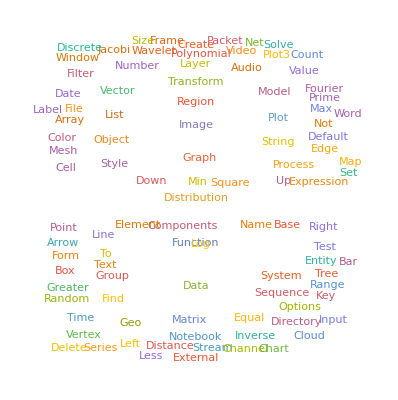

```mathematica
WordCloud[Flatten[If[!StringContainsQ[#,RegularExpression["[A-Z]{2,}"]],StringCases[#,RegularExpression["[A-Z][^A-Z]+"]],If[UpperCaseQ[StringPart[#,-1]],Join[StringCases[#,RegularExpression["[A-Z]{2,}"]],StringCases[#,RegularExpression["[A-Z][^A-Z]+"]]],Join[StringCases[StringReplace[#,{StringDrop[StringCases[#,RegularExpression["[A-Z]{2,}[a-z]"]],-2]->""}],RegularExpression["[A-Z][^A-Z]+"]],StringDrop[StringCases[#,RegularExpression["[A-Z]{2,}[a-z]"]],-2]]]]&/@functionNames]]
```

```mathematica
WordCloud[Flatten[If[!StringContainsQ[#,RegularExpression["[A-Z]{2,}"]],StringCases[#,RegularExpression["[A-Z][^A-Z]+"]],If[UpperCaseQ[StringPart[#,-1]],Join[StringCases[#,RegularExpression["[A-Z]{2,}"]],StringCases[#,RegularExpression["[A-Z][^A-Z]+"]]],Join[StringCases[StringReplace[#,{StringDrop[StringCases[#,RegularExpression["[A-Z]{2,}[a-z]"]],-2]->""}],RegularExpression["[A-Z][^A-Z]+"]],StringDrop[StringCases[#,RegularExpression["[A-Z]{2,}[a-z]"]],-2]]]]&/@(CanonicalName/@WolframLanguageData[])]]
```

-Graphics-

```mathematica
If[!StringContainsQ[#,RegularExpression["[A-Z]{2,}"]],StringCases[#,RegularExpression["[A-Z][^A-Z]+"]],If[UpperCaseQ[StringPart[#,-1]],Join[StringCases[#,RegularExpression["[A-Z]{2,}"]],StringCases[#,RegularExpression["[A-Z][^A-Z]+"]]],Join[StringCases[StringReplace[#,{StringDrop[StringCases[#,RegularExpression["[A-Z]{2,}[a-z]"]],-2]->""}],RegularExpression["[A-Z][^A-Z]+"]],StringDrop[StringCases[#,RegularExpression["[A-Z]{2,}[a-z]"]],-2]]]]&["Plot3D"]
```

{Plot3}

```mathematica
StringContainsQ[#,"3D"]&["Plot3D"]
```

True

```mathematica
If[!StringContainsQ[#,"3D"],If[!StringContainsQ[#,RegularExpression["[A-Z]{2,}"]],StringCases[#,RegularExpression["[A-Z][^A-Z]+"]],If[UpperCaseQ[StringPart[#,-1]],Join[StringCases[#,RegularExpression["[A-Z]{2,}"]],StringCases[#,RegularExpression["[A-Z][^A-Z]+"]]],Join[StringCases[StringReplace[#,{StringDrop[StringCases[#,RegularExpression["[A-Z]{2,}[a-z]"]],-2]->""}],RegularExpression["[A-Z][^A-Z]+"]],StringDrop[StringCases[#,RegularExpression["[A-Z]{2,}[a-z]"]],-2]]]],Join[If[!StringContainsQ[#,RegularExpression["[A-Z]{2,}"]],StringCases[#,RegularExpression["[A-Z][^A-Z]+"]],If[UpperCaseQ[StringPart[#,-1]],Join[StringCases[#,RegularExpression["[A-Z]{2,}"]],StringCases[#,RegularExpression["[A-Z][^A-Z]+"]]],Join[StringCases[StringReplace[#,{StringDrop[StringCases[#,RegularExpression["[A-Z]{2,}[a-z]"]],-2]->""}],RegularExpression["[A-Z][^A-Z]+"]],StringDrop[StringCases[#,RegularExpression["[A-Z]{2,}[a-z]"]],-2]]]]&[StringDelete[#,"3D"]],{"3D"}]]&["Plot3D"]
```

{Plot,3D}

```mathematica
If[!StringContainsQ[#,"3D"],If[!StringContainsQ[#,RegularExpression["[A-Z]{2,}"]],StringCases[#,RegularExpression["[A-Z][^A-Z]+"]],If[UpperCaseQ[StringPart[#,-1]],Join[StringCases[#,RegularExpression["[A-Z]{2,}"]],StringCases[#,RegularExpression["[A-Z][^A-Z]+"]]],Join[StringCases[StringReplace[#,{StringDrop[StringCases[#,RegularExpression["[A-Z]{2,}[a-z]"]],-2]->""}],RegularExpression["[A-Z][^A-Z]+"]],StringDrop[StringCases[#,RegularExpression["[A-Z]{2,}[a-z]"]],-2]]]],Join[If[!StringContainsQ[#,RegularExpression["[A-Z]{2,}"]],StringCases[#,RegularExpression["[A-Z][^A-Z]+"]],If[UpperCaseQ[StringPart[#,-1]],Join[StringCases[#,RegularExpression["[A-Z]{2,}"]],StringCases[#,RegularExpression["[A-Z][^A-Z]+"]]],Join[StringCases[StringReplace[#,{StringDrop[StringCases[#,RegularExpression["[A-Z]{2,}[a-z]"]],-2]->""}],RegularExpression["[A-Z][^A-Z]+"]],StringDrop[StringCases[#,RegularExpression["[A-Z]{2,}[a-z]"]],-2]]]]&[StringDelete[#,"3D"]],{"3D"}]]&["CloudObjectURLType"]
```

{Cloud,Object,Type,URL}

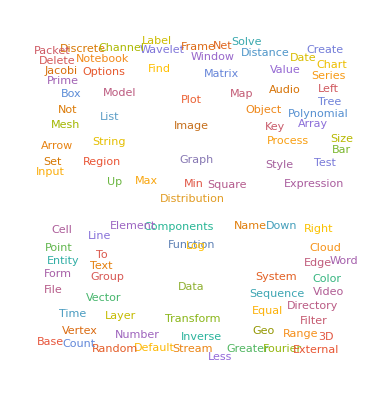

```mathematica
WordCloud[Flatten[If[!StringContainsQ[#,"3D"],If[!StringContainsQ[#,RegularExpression["[A-Z]{2,}"]],StringCases[#,RegularExpression["[A-Z][^A-Z]+"]],If[UpperCaseQ[StringPart[#,-1]],Join[StringCases[#,RegularExpression["[A-Z]{2,}"]],StringCases[#,RegularExpression["[A-Z][^A-Z]+"]]],Join[StringCases[StringReplace[#,{StringDrop[StringCases[#,RegularExpression["[A-Z]{2,}[a-z]"]],-2]->""}],RegularExpression["[A-Z][^A-Z]+"]],StringDrop[StringCases[#,RegularExpression["[A-Z]{2,}[a-z]"]],-2]]]],Join[If[!StringContainsQ[#,RegularExpression["[A-Z]{2,}"]],StringCases[#,RegularExpression["[A-Z][^A-Z]+"]],If[UpperCaseQ[StringPart[#,-1]],Join[StringCases[#,RegularExpression["[A-Z]{2,}"]],StringCases[#,RegularExpression["[A-Z][^A-Z]+"]]],Join[StringCases[StringReplace[#,{StringDrop[StringCases[#,RegularExpression["[A-Z]{2,}[a-z]"]],-2]->""}],RegularExpression["[A-Z][^A-Z]+"]],StringDrop[StringCases[#,RegularExpression["[A-Z]{2,}[a-z]"]],-2]]]]&[StringDelete[#,"3D"]],{"3D"}]]&/@(CanonicalName/@WolframLanguageData[])]]
```

```mathematica
variableWords[list_]:=If[!StringContainsQ[#,"3D"],If[!StringContainsQ[#,RegularExpression["[A-Z]{2,}"]],StringCases[#,RegularExpression["[A-Z][^A-Z]+"]],If[UpperCaseQ[StringPart[#,-1]],Join[StringCases[#,RegularExpression["[A-Z]{2,}"]],StringCases[#,RegularExpression["[A-Z][^A-Z]+"]]],Join[StringCases[StringReplace[#,{StringDrop[StringCases[#,RegularExpression["[A-Z]{2,}[a-z]"]],-2]->""}],RegularExpression["[A-Z][^A-Z]+"]],StringDrop[StringCases[#,RegularExpression["[A-Z]{2,}[a-z]"]],-2]]]],Join[If[!StringContainsQ[#,RegularExpression["[A-Z]{2,}"]],StringCases[#,RegularExpression["[A-Z][^A-Z]+"]],If[UpperCaseQ[StringPart[#,-1]],Join[StringCases[#,RegularExpression["[A-Z]{2,}"]],StringCases[#,RegularExpression["[A-Z][^A-Z]+"]]],Join[StringCases[StringReplace[#,{StringDrop[StringCases[#,RegularExpression["[A-Z]{2,}[a-z]"]],-2]->""}],RegularExpression["[A-Z][^A-Z]+"]],StringDrop[StringCases[#,RegularExpression["[A-Z]{2,}[a-z]"]],-2]]]]&[StringDelete[#,"3D"]],{"3D"}]]&[list]
```

```mathematica
variableWords/@Names["*Function*"]
```

{{Absolute,Correlation,Function},{Ambiguity,Function},{Anomaly,Detector,Function},{Function,API},{Ask,Function},{Assessment,Function},{Autocompletion,Function},{Bezier,Function},{Boolean,Consecutive,Function},{Boolean,Counting,Function},{Boolean,Function},{Spline,Function,B},{Button,Function},{Cell,Evaluation,Function},{Central,Moment,Generating,Function},{Channel,Pre,Send,Function},{Channel,Receiver,Function},{Characteristic,Function},{Chart,Element,Data,Function},{Chart,Element,Function},{Classifier,Function},{Cloud,Function},{Cluster,Dissimilarity,Function},{Color,Data,Function},{Color,Function},{Color,Function,Binning},{Color,Function,Scaling},{Combiner,Function},{Compiled,Code,Function},{Compiled,Function},{Complexity,Function},{Connect,Library,Callback,Function},{Content,Detector,Function},{Content,Location,Function},{Cookie,Function},{Copy,Function},{Correlation,Function},{Counter,Function},{Covariance,Estimator,Function},{Covariance,Function},{Criterion,Function},{Cumulant,Generating,Function},{Cylindrical,Decomposition,Function},{Date,Function},{Define,Resource,Function},{Delivery,Function},{Dimension,Reducer,Function},{Dispersion,Estimator,Function},{Display,Function},{Distance,Function},{Echo,Function},{Edge,Rendering,Function},{Edge,Shape,Function},{Entity,Function},{Epilog,Function},{Exponent,Function},{Exponential,Generating,Function},{Extent,Element,Function},{External,Function},{External,Function,Name},{Factorial,Moment,Generating,Function},{Feature,Extractor,Function},{Fetch,Referenced,Functions},{Field,Completion,Function},{Find,Generating,Function},{Find,Sequence,Function},{Form,Function},{Form,Layout,Function},{Function},{Function,Analytic},{Function,Bijective},{Function,Compile},{Function,Compile,Export},{Function,Compile,Export,Byte,Array},{Function,Compile,Export,Library},{Function,Compile,Export,String},{Function,Continuous},{Function,Convexity},{Function,Declaration},{Function,Discontinuities},{Function,Domain},{Function,Expand},{Function,Injective},{Function,Interpolation},{Function,Layer},{Function,Meromorphic},{Function,Monotonicity},{Function,Period},{Function,Poles},{Function,Range},{Function,Sign},{Function,Singularities},{Function,Space},{Function,Surjective},{Gauge,Face,Element,Function},{Gauge,Frame,Element,Function},{Generating,Function},{Geo,Styling,Image,Function},{Green,Function},{Guide,Page,Inline,Listing,Function},{Guide,Page,One,Line,Function},{Handler,Functions},{Handler,Functions,Keys},{Hazard,Function},{Header,Display,Function},{Image,Capture,Function},{Image,Preview,Function},{Insertion,Function},{Interpolating,Function},{Interpretation,Function},{Inverse,Function},{Inverse,Functions},{Inverse,Survival,Function},{Item,Display,Function},{Kernel,Function},{Key,Collision,Function},{Labeling,Function},{Layer,Size,Function},{Legend,Function},{Library,Function},{Library,Function,Declaration},{Library,Function,Error},{Library,Function,Information},{Library,Function,Load},{Library,Function,Unload},{Linear,Offset,Function},{Linear,Solve,Function},{Link,Function},{Loss,Function},{Mail,Receiver,Function},{Mail,Response,Function},{Mathematical,Function,Data},{Matrix,Function},{Merging,Function},{Mesh,Cell,Shape,Function},{Mesh,Functions},{Mesh,Refinement,Function},{Moment,Generating,Function},{Multiline,Function},{Nearest,Function},{Normals,Function},{Norm,Function},{Notification,Function},{Numeric,Function},{Opacity,Function},{Opacity,Function,Scaling},{Open,Function,Inspector,Packet},{Parametric,Function},{Parent,Edge,Label,Function},{Parent,Edge,Shape,Function},{Parent,Edge,Style,Function},{Partial,Correlation,Function},{Persist,Resource,Function},{Point,Density,Function},{Point,Statistic,Function},{Predictor,Function},{Random,Function},{Rational,Functions},{Recalibration,Function},{Region,Distance,Function},{Region,Function},{Region,Member,Function},{Region,Nearest,Function},{Resource,Function},{Return,Receipt,Function},{Sampled,Sound,Function},{Scaling,Functions},{Sequence,Predictor,Function},{Set,Shared,Function},{Shortest,Path,Function},{Spatial,Estimator,Function},{Spatial,Trend,Function},{Stream,Color,Function},{Stream,Color,Function,Scaling},{Survival,Function},{Target,Functions},{Text,Resource,Function},{Texture,Coordinate,Function},{Tracking,Function},{Traditional,Function,Notation},{Training,Progress,Function},{Transfer,Function,Cancel},{Transfer,Function,Expand},{Transfer,Function,Factor},{Transfer,Function,Model},{Transfer,Function,Poles},{Transfer,Function,Transform},{Transfer,Function,Zeros},{Transformation,Function},{Transformation,Functions},{Tree,Element,Label,Function},{Tree,Element,Shape,Function},{Tree,Element,Size,Function},{Tree,Element,Style,Function},{Utility,Function},{Value,Preprocessing,Function},{Variance,Estimator,Function},{Variogram,Function},{Vector,Color,Function},{Vector,Color,Function,Scaling},{Vertex,Rendering,Function},{Vertex,Shape,Function},{Word,Selection,Function},{Allow,External,Channel,Functions},{Assert,Function},{Display,Function},{Shared,Functions},{Sound,Display,Function}}

```mathematica
wordCloudFromVariables[data_]:=WordCloud[Flatten[variableWords/@data]]
```

```mathematica
wordCloudFromVariables[CanonicalName/@WolframLanguageData[]]
```

-Graphics-

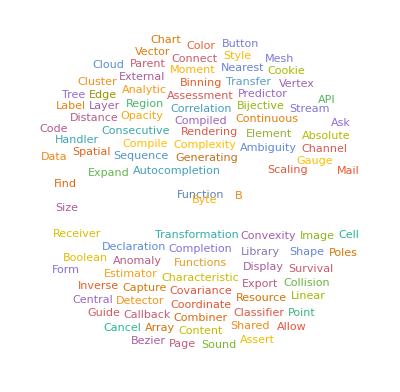

```mathematica
wordCloudFromVariables[Names["*Function*"]]
```

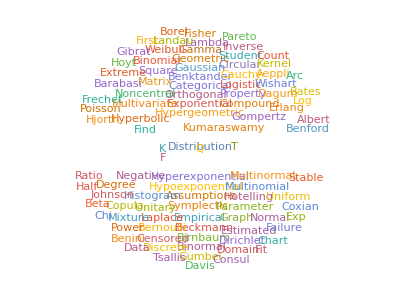

```mathematica
wordCloudFromVariables[Names["*Distribution*"]]
```

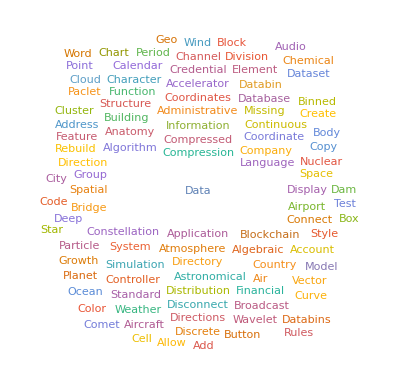

```mathematica
wordCloudFromVariables[Names["*Data*"]]
```